# Process tomography: χ, Λ matrices

```mathematica
Remove["Global`*"]
```

```mathematica
pathToData="L:\\local-expdata\\2 Qubit Experiments\\FO-C5\\3rd-Run\\";
```

## Library ComplexMatrixDraw (copy to your Notebook, evaluate and use the complexMatrixDraw function)

### ComplexMatrixDraw Code (copy to your Notebook, evaluate and use the ComplexMatrixDraw function)

Introduction: ComplexMatrixDraw daws a rectangular matrix of complex numbers cij as an array of cells, each cell having possibly:
	- a frame and a central point;
	- a 2D shape with an area proportional to |cij| or given by the optional function functionFor2DShapeArea(cij);
	- an arrow with angle arg(cij) and length  |cij| or given by the optional function  functionForArrowLength(cij);
	- a label.
	
Syntax: ComplexMatrixDraw[m,opts] with 
	m: a number, a vector (list of numbers) or a matrix (a list of list of numbers)
	opts: optional replacement rules of the type optionName->optionValue as described below:

Several options (with default behavior) are available:
	
	Option for cell placement. The matrix cell i,j (i=1 to number of lines (top to bottom), j=1 to number of columns (left to rigth) is drawn by default between coordinates j-1 and j for x and  -i+1 and -i+1.5 for y.
		ignoreCell:  function of the position {i,j} returning True or False to decide whether to ignore the ij cell, or to draw it normally. Default is the pure function False & giving always false.
		offset: a list {xOffset,yOffset} (default is {0,0}) indicating how to shift the matrix. 	
	Options for the cell frame:
		- showFrame: True (default) or False. Draw a black square around each matrix cell
		- frameFaceFunction: function of the position {i,j} returning directives for rendering the face of the square frame (default is {White, Opacity[0]}&, i.e. transparent)
		- showCentralPoint: True or False (default) wheter to draw a central point in the cell.
		- centralPointSize: parameter of the PointSize directive (Tiny,Small, Medium, or a relative size like 0.01 for example).
	Options for the 2D shape representing the complex number:
		- show2DShape: True (default) or False. Whether to draw the 2D shape or not.
		- whatShape: "circle" (default) or "square".
		- functionFor2DShapeAera: any  single argument function to be applied to cij to define the area of the 2D shape (default is Abs).
		- hide2DShapeSmallerThan: Value of functionFor2DShapeAera(cij) below which the 2D shape should not be drawn  (default is 0).
		- borderDirectives: graphics directive for the EdgeForm function (color, thickness, type of line, etc): default is {Black, Thickness[0,001]}.
		- fill2DShape: whether to fill the 2Dshape (default is True);
		- fillingColor: Filling color function  f[ |cij| , arg(cij)] of the 2D shape. Default is Hue[#2/(2π)+0.5]&, i.e a cyclic color function of the phase arg(cij) that is cyan for φ=0 and red for φ=π .
	Options for the Arrow representing the complex Number
		- showArrow:  True (default) or False. wheter to draw the arrow or not.
		- functionForArrowLength: any  single argument function to be applied to cij to define the length of the arrow (default is Abs).
		- hideArrowSmallerThan: Value of functionForArrowLength(cij) below which the arrow should not be drawn  (default is 0).
		- arrowDirectives:  graphics directive before the Arrow function (color, thickness, type of line, etc): Default is {Black, Thickness[0.001], Arrowheads[0.05]}
	Options for the label included in the cell
		- showLabel: True or False (default). Whether to write the number in the cell or not.
		- labelFunction: Function to apply to the number to form the label. Default is Identity
		- labelStyle: A directive for Style[], such as Small (default), Medium, Large, Red ...
		- labelShift: a list {Δx,Δy} (default is {0,0}) indicating how to shift the text in the cell.

```mathematica
Options[myPlotElement]=
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
show2DShape->True,whatShape->"circle",functionFor2DShapeAera->Abs,hide2DShapeSmallerThan->0,borderDirectives->{Black,Thickness[0.001]},fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5]&),
showArrow->True,functionForArrowLength->Abs,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}
} ;
myPlotElement[c_,position_,OptionsPattern[]]:=
Block[
{center=position+{-0.5,1.5}+OptionValue[offset],
shapeAera=OptionValue[functionFor2DShapeAera][c],
arrowLength=OptionValue[functionForArrowLength][c],
φ=Arg[c],
frame={},shape={},arrow={},centralPoint={},number={}
},
If[!OptionValue[ignoreCell][position],If[OptionValue[showFrame],frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Rectangle[center-0.5{1,-1},center+0.5{1,-1}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[show2DShape ]&& shapeAera>=OptionValue[hide2DShapeSmallerThan],
shape={EdgeForm[OptionValue[borderDirectives]],If[OptionValue[fill2DShape],FaceForm[OptionValue[fillingColor][Abs[c],φ]],FaceForm[]]};
shape=Append[shape,
Switch[OptionValue[whatShape],
"square",Rectangle[center-Sqrt[shapeAera]/2,center+Sqrt[shapeAera]/2],
_,Disk[center,Sqrt[shapeAera]/2]]]];
If[OptionValue[showArrow] && arrowLength>=OptionValue[hideArrowSmallerThan],
arrow=Append[OptionValue[arrowDirectives],Arrow[{center,center+0.5arrowLength{Cos[φ],Sin[φ]}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics[frame~Join~centralPoint~Join~shape~Join~arrow~Join~centralPoint~Join~number]];
complexMatrixDraw[number_?NumberQ,opts___]:=complexMatrixDraw[{{number}},opts];
complexMatrixDraw[vector_?VectorQ,opts___]:=complexMatrixDraw[List/@vector,opts];
complexMatrixDraw[matrix_,opts___]:=Show[MapIndexed[myPlotElement[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}]];
```

```mathematica
lowerTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]>-#[[2]]&)]
upperTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]<-#[[2]]&)]
diagonalComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]!=-#[[2]]&)]
```

### matrixDraw3D

```mathematica
Options[myPlotElement3D]=
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
showBar->True,whatBarShape->"circle",barLengthFunction->Abs,barDiameter->0.99,hideBarSmallerThan->0,barDirectives->{Opacity[1]},barColorFunction->(Hue[#2/(2π )+0.5]&),
showArrow->True,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},arrowLength->(1/2&),
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}};

myPlotElement3D[c_,position_,OptionsPattern[]]:=
Block[
{center=position+{-0.5,1.5}+OptionValue[offset],φ=Arg[c],frame={},bar={},arrow={},centralPoint={},number={},val=OptionValue[barLengthFunction][c]},
If[!OptionValue[ignoreCell][position],
If[OptionValue[showFrame],
frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Polygon[{Append[center+{-0.5,-0.5},0],Append[center+{0.5,-0.5},0],Append[center+{0.5,0.5},0],Append[center+{-0.5,0.5},0]}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[Append[center,0]]}];
If[OptionValue[showBar] &&Abs[val]>OptionValue[hideBarSmallerThan],
bar=Append[OptionValue[barDirectives],OptionValue[barColorFunction][val,Arg[c]]];
bar=Append[bar,
Switch[OptionValue[whatBarShape],
"square",Cuboid[Append[center-OptionValue[barDiameter]{0.5,0.5},0],Append[center+OptionValue[barDiameter]{0.5,0.5},val]],
_,Cylinder[{Append[center,0],Append[center,val]},OptionValue[barDiameter]/2]]]];
If[OptionValue[showArrow] && Abs[val]>OptionValue[hideArrowSmallerThan],
arrow=OptionValue[arrowDirectives];
AppendTo[arrow,Arrow[{Append[center,val],Append[center,val]+OptionValue[arrowLength][val]{ Cos[Arg[c]], Sin[Arg[c]],0}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics3D[frame~Join~centralPoint~Join~bar~Join~arrow~Join~centralPoint~Join~number,Lighting->{{"Ambient",White}}]];

matrixDraw3D[number_?NumberQ,opts___]:=matrixDraw3D[{{number}},opts];
matrixDraw3D[vector_?VectorQ,opts___]:=matrixDraw3D[List/@vector,opts];
matrixDraw3D[matrix_,opts___]:=Show[MapIndexed[myPlotElement3D[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}],BoxRatios->{1,1,1}];
```

## Some utility functions (evaluate)

makeColVect transform a list of numbers {n1, n2, n3}  into a column vector  { {n1}, {n2}, {n3}}.
ρToVect "columnizes" a density matrix column by column 
{{ρ11, ρ12, ρ13, ρ14},{ρ21, ρ22, ρ23, ρ24}, {ρ31, ρ32, ρ33, ρ34}, {ρ41, ρ42, ρ43, ρ44} }==>{ {ρ11}, {ρ21}, {ρ31}, {ρ41}, {ρ12}, {ρ22}, {ρ32}, {ρ42}, {ρ13},{ ρ23}, {ρ33}, {ρ43}, {ρ14}, {ρ24}, {ρ34}, {ρ44} }

```mathematica
Remove[myCompareGraph]
```

```mathematica
makeColVect[xList_]:={#}&/@xList;

ρToVect=Composition[ makeColVect,Flatten,Transpose];

decomposeInBase[v_, vList_]:=LinearSolve[Flatten/@vList//Transpose,Flatten[v]];

fidDensity[ρ1_,ρ2_]=Chop[Tr[MatrixPower[Chop[MatrixPower[ρ1,1/2].ρ2.MatrixPower[ρ1,1/2]],1/2]]]^2;
fidChi[χ1_,χRef_]=Chop[Tr[χ1.χRef]];

myOpts1={functionForArrowLength->(Sqrt[Abs[#]]&),fill2DShape->False};
myCompareGraph[mList_,colorList_:{Red,Blue,RGBColor[0,0.5,0],Blue, Magenta},fid_:"None",title_:""]:=
Block[{label=Switch[fid,"None","",_,"F12="<>ToString[Round[100ToExpression[fid][mList[[1]],mList[[2]]]]/100.]]},
Show[
MapIndexed[complexMatrixDraw[#1,myOpts1~Join~{borderDirectives->{colorList[[Mod[#2[[1]],Length[colorList],1]]]},arrowDirectives->{Arrowheads[0],colorList[[Mod[#2[[1]],Length[colorList],1]]]}}]&,mList,{1}]
,PlotLabel->label]
];
```

## Definitions of the ideal states, density matrices, operator basis and β matrix (evaluate)

### States and density matrices for process map

We define:
base1={ |0>, |1>}as the single qubit state basis
base2={|00>,|01>,|10>,|11>}={|0>, |1>, |2>, |3>} as the two qubit state basis
stateSet1={ |0>, |1>,  |+> = |0> + |1>,  |-> = |0> + i |1>} and the tensorial product stateSet2=stateSet1x2 as the set of states used to map the process.
Then we built the ρListIn, the list of density matrices  corresponding to stateSet2  (expressed in base2). Note that ρListIn is a base for the 4x4 density matrices.

For superoperator formalism, density matrices are "columnized" column by column: {ρ11, ρ21, ρ31, ρ41, ρ12, ρ22, ρ32, ρ42, ρ13, ρ23, ρ33, ρ43, ρ14, ρ24, ρ34, ρ44 }.
we also define a simpler (but non physical) basis for density matrices:
ρBase2 = the 16  4x4 density matrices with all elements equal to 0 except one equal to 1 (in the order ρ11=1, ρ21=1, ... so that the index of the matrix corresponds to that of element 1 in the corresponding columnized vector).

```mathematica
Clear[k0,k1,kPlus,kMinus];
stateBase1Name={"0","1"};
stateSet1Name={"0","1","+","-"};
ketBase1={k0,k1};
ketSet1={k0,k1,kPlus,kMinus};
```

```mathematica
stateBase2Name=Outer[#1<>#2&,stateBase1Name,stateBase1Name]//Flatten;
stateSet2Name=Outer[#1<>#2&,stateSet1Name,stateSet1Name]//Flatten;
ketBase2=Outer[KroneckerProduct,ketBase1,ketBase1]//Flatten;
ketSet2=Outer[KroneckerProduct,ketSet1,ketSet1]//Flatten;
```

```mathematica
k0={1,0}//makeColVect;
k1={0,1}//makeColVect;
kPlus={1,1}/Sqrt[2]//makeColVect;
kMinus={1,+ⅈ}/Sqrt[2]//makeColVect;
```

```mathematica
ρBase2=Transpose/@MapIndexed[Partition[ReplacePart[#1,#2[[1]]->1],4]&,ConstantArray[0,{16,16}]];
```

```mathematica
ketSet1=ketSet1;
ketSet2=ketSet2;
braSet1=ConjugateTranspose /@ ketSet1;
braSet2=ConjugateTranspose /@ ketSet2;
ρListIn=MapThread[Dot,{ketSet2,braSet2}];
```

```mathematica
Print["stateBase2Name=\n",stateBase2Name]
Print["ketBase2=\n",MatrixForm/@ketBase2]
Print["ketSet2=\n",MatrixForm/@ketSet2]
Print["ρListIn=\n",MatrixForm/@ρListIn]
Print["ρBase2=\n",MatrixForm/@ρBase2]
Print["columnized ρBase2=\n",MatrixForm/@(ρToVect/@ρBase2)]
```

stateBase2Name=
{00,01,10,11}

ketBase2=
{(1
0
0
0),(0
1
0
0),(0
0
1
0),(0
0
0
1)}

ketSet2=
{(1
0
0
0),(0
1
0
0),(1/(√2)
1/(√2)
0
0),(1/(√2)
ⅈ/(√2)
0
0),(0
0
1
0),(0
0
0
1),(0
0
1/(√2)
1/(√2)),(0
0
1/(√2)
ⅈ/(√2)),(1/(√2)
0
1/(√2)
0),(0
1/(√2)
0
1/(√2)),(1/2
1/2
1/2
1/2),(1/2
ⅈ/2
1/2
ⅈ/2),(1/(√2)
0
ⅈ/(√2)
0),(0
1/(√2)
0
ⅈ/(√2)),(1/2
1/2
ⅈ/2
ⅈ/2),(1/2
ⅈ/2
ⅈ/2
-1/2)}

ρListIn=
{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1/2 | 1/2 | 0 | 0
1/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1/2 | -ⅈ/2 | 0 | 0
ⅈ/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1/2 | 1/2
0 | 0 | 1/2 | 1/2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1/2 | -ⅈ/2
0 | 0 | ⅈ/2 | 1/2),(1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0
1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2),(1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4),(1/4 | -ⅈ/4 | 1/4 | -ⅈ/4
ⅈ/4 | 1/4 | ⅈ/4 | 1/4
1/4 | -ⅈ/4 | 1/4 | -ⅈ/4
ⅈ/4 | 1/4 | ⅈ/4 | 1/4),(1/2 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0
ⅈ/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | -ⅈ/2
0 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 1/2),(1/4 | 1/4 | -ⅈ/4 | -ⅈ/4
1/4 | 1/4 | -ⅈ/4 | -ⅈ/4
ⅈ/4 | ⅈ/4 | 1/4 | 1/4
ⅈ/4 | ⅈ/4 | 1/4 | 1/4),(1/4 | -ⅈ/4 | -ⅈ/4 | -1/4
ⅈ/4 | 1/4 | 1/4 | -ⅈ/4
ⅈ/4 | 1/4 | 1/4 | -ⅈ/4
-1/4 | ⅈ/4 | ⅈ/4 | 1/4)}

ρBase2=
{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0),(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)}

columnized ρBase2=
{(1
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
1
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
1
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
1
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
1
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
1
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
1
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
1
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
1
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
1
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
1
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
1
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
1
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
1
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
0
1
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
1)}

### Operators on states

We choose the Pauli bases for the operators, with a minor change: σy is replaced by i σy to get real numbers everywhere.
So we get
opBase1={I=Identity, X=σx, Y=i σy, Z=σz} as the operator basis for a single qubit
opBase2 = opBase1 x opBase1 for the operator basis on two qubits.

```mathematica
opBase1Name={"I","X","Y","Z"};
Clear[id,σx,iσy,σz];
opBase1={id,σx,iσy,σz};
opBase2Name=Outer[StringJoin,opBase1Name,opBase1Name]//Flatten;
opBase2=Outer[KroneckerProduct,opBase1,opBase1]//Flatten;
id={{1,0},{0,1}};
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
iσy=I σy;
σz={{1,0},{0,-1}};
opBase1=opBase1;
opBase2=opBase2;
```

```mathematica
σx1=KroneckerProduct[σx,id];
σy1=KroneckerProduct[σy,id];
σz1=KroneckerProduct[σz,id];
σx2=KroneckerProduct[id,σx];
σy2=KroneckerProduct[id,σy];
σz2=KroneckerProduct[id,σz];
```

```mathematica
Print["opBase1Names=\n",MatrixForm/@opBase1Name]
Print["opBase1=\n",MatrixForm/@opBase1]
Print["opBase2Names=\n",MatrixForm/@opBase2Name]
Print["opbase2=\n",MatrixForm/@opBase2]
```

opBase1Names=
{I,X,Y,Z}

opBase1=
{(1 | 0
0 | 1),(0 | 1
1 | 0),(0 | 1
-1 | 0),(1 | 0
0 | -1)}

opBase2Names=
{II,IX,IY,IZ,XI,XX,XY,XZ,YI,YX,YY,YZ,ZI,ZX,ZY,ZZ}

opbase2=
{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)}

### The β matrix

Let us call Ek the Pauli operators of opBase2 and ρj the density matrices of ρBase2.
We define the 256 x 256  β matrix by E_m ρ_j E_n^†= ∑_(k=1)^16 β_(j,k,m,n)ρ_k ,
where couples (j,k) and (m,n) have to be transformed in two indices s and t.
We take s and t as the indices of elements in the tensorial (outer) products ρBase2 x ρBase2 and opBase2 x opBase2, respectively.
As shown below s =16 (j-1)+ k, so that j=Quotient[s, 16, 1]+1 and k=Mod[s, 16, 1]. Same for t,m,n.

```mathematica
r1=Range[16];l1=Flatten[Outer[List,r1,r1],1]
l2={Quotient[#,16,1]+1,Mod[#,16,1]}&/@Range[256];
l1==l2
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{11,11},{11,12},{11,13},{11,14},{11,15},{11,16},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{12,11},{12,12},{12,13},{12,14},{12,15},{12,16},{13,1},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{13,10},{13,11},{13,12},{13,13},{13,14},{13,15},{13,16},{14,1},{14,2},{14,3},{14,4},{14,5},{14,6},{14,7},{14,8},{14,9},{14,10},{14,11},{14,12},{14,13},{14,14},{14,15},{14,16},{15,1},{15,2},{15,3},{15,4},{15,5},{15,6},{15,7},{15,8},{15,9},{15,10},{15,11},{15,12},{15,13},{15,14},{15,15},{15,16},{16,1},{16,2},{16,3},{16,4},{16,5},{16,6},{16,7},{16,8},{16,9},{16,10},{16,11},{16,12},{16,13},{16,14},{16,15},{16,16}}

True

```mathematica
Clear[β];
β[j_,k_,m_,n_]:=ρToVect[opBase2[[m]].ρBase2[[j]].ConjugateTranspose[opBase2[[n]]]][[k,1]];

β[s_,t_]:=β[Quotient[s,16,1]+1,Mod[s,16,1],Quotient[t,16,1]+1,Mod[t,16,1]];
(βMatrix=Table[β[s,t],{s,1,256},{t,1,256}])//MatrixForm;
βMatrixInv=Inverse[βMatrix];
```

## Definitions of the ideal √iSWAPoperator, λIdeal superoperator, and χIdeal matrices (evaluate)

### ideal √iSWAP evolution operator

Let uS=U  be the ideal evolution operator (unitary) on the two qubit state and uST its hermitian conjugate.

```mathematica
(uS={{1,0,0,0},{0,1/Sqrt[2],-ⅈ/Sqrt[2],0},{0,-ⅈ/Sqrt[2],1/Sqrt[2],0},{0,0,0,1}})//MatrixForm
(uST=ConjugateTranspose[uS])//MatrixForm;
```

(1 | 0 | 0 | 0
0 | 1/(√2) | -ⅈ/(√2) | 0
0 | -ⅈ/(√2) | 1/(√2) | 0
0 | 0 | 0 | 1)

### λ superoperator

One has ρ_out= U ρ_in U^† equivalent to ρ_out=λ ρ_in with columnized ρ's

```mathematica
ρin0={{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}};
vin0=ρToVect[ρin0];
ρout0=uS.ρin0.uST;
vout0=ρToVect[ρout0];
λIdeal=Coefficient[#,Flatten[vin0]]&/@Flatten[vout0];
Print["λ Matrix =",MatrixForm[λIdeal]]
```

λ Matrix =(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 1/2 | 0 | 0 | 1/2 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/2 | 1/2 | 0 | 0 | 1/2 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | -ⅈ/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

### χ matrix from theoretical expression

uS =U can be decomposed in the pauli basis opBase2: U = ∑_(m=1)^16 α_m E_m =  α⃗. (we use decomposeInBase).
As ρ_out= U ρ_in U^† , we get  ρ_out= ∑_(m, n)  α_mα_n^*E_m ρ_in E_m^† = ∑_(m, n)  χ_(m n)E_m ρ_in E_m^†. So χ = α⃗ . ConjugateTranspose[ α⃗ ].

```mathematica
αVec=decomposeInBase[Flatten[uS],Flatten/@opBase2]//makeColVect ;
χIdeal1=FullSimplify[αVec.ConjugateTranspose[αVec]];
Print["operator U in basis ",opBase2Name," is ",Flatten[αVec]]
Print["χ=",MatrixForm[χIdeal1]]
```

operator U in basis {II,IX,IY,IZ,XI,XX,XY,XZ,YI,YX,YY,YZ,ZI,ZX,ZY,ZZ} is {1/4 (2+√2),0,0,0,0,-ⅈ/(2 √2),0,0,0,0,ⅈ/(2 √2),0,0,0,0,1/4 (2-√2)}

χ=(1/8 (3+2 √2) | 0 | 0 | 0 | 0 | 1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | -1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | -1/8 | 0 | 0 | 0 | 0 | -1/8 ⅈ (-1+√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | -1/8 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 1/8 ⅈ (-1+√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/8 | 0 | 0 | 0 | 0 | 1/8 ⅈ (-1+√2) | 0 | 0 | 0 | 0 | -1/8 ⅈ (-1+√2) | 0 | 0 | 0 | 0 | 1/8 (3-2 √2))

### χ matrix recalculation from ideal process map

Here we check that we find the same χ matrix from the 16 ideal output density matrix ρout.
We first calculate the ρout's:

```mathematica
ρListOut=uS.#.uST&/@ρListIn;
ρListIdeal:={ρListIn,ρListOut}
Print["List of output density matrices in basis ",stateBase2Name," = ",MatrixForm/@(ρListOut)]
```

List of output density matrices in basis {00,01,10,11} = {(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | ⅈ/2 | 0
0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0),(1/2 | 1/(2 √2) | ⅈ/(2 √2) | 0
1/(2 √2) | 1/4 | ⅈ/4 | 0
-ⅈ/(2 √2) | -ⅈ/4 | 1/4 | 0
0 | 0 | 0 | 0),(1/2 | -ⅈ/(2 √2) | 1/(2 √2) | 0
ⅈ/(2 √2) | 1/4 | ⅈ/4 | 0
1/(2 √2) | -ⅈ/4 | 1/4 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | -ⅈ/2 | 0
0 | ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1),(0 | 0 | 0 | 0
0 | 1/4 | -ⅈ/4 | -ⅈ/(2 √2)
0 | ⅈ/4 | 1/4 | 1/(2 √2)
0 | ⅈ/(2 √2) | 1/(2 √2) | 1/2),(0 | 0 | 0 | 0
0 | 1/4 | -ⅈ/4 | -1/(2 √2)
0 | ⅈ/4 | 1/4 | -ⅈ/(2 √2)
0 | -1/(2 √2) | ⅈ/(2 √2) | 1/2),(1/2 | ⅈ/(2 √2) | 1/(2 √2) | 0
-ⅈ/(2 √2) | 1/4 | -ⅈ/4 | 0
1/(2 √2) | ⅈ/4 | 1/4 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/4 | ⅈ/4 | 1/(2 √2)
0 | -ⅈ/4 | 1/4 | -ⅈ/(2 √2)
0 | 1/(2 √2) | ⅈ/(2 √2) | 1/2),(1/4 | (1/4+ⅈ/4)/(√2) | (1/4+ⅈ/4)/(√2) | 1/4
(1/4-ⅈ/4)/(√2) | 1/4 | 1/4 | (1/4-ⅈ/4)/(√2)
(1/4-ⅈ/4)/(√2) | 1/4 | 1/4 | (1/4-ⅈ/4)/(√2)
1/4 | (1/4+ⅈ/4)/(√2) | (1/4+ⅈ/4)/(√2) | 1/4),(1/4 | 0 | 1/(2 √2) | -ⅈ/4
0 | 0 | 0 | 0
1/(2 √2) | 0 | 1/2 | -ⅈ/(2 √2)
ⅈ/4 | 0 | ⅈ/(2 √2) | 1/4),(1/2 | 1/(2 √2) | -ⅈ/(2 √2) | 0
1/(2 √2) | 1/4 | -ⅈ/4 | 0
ⅈ/(2 √2) | ⅈ/4 | 1/4 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/4 | ⅈ/4 | -ⅈ/(2 √2)
0 | -ⅈ/4 | 1/4 | -1/(2 √2)
0 | ⅈ/(2 √2) | -1/(2 √2) | 1/2),(1/4 | 1/(2 √2) | 0 | -ⅈ/4
1/(2 √2) | 1/2 | 0 | -ⅈ/(2 √2)
0 | 0 | 0 | 0
ⅈ/4 | ⅈ/(2 √2) | 0 | 1/4),(1/4 | (1/4-ⅈ/4)/(√2) | (1/4-ⅈ/4)/(√2) | -1/4
(1/4+ⅈ/4)/(√2) | 1/4 | 1/4 | -(1/4+ⅈ/4)/(√2)
(1/4+ⅈ/4)/(√2) | 1/4 | 1/4 | -(1/4+ⅈ/4)/(√2)
-1/4 | -(1/4-ⅈ/4)/(√2) | -(1/4-ⅈ/4)/(√2) | 1/4)}

```mathematica
χIdeal2=βMatrixInv.Flatten[λIdeal]//Partition[#,16]&//FullSimplify;
Print["χ=",MatrixForm[χIdeal2]]
```

χ=(1/8 (3+2 √2) | 0 | 0 | 0 | 0 | 1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | -1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | -1/8 | 0 | 0 | 0 | 0 | -1/8 ⅈ (-1+√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | -1/8 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 1/8 ⅈ (-1+√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/8 | 0 | 0 | 0 | 0 | 1/8 ⅈ (-1+√2) | 0 | 0 | 0 | 0 | -1/8 ⅈ (-1+√2) | 0 | 0 | 0 | 0 | 1/8 (3-2 √2))

```mathematica
χIdeal2==χIdeal1
```

True

```mathematica
χIdeal=χIdeal1;
```

## Lindblad with relaxation - λ Process (evaluate)

-Graphics-

We define the two qubit density matrix and its columnized form

```mathematica
(ρ={{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}})//MatrixForm;
(ρVec=ρ//Transpose//Flatten)//MatrixForm;
```

We define the hamiltonian (g and Δ=ω2-ω1 are angular frequencies = energies divided by hbar ) and check that the corresponding unitary evolution is the ideal one (defined everywhere in this notebook).

```mathematica
(hSW[g_,Δ_]=1/2{{0,0,0,0},{0,Δ,g,0},{0,g,-Δ,0},{0,0,0,0}})//MatrixForm
(hMatrix[g_,Δ_]=CoefficientArrays[Flatten[Transpose[hSW[g,Δ].ρ-ρ.hSW[g,Δ]]],ρVec][[2]]//Normal)//MatrixForm;
(uS2=MatrixExp[-I hSW[g,0] 2π/4/g]//FullSimplify)//MatrixForm
uS2==uS
hMatrix[g,Δ]//MatrixForm
```

(0 | 0 | 0 | 0
0 | Δ/2 | g/2 | 0
0 | g/2 | -Δ/2 | 0
0 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 1/(√2) | -ⅈ/(√2) | 0
0 | -ⅈ/(√2) | 1/(√2) | 0
0 | 0 | 0 | 1)

True

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Δ/2 | g/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | g/2 | -Δ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Δ/2 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | g/2 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | g/2 | -Δ | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | Δ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | Δ | g/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -g/2 | 0 | 0 | g/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | Δ/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ/2 | g/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | g/2 | -Δ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
σp = {{0, 0}, {1, 0}};
σm = {{0,1}, {0, 0}}; 
σm1=KroneckerProduct[σm,id];
σm2=KroneckerProduct[id,σm];
c1r=√Γr1 σm1;
c2r=√Γr2 σm2;
c1ϕ=√(Γϕ1/2)σz1;
c2ϕ=√(Γϕ2/2)σz2;
(MatrixForm/@{c1r,c2r,c1ϕ,c2ϕ})//Row
```

(0 | 0 | √Γr1 | 0
0 | 0 | 0 | √Γr1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)(0 | √Γr2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | √Γr2
0 | 0 | 0 | 0)((√Γϕ1)/(√2) | 0 | 0 | 0
0 | (√Γϕ1)/(√2) | 0 | 0
0 | 0 | -(√Γϕ1)/(√2) | 0
0 | 0 | 0 | -(√Γϕ1)/(√2))((√Γϕ2)/(√2) | 0 | 0 | 0
0 | -(√Γϕ2)/(√2) | 0 | 0
0 | 0 | (√Γϕ2)/(√2) | 0
0 | 0 | 0 | -(√Γϕ2)/(√2))

-Graphics-

```mathematica
assumptions={Γr1>0,Γr2>0,Γϕ1>0,Γϕ2>0};
liouv[s_]:=Block[{sds=ConjugateTranspose[s].s},Simplify[s.ρ.ConjugateTranspose[s]-1/2(ρ.sds+sds.ρ),assumptions]];
l=(Plus @@(liouv/@{c1r,c2r,c1ϕ,c2ϕ}))//FullSimplify//Transpose//Flatten;
mRel=CoefficientArrays[l,ρVec][[2]]//Normal;
Plus@@(mRel.ρVec-l//FullSimplify)==0
mRelax[Γr1_,Γr2_,Γϕ1_,Γϕ2_]=mRel;
Print["Relaxation superoperator = "];
mRel//MatrixForm
```

True

Relaxation superoperator =

(0 | 0 | 0 | 0 | 0 | Γr2 | 0 | 0 | 0 | 0 | Γr1 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (-Γr2-2 Γϕ2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γr1 | 0 | 0 | 0 | 0
0 | 0 | 1/2 (-Γr1-2 Γϕ1) | 0 | 0 | 0 | 0 | Γr2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 (-Γr2-2 Γϕ2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γr1 | 0
0 | 0 | 0 | 0 | 0 | -Γr2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γr1
0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-2 (Γr2+Γϕ1)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-2 Γϕ1) | 0 | 0 | 0 | 0 | Γr2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Γr1 | 0 | 0 | 0 | 0 | Γr2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-2 Γr1-Γr2-2 Γϕ2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-2 (Γr2+Γϕ1)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-2 Γr1-Γr2-2 Γϕ2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Γr1-Γr2)

```mathematica
(mSqSw[g_,Δ_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_]:=MatrixExp[(-ⅈ hMatrix[g,Δ] + mRelax[Γr1,Γr2,Γϕ1,Γϕ2]) tSW]//Chop)//MatrixForm;
```

In addition, we add an error evolution operator U and superoperator M that corresponds to X, Y and Z errors occuring before or after the target operation

```mathematica
uError[X1_,X2_,Y1_,Y2_,Z1_,Z2_]=MatrixExp[-ⅈ/2(X1 σx1+X2 σx2+Y1 σy1+Y2 σy2+Z1 σz1+Z2 σz2) ];
uErrorT[X1_,X2_,Y1_,Y2_,Z1_,Z2_]=ConjugateTranspose[uError[X1,X2,Y1,Y2,Z1,Z2]];
mError[X1_,X2_,Y1_,Y2_,Z1_,Z2_]:=CoefficientArrays[Flatten[Transpose[MatrixExp[-ⅈ/2(X1 σx1+X2 σx2+Y1 σy1+Y2 σy2+Z1 σz1+Z2 σz2) ].ρ.ConjugateTranspose[MatrixExp[-ⅈ/2(X1 σx1+X2 σx2+Y1 σy1+Y2 σy2+Z1 σz1+Z2 σz2) ]]]],ρVec][[2]]//Normal
```

```mathematica
λProcess[g_,Δ_,X1_,X2_,Y1_,Y2_,Z1_,Z2_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_]:=mError[X1,X2,Y1,Y2,Z1,Z2].mSqSw[g,Δ,Γr1,Γr2,Γϕ1,Γϕ2,tSW];
λProcess[{g_,Δ_,X1_,X2_,Y1_,Y2_,Z1_,Z2_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_}]:=λProcess[g,Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW];
λProcessNum[list_/;And@@NumberQ/@list]:=λProcess[list];
```

## Import data, perform verifications, and calculate process map of (non yet physical) process (long evaluation - short-circuit 1 below) {λExp1,χExp1}, {λExp1P,χExp1P}, {λExp4P,χExp4P}

### Import ρListExp2 = { ρInListExp2, ρOutListExp2 }

```mathematica
replacements={"j"->"ⅈ","e"->"*10^"};
```

```mathematica
myImport[fileName_,type_,headerLines_:0,printHeader_:False]:=
Block[
{data=Import[fileName,type],l},
If[printHeader,Print["Header: "<>ToString[Take[data,headerLines]]]];
data=(Map[StringReplace[#,replacements]&,Drop[data,headerLines],{2}])// ToExpression//Chop;
data=data//Partition[#,2]&//Transpose;
l=ToString[Length[data[[1]]]];
"{{"<>l<>" ρIn},{"<>l<>" ρOut}}" //Print;
data
]
```

We import the experimental ρin and ρout.
The first line of the file ("00\t01\t02\t03\t10\t11\t12\t13\t20\t21\t22\t23\t30\t31\t32\t33") indicates the order of the matrix elements: the first index is x (column) and second is y (row) .
This order corresponds to that of  "columnized" density matrices. ==> Partition and Transpose to rebuild the matrix.
Moreover the ρ's are expressed in the basis{|00>,  |10>, |01>, |11>}={|0>,  |2>,  |1>,  |3>} instead of base2={|00>,|01>,|10>,|11>}={|0>, |1>, |2>, |3>}.
So we swap the two central rows and two central columns to reexpress the density matrices in basis base2.
Finally all experimantal phases happen to be reversed compared to what we expect so that we reverse them manually (probably a matter of convention in the experiment or an error in the ρ calculation: note that the recalculation from the Pauli set in a section below yields the correct phase without conjugation)

```mathematica
data=myImport[pathToData<>"2011_04_21\\Quantum Process Tomography at 31 ns-16-density matrices-2.txt","Table",1,True];
```

Header: {{0, 1, 2, 3, 10, 11, 12, 13, 20, 21, 22, 23, 30, 31, 32, 33}}

{{16 ρIn},{16 ρOut}}

We also rearrange the ρ's as a list of couples {ρin, ρout}

```mathematica
swap23={#[[1]],#[[3]],#[[2]],#[[4]]}&;
fromρLineToρMatrix=(Partition[#,4]//swap23//Transpose//swap23)&;
{ρInListExp,ρOutListExp}=data2=Map[fromρLineToρMatrix,Conjugate[data],{2}];
```

We (re)define below  the data in case of no access to the data file over the network.

```mathematica
ρListExp={ρInListExp,ρOutListExp}={{{{0.973857365181,0.00225973285552-0.0519590661379 ⅈ,-0.0538692360677+0.0275025649763 ⅈ,-0.00214469588906-0.0170801516777 ⅈ},{0.00225973285552+0.0519590661379 ⅈ,0.0138294350688,-0.00599924247189+0.0018176231859 ⅈ,0.00774992376911},{-0.0538692360677-0.0275025649763 ⅈ,-0.00599924247189-0.0018176231859 ⅈ,0.00797019382631,0.00588341728944},{-0.00214469588906+0.0170801516777 ⅈ,0.00774992376911,0.00588341728944,0.00434300592382}},{{0.0343589113283,0.0460760483292+0.0565735268475 ⅈ,0.00145767724786,-0.00674870437458+0.00271166905869 ⅈ},{0.0460760483292-0.0565735268475 ⅈ,0.939362918473,0.00762181466344,-0.0605002294664+0.0557989858118 ⅈ},{0.00145767724786,0.00762181466344,0.00006184197568520001,0.00127329082794},{-0.00674870437458-0.00271166905869 ⅈ,-0.0605002294664-0.0557989858118 ⅈ,0.00127329082794,0.0262163282228}},{{0.461151078791,-0.0990027874951-0.471091932534 ⅈ,-0.0389148981342+0.0202445611016 ⅈ,0.0134046923187+0.00503916715821 ⅈ},{-0.0990027874951+0.471091932534 ⅈ,0.520679443529,-0.0119350915287-0.0358774888754 ⅈ,-0.0335102143907+0.031152395161 ⅈ},{-0.0389148981342-0.0202445611016 ⅈ,-0.0119350915287+0.0358774888754 ⅈ,0.00417262729467,0.00764222742122},{0.0134046923187-0.00503916715821 ⅈ,-0.0335102143907-0.031152395161 ⅈ,0.00764222742122,0.0139968503854}},{{0.510067316221,0.467133690409-0.0675274110487 ⅈ,0.00157901177149,-0.0198398195884+0.00396760115577 ⅈ},{0.467133690409+0.0675274110487 ⅈ,0.474391023119,0.00152278942023,-0.040238761168+0.0188644137468 ⅈ},{0.00157901177149,0.00152278942023,4.88813553666*^-6,0.000275582746018},{-0.0198398195884-0.00396760115577 ⅈ,-0.040238761168-0.0188644137468 ⅈ,0.000275582746018,0.0155367725247}},{{0.0411047533922,0.00399998872171-0.0056360003163 ⅈ,0.155886639765-0.07429133169 ⅈ,-0.00811663007922-0.0201561945676 ⅈ},{0.00399998872171+0.0056360003163 ⅈ,0.00221969041159,0.0271241975201+0.0214867485791 ⅈ,-0.00531122284673+0.00645461104801 ⅈ},{0.155886639765+0.07429133169 ⅈ,0.0271241975201-0.0214867485791 ⅈ,0.911219134721,-0.0579408904446-0.0309819232275 ⅈ},{-0.00811663007922+0.0201561945676 ⅈ,-0.00531122284673-0.00645461104801 ⅈ,-0.0579408904446+0.0309819232275 ⅈ,0.0454564214748}},{{0.00215621462329,0.00370974023099-0.00384589255173 ⅈ,-0.000136889118363+0.00175186112512 ⅈ,0.0254065711468-0.00208364427128 ⅈ},{0.00370974023099+0.00384589255173 ⅈ,0.0459311413447,0.0178877876862-0.0166548192125 ⅈ,0.15334236991-0.0473569351396 ⅈ},{-0.000136889118363-0.00175186112512 ⅈ,0.0178877876862+0.0166548192125 ⅈ,0.0741482054006,0.0752172583915+0.0553515932672 ⅈ},{0.0254065711468+0.00208364427128 ⅈ,0.15334236991+0.0473569351396 ⅈ,0.0752172583915-0.0553515932672 ⅈ,0.877764438631}},{{0.018147177942,0.0174831044396,0.0616233689404-0.0193276234672 ⅈ,-0.04443036594-0.0722093056424 ⅈ},{0.0174831044396,0.0168433318846,0.0265748913925+0.0741935627359 ⅈ,0.0687553749958-0.0295137211024 ⅈ},{0.0616233689404+0.0193276234672 ⅈ,0.0265748913925-0.0741935627359 ⅈ,0.454685174464,-0.0934372576061-0.415868937612 ⅈ},{-0.04443036594+0.0722093056424 ⅈ,0.0687553749958+0.0295137211024 ⅈ,-0.0934372576061+0.415868937612 ⅈ,0.51032431571}},{{0.0255736243179,0.0230938051906-0.00322290602008 ⅈ,0.087442766586-0.0260734171681 ⅈ,0.0786598542744-0.0552047855158 ⅈ},{0.0230938051906+0.00322290602008 ⅈ,0.0215048437999,0.0864632688782-0.00377070274503 ⅈ,0.0666614333279-0.0191640772306 ⅈ},{0.087442766586+0.0260734171681 ⅈ,0.0864632688782+0.00377070274503 ⅈ,0.513092111985,0.408903646529-0.0887618032264 ⅈ},{0.0786598542744+0.0552047855158 ⅈ,0.0666614333279+0.0191640772306 ⅈ,0.408903646529+0.0887618032264 ⅈ,0.439829419898}},{{0.474482629785,-0.00251853634018-0.0250078849617 ⅈ,-0.0423514066192-0.476137560989 ⅈ,-0.00871073561087-0.00215188857799 ⅈ},{-0.00251853634018+0.0250078849617 ⅈ,0.00228146132025,0.033812701443,-0.00659529802776-0.00263547859362 ⅈ},{-0.0423514066192+0.476137560989 ⅈ,0.033812701443,0.501125646411,-0.0148208674849-0.00235038256027 ⅈ},{-0.00871073561087+0.00215188857799 ⅈ,-0.00659529802776+0.00263547859362 ⅈ,-0.0148208674849+0.00235038256027 ⅈ,0.0221102624829}},{{0.0109814409355,0.0208801677865+0.0159492131123 ⅈ,0.0200655726837,0.00919651511118-0.0327755609939 ⅈ},{0.0208801677865-0.0159492131123 ⅈ,0.450165909024,-0.00891207164529-0.0358564104361 ⅈ,-0.0773845022187-0.44180247514 ⅈ},{0.0200655726837,-0.00891207164529+0.0358564104361 ⅈ,0.036664332986,0.0370501818939+0.00985320872763 ⅈ},{0.00919651511118+0.0327755609939 ⅈ,-0.0773845022187+0.44180247514 ⅈ,0.0370501818939-0.00985320872763 ⅈ,0.502188317055}},{{0.21962929504,-0.0449258705039-0.224645165533 ⅈ,-0.0575124612452-0.229199301419 ⅈ,-0.214932806089+0.0770272722372 ⅈ},{-0.0449258705039+0.224645165533 ⅈ,0.238965318385,0.231657455597-0.0146105170778 ⅈ,-0.0573271532682-0.234103905678 ⅈ},{-0.0575124612452+0.229199301419 ⅈ,0.231657455597+0.0146105170778 ⅈ,0.261242618072,-0.0449781230512-0.225665934423 ⅈ},{-0.214932806089-0.0770272722372 ⅈ,-0.0573271532682+0.234103905678 ⅈ,-0.0449781230512+0.225665934423 ⅈ,0.280162768503}},{{0.238174675354,0.218445532934-0.0206331622612 ⅈ,-0.0334412722904-0.245196768234 ⅈ,-0.0546317611997-0.216976542517 ⅈ},{0.218445532934+0.0206331622612 ⅈ,0.229354515939,0.010086140326-0.234414405908 ⅈ,-0.0526370012844-0.220341287931 ⅈ},{-0.0334412722904+0.245196768234 ⅈ,0.010086140326+0.234414405908 ⅈ,0.283729335325,0.233726665908-0.0334290910976 ⅈ},{-0.0546317611997+0.216976542517 ⅈ,-0.0526370012844+0.220341287931 ⅈ,0.233726665908+0.0334290910976 ⅈ,0.248741473382}},{{0.554531472604,-0.0012497373821-0.0198368669535 ⅈ,0.469893234569-0.113255725189 ⅈ,-0.00736679201172-0.0269580350474 ⅈ},{-0.0012497373821+0.0198368669535 ⅈ,0.0042205095206,0.00591358329716+0.0271762932556 ⅈ,0.00222673116028+0.00563039073492 ⅈ},{0.469893234569+0.113255725189 ⅈ,0.00591358329716-0.0271762932556 ⅈ,0.42130433833,-0.0197717749191-0.00660893705864 ⅈ},{-0.00736679201172+0.0269580350474 ⅈ,0.00222673116028-0.00563039073492 ⅈ,-0.0197717749191+0.00660893705864 ⅈ,0.0199436795456}},{{0.0186106706802,0.0223370280429+0.0237106984665 ⅈ,0.0126205594975+0.00626351437815 ⅈ,0.0264723011585+0.0175124829237 ⅈ},{0.0223370280429-0.0237106984665 ⅈ,0.522572477655,0.0316266776552-0.033424026743 ⅈ,0.443757677968-0.0857377104174 ⅈ},{0.0126205594975-0.00626351437815 ⅈ,0.0316266776552+0.033424026743 ⅈ,0.0257737720114,0.0213344725507+0.0224940220511 ⅈ},{0.0264723011585-0.0175124829237 ⅈ,0.443757677968+0.0857377104174 ⅈ,0.0213344725507-0.0224940220511 ⅈ,0.433043079654}},{{0.265756753202,-0.0485532138937-0.270284677547 ⅈ,0.220913358113-0.0348548084946 ⅈ,-0.0948819399913-0.222915250098 ⅈ},{-0.0485532138937+0.270284677547 ⅈ,0.283760329111,0.00874260626393+0.220409905981 ⅈ,0.239894992306-0.0362069675196 ⅈ},{0.220913358113+0.0348548084946 ⅈ,0.00874260626393-0.220409905981 ⅈ,0.211322914294,-0.0378307501891-0.190677286786 ⅈ},{-0.0948819399913+0.222915250098 ⅈ,0.239894992306+0.0362069675196 ⅈ,-0.0378307501891+0.190677286786 ⅈ,0.239160003394}},{{0.297351232276,0.262300029111-0.0439801154329 ⅈ,0.246751018879-0.0560231805011 ⅈ,0.209323145206-0.0903867146507 ⅈ},{0.262300029111+0.0439801154329 ⅈ,0.254793667056,0.233554030642-0.0254964894393 ⅈ,0.204296504359-0.0519816002326 ⅈ},{0.246751018879+0.0560231805011 ⅈ,0.233554030642+0.0254964894393 ⅈ,0.236687964374,0.192147517087-0.0313945581633 ⅈ},{0.209323145206+0.0903867146507 ⅈ,0.204296504359+0.0519816002326 ⅈ,0.192147517087+0.0313945581633 ⅈ,0.211167136294}}},{{{0.987487735691,0.0048968869022-0.0539982729121 ⅈ,-0.0516450892691+0.0135027207707 ⅈ,0.00144072788167-0.01329733084 ⅈ},{0.0048968869022+0.0539982729121 ⅈ,0.00297704255156,0.00456693911633,0.00274405320994},{-0.0516450892691-0.0135027207707 ⅈ,0.00456693911633,0.00700592367461,0.00420952126977},{0.00144072788167+0.01329733084 ⅈ,0.00274405320994,0.00420952126977,0.00252929808311}},{{0.108597692559,0.0385035207963-0.00942223698474 ⅈ,-0.0123004094568+0.048617044628 ⅈ,-0.0191699124684-0.0136993063114 ⅈ},{0.0385035207963+0.00942223698474 ⅈ,0.391366268807,0.0181947284227+0.430278899094 ⅈ,-0.0189172693176+0.00447225336754 ⅈ},{-0.0123004094568-0.048617044628 ⅈ,0.0181947284227-0.430278899094 ⅈ,0.473906403066,-0.0185641444579+0.0115577072467 ⅈ},{-0.0191699124684+0.0136993063114 ⅈ,-0.0189172693176-0.00447225336754 ⅈ,-0.0185641444579-0.0115577072467 ⅈ,0.0261296355674}},{{0.558342757804,-0.023529858044-0.320862302061 ⅈ,0.289402321624-0.0216881879655 ⅈ,-0.018684124918-0.00959084729526 ⅈ},{-0.023529858044+0.320862302061 ⅈ,0.225200200247,0.00826951401147+0.212491755876 ⅈ,-0.0272334887927+0.0222390412103 ⅈ},{0.289402321624+0.0216881879655 ⅈ,0.00826951401147-0.212491755876 ⅈ,0.200804138622,-0.0193059097678+0.0120770107542 ⅈ},{-0.018684124918+0.00959084729526 ⅈ,-0.0272334887927-0.0222390412103 ⅈ,-0.0193059097678-0.0120770107542 ⅈ,0.0156529033272}},{{0.562661601852,0.305339557971+0.00361242206707 ⅈ,-0.0423697446628+0.340862043929 ⅈ,0.00439048656495-0.0220205881175 ⅈ},{0.305339557971-0.00361242206707 ⅈ,0.193852381138,-0.00737475705345+0.21162065277 ⅈ,-0.0181213786382-0.00820990780311 ⅈ},{-0.0423697446628-0.340862043929 ⅈ,-0.00737475705345-0.21162065277 ⅈ,0.231298109331,-0.0110851202246+0.011236230438 ⅈ},{0.00439048656495+0.0220205881175 ⅈ,-0.0181213786382+0.00820990780311 ⅈ,-0.0110851202246-0.011236230438 ⅈ,0.0121879076796}},{{0.10634092466,-0.00490387854426+0.0819985112143 ⅈ,0.0575348268969-0.00355777358598 ⅈ,0.0343093836366-0.0152284546217 ⅈ},{-0.00490387854426-0.0819985112143 ⅈ,0.474034237514,0.0054532859065-0.42442353363 ⅈ,-0.0499803631443+0.0257157661955 ⅈ},{0.0575348268969+0.00355777358598 ⅈ,0.0054532859065+0.42442353363 ⅈ,0.380067667052,-0.0103191559997-0.0291378352254 ⅈ},{0.0343093836366+0.0152284546217 ⅈ,-0.0499803631443-0.0257157661955 ⅈ,-0.0103191559997+0.0291378352254 ⅈ,0.0395571707746}},{{0.0138844613527,0.00326311082101+0.00966490795685 ⅈ,0.0063314624182+0.0107843217128 ⅈ,0.00799625628973-0.00894927571204 ⅈ},{0.00326311082101-0.00966490795685 ⅈ,0.0955108103786,0.0140181368936-0.0152106308529 ⅈ,0.0698391924735-0.0388283850259 ⅈ},{0.0063314624182-0.0107843217128 ⅈ,0.0140181368936+0.0152106308529 ⅈ,0.123182464198,0.0612657406-0.0277766729475 ⅈ},{0.00799625628973+0.00894927571204 ⅈ,0.0698391924735+0.0388283850259 ⅈ,0.0612657406+0.0277766729475 ⅈ,0.767422264071}},{{0.0570889310858,-0.0121687645017+0.0124428399379 ⅈ,0.0495508528054+0.00945175226508 ⅈ,0.00312238890333-0.063136801971 ⅈ},{-0.0121687645017-0.0124428399379 ⅈ,0.222438722559,-0.00427837802691-0.206240169697 ⅈ,-0.297802978911+0.0535768142443 ⅈ},{0.0495508528054-0.00945175226508 ⅈ,-0.00427837802691+0.206240169697 ⅈ,0.243575470346,-0.0475363500598-0.276823034685 ⅈ},{0.00312238890333+0.063136801971 ⅈ,-0.297802978911-0.0535768142443 ⅈ,-0.0475363500598+0.276823034685 ⅈ,0.476896876009}},{{0.060530811729,0.0370559985587+0.0496045345648 ⅈ,0.0377702756135+0.0321820699575 ⅈ,0.0727817915727-0.00478738181543 ⅈ},{0.0370559985587-0.0496045345648 ⅈ,0.272228906689,0.0222577587719-0.235691623208 ⅈ,-0.0226400560445-0.272253425853 ⅈ},{0.0377702756135-0.0321820699575 ⅈ,0.0222577587719+0.235691623208 ⅈ,0.266679309016,0.25106365457-0.0566429423019 ⅈ},{0.0727817915727+0.00478738181543 ⅈ,-0.0226400560445+0.272253425853 ⅈ,0.25106365457+0.0566429423019 ⅈ,0.400560972566}},{{0.545846030204,0.346146174005+0.00665780508149 ⅈ,-0.0564366835921-0.282889450672 ⅈ,0.00942608794423+0.00266255366974 ⅈ},{0.346146174005-0.00665780508149 ⅈ,0.23642055958,-0.0136261211212-0.215045018031 ⅈ,-0.0222218033404+0.0149239489546 ⅈ},{-0.0564366835921+0.282889450672 ⅈ,-0.0136261211212+0.215045018031 ⅈ,0.196387450774,-0.0377452658468-0.0122582348612 ⅈ},{0.00942608794423-0.00266255366974 ⅈ,-0.0222218033404-0.0149239489546 ⅈ,-0.0377452658468+0.0122582348612 ⅈ,0.0213459594415}},{{0.0593325515859,0.0525547060376-0.000265743010115 ⅈ,-0.0060341692544-0.0197644279254 ⅈ,-0.0153536615107-0.0215913740945 ⅈ},{0.0525547060376+0.000265743010115 ⅈ,0.247374238093,-0.00563346486572+0.216320163611 ⅈ,-0.0196793951374-0.269409565885 ⅈ},{-0.0060341692544+0.0197644279254 ⅈ,-0.00563346486572-0.216320163611 ⅈ,0.27409685197,-0.274795467671+0.0184078459875 ⅈ},{-0.0153536615107+0.0215913740945 ⅈ,-0.0196793951374+0.269409565885 ⅈ,-0.274795467671-0.0184078459875 ⅈ,0.419196358352}},{{0.29816915083,0.193957198961-0.178459258918 ⅈ,0.147374819041-0.173412223345 ⅈ,-0.224485159954+0.0297850527506 ⅈ},{0.193957198961+0.178459258918 ⅈ,0.254501311906,0.193316334621+0.00593059900131 ⅈ,-0.205598234084-0.106526870976 ⅈ},{0.147374819041+0.173412223345 ⅈ,0.193316334621-0.00593059900131 ⅈ,0.196734071062,-0.164923765997-0.0969184481813 ⅈ},{-0.224485159954-0.0297850527506 ⅈ,-0.205598234084+0.106526870976 ⅈ,-0.164923765997+0.0969184481813 ⅈ,0.250595466202}},{{0.290865902781,0.353541484063+0.0046342757526 ⅈ,-0.0492423554282+0.0119338992015 ⅈ,-0.0478949588643-0.19712862118 ⅈ},{0.353541484063-0.0046342757526 ⅈ,0.439970553901,-0.0503887614283+0.00672532373915 ⅈ,-0.0688952887072-0.270174732648 ⅈ},{-0.0492423554282-0.0119338992015 ⅈ,-0.0503887614283-0.00672532373915 ⅈ,0.0565189646422,-0.0119511685455+0.0343651779585 ⅈ},{-0.0478949588643+0.19712862118 ⅈ,-0.0688952887072+0.270174732648 ⅈ,-0.0119511685455-0.0343651779585 ⅈ,0.212644578676}},{{0.609185372549,0.0396522823598+0.318761126559 ⅈ,0.293566002995-0.0384902313734 ⅈ,0.00319513221232-0.0492703789851 ⅈ},{0.0396522823598-0.318761126559 ⅈ,0.205065504391,-0.0127499491258-0.18332127311 ⅈ,-0.027586453987+0.0174485095241 ⅈ},{0.293566002995+0.0384902313734 ⅈ,-0.0127499491258+0.18332127311 ⅈ,0.164675436868,-0.015254664756-0.0355483664904 ⅈ},{0.00319513221232+0.0492703789851 ⅈ,-0.027586453987-0.0174485095241 ⅈ,-0.015254664756+0.0355483664904 ⅈ,0.0210736861921}},{{0.0639986291018,0.0193693944137+0.039658453854 ⅈ,0.0280372943753+0.0181944801517 ⅈ,-0.00398545817057-0.0163478911568 ⅈ},{0.0193693944137-0.039658453854 ⅈ,0.284302749977,0.0443227490082+0.225159133166 ⅈ,0.266617575376-0.0562993284035 ⅈ},{0.0280372943753-0.0181944801517 ⅈ,0.0443227490082-0.225159133166 ⅈ,0.271023517613,-0.0306854543672-0.266419571845 ⅈ},{-0.00398545817057+0.0163478911568 ⅈ,0.266617575376+0.0562993284035 ⅈ,-0.0306854543672+0.266419571845 ⅈ,0.380675103309}},{{0.333840155453,0.019182676611-0.0145256659164 ⅈ,0.348573387793-0.037503792389 ⅈ,-0.0557687308309-0.239355181179 ⅈ},{0.019182676611+0.0145256659164 ⅈ,0.0522267082253,0.0368117434826+0.0278422241472 ⅈ,-0.00188774036175+0.000900553828872 ⅈ},{0.348573387793+0.037503792389 ⅈ,0.0368117434826-0.0278422241472 ⅈ,0.380861622352,-0.0590922696127-0.27624855866 ⅈ},{-0.0557687308309+0.239355181179 ⅈ,-0.00188774036175-0.000900553828872 ⅈ,-0.0590922696127+0.27624855866 ⅈ,0.23307151397}},{{0.336783673139,0.216723613876+0.192919178512 ⅈ,0.180481747972+0.121829322576 ⅈ,0.194272001439-0.0916092067707 ⅈ},{0.216723613876-0.192919178512 ⅈ,0.249973330369,0.199767480081-0.0115606736048 ⅈ,0.0696204548111-0.172876705388 ⅈ},{0.180481747972-0.121829322576 ⅈ,0.199767480081+0.0115606736048 ⅈ,0.209618244221,0.0630928709369-0.140073960741 ⅈ},{0.194272001439+0.0916092067707 ⅈ,0.0696204548111+0.172876705388 ⅈ,0.0630928709369+0.140073960741 ⅈ,0.203624752272}}}};
```

We first compare the experimental ρin's (ρInListExp) to the ideal ones ρListIn: They are not in the same order. We reorder them manually and check below that the match with the ideal ρin's is good, which shows that the states 
{ |0>, |1>,  |+> = |0> + |1>,  |-> = |0>- i |1>} have indeed  been used in the experiment. We also calculate the fidelity

```mathematica
order={1,2,4,3,5,6,8,7,13,14,16,15,9,10,12,11};
ρInListExp2=ρInListExp[[#]]&/@order;
ρOutListExp2=ρOutListExp[[#]]&/@order;
ρListExp2={ρInListExp2,ρOutListExp2};
```

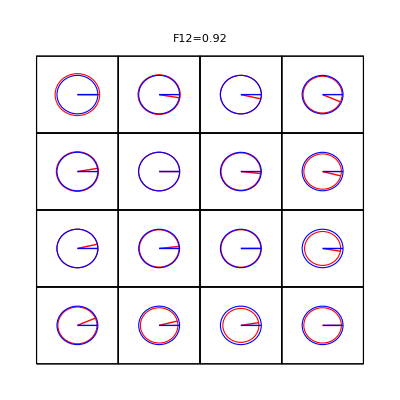
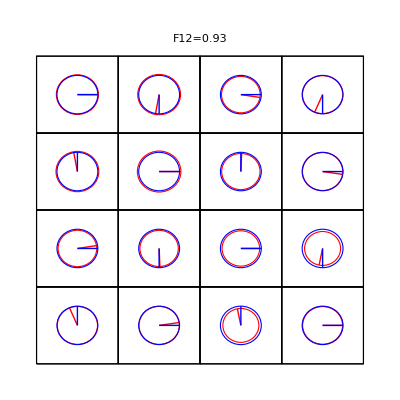
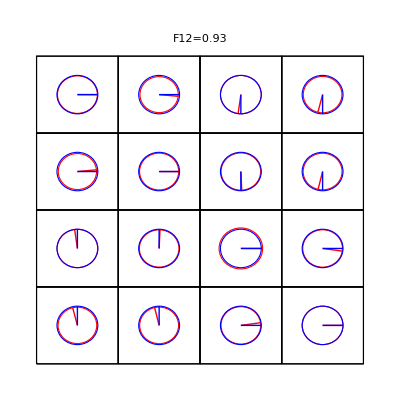
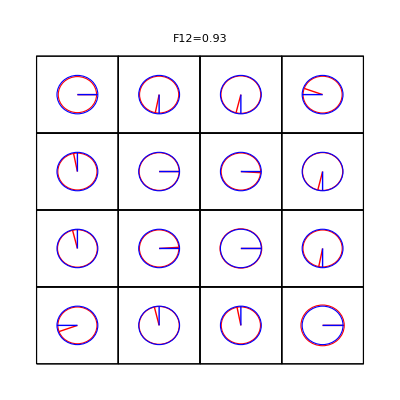
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
grListInInExp=MapThread[myCompareGraph[{#1,#2},{Red,Blue},"fidDensity"]&,{ρInListExp2, ρListIn}]
```

### Checks 1

We first check that the density matrices are physical. (Hermitian, trace =1, and positive semi definite)

```mathematica
Tr/@ρInListExp2
Tr/@ρOutListExp2
#==ConjugateTranspose[#]&/@ρInListExp2
#==ConjugateTranspose[#]&/@ρOutListExp2
Min/@((Eigenvalues/@ρInListExp2)//Chop)
Min/@((Eigenvalues/@ρOutListExp2)//Chop)
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{-0.00636543,-0.000245452,-0.0033289,-0.0127639,-0.00585642,-0.000526911,-0.00287791,-0.0187243,-0.0167967,0.00440382,0.00278068,-0.00819686,-0.00353073,-0.00365047,-0.00200067,-0.0101501}

{-0.00472654,-0.013249,-0.0083779,-0.029946,-0.00979122,0.0110854,-0.00671979,-0.000497514,-0.00526135,0.00668541,-0.0035023,-0.0138303,-0.0152858,-0.00175592,-0.00452316,-0.0176122}

The ρ's are not physical so we have to redo the caculation starting from the Pauli sets

### Import Pauli sets and recalculate non physical ρListExp3 = { ρInListExp3, ρOutListExp3 } ρ's and physical ρ's ρListExp3P = { ρInListExp3P, ρOutListExp3P }

```mathematica
opBase1NameA={"i","x","y","z"};
Clear[id,σx,σy,σz,iσy];
opBase1A={id,σx,σy,σz};
opBase2NameA=Outer[StringJoin,opBase1NameA,opBase1NameA]//Flatten
opBase2A=Outer[KroneckerProduct,opBase1A,opBase1A]//Flatten;
id={{1,0},{0,1}};
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
iσy=I σy;
σz={{1,0},{0,-1}};
opBase1A=opBase1A;
opBase2A=opBase2A;
MatrixForm/@opBase2A
```

{ii,ix,iy,iz,xi,xx,xy,xz,yi,yx,yy,yz,zi,zx,zy,zz}

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)}

We import the measured Pauli sets (readout errors corrected) and reorder each Pauli set according to the opBase2Names order

```mathematica
pauliSets=Import[pathToData<>"\\2011_04_21\\Quantum Process Tomography at 31 ns-16-spins-0.txt","Table"];
pauliSets[[1]]
set=Drop[pauliSets[[1]],3]
orderOp=Position[set,#]&/@opBase2NameA//Flatten
pauliSets=Rest[pauliSets];
Take[pauliSets[[1]],3]
Take[pauliSets[[2]],3]
Take[pauliSets[[3]],3]
Take[pauliSets[[4]],3]
pauliSets=(Drop[#,3]&/@pauliSets);
reorderPauliSet[ps_]:=ps[[#]]&/@orderOp;
pauliSets=reorderPauliSet/@pauliSets;
pauliSets=Partition[pauliSets,2];
Dimensions[pauliSets]
```

{duration,delay,state,xx,xy,xz,xi,yx,yy,yz,yi,zx,zy,zz,zi,ix,iy,iz,ii}

{xx,xy,xz,xi,yx,yy,yz,yi,zx,zy,zz,zi,ix,iy,iz,ii}

{16,13,14,15,4,1,2,3,8,5,6,7,12,9,10,11}

{31.,0.,0.}

{0.,0.,0.}

{31.,0.,1.}

{0.,0.,0.}

{16,2,16}

```mathematica
stateSet2Name={"00","01","0+","0-","10","11","1+","1-","+0","+1","++","+-","-0","-1","-+","--"}
```

{00,01,0+,0-,10,11,1+,1-,+0,+1,++,+-,-0,-1,-+,--}

We reorder the Pauli sets according to the stateSet2 order ...

```mathematica
orderState={1,2,4,3,5,6,8,7,13,14,16,15,9,10,12,11};
pauliSets2=pauliSets[[#]]&/@orderState;
{pauliSetsIn2,pauliSetsOut2}=Transpose[pauliSets2];
```

... and plot them.

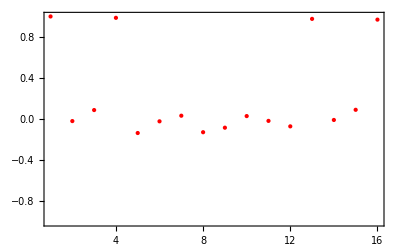
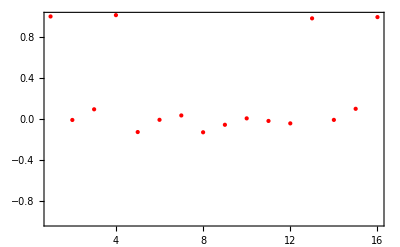
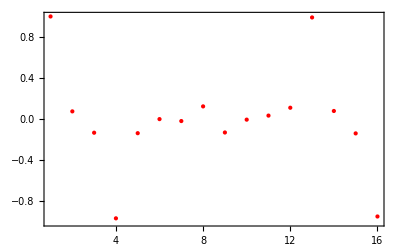
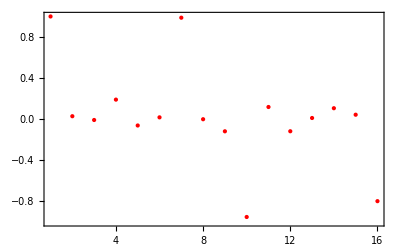
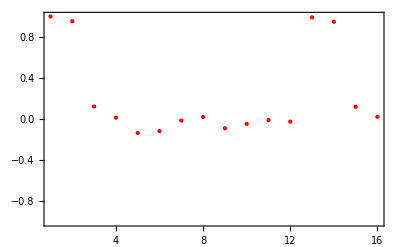
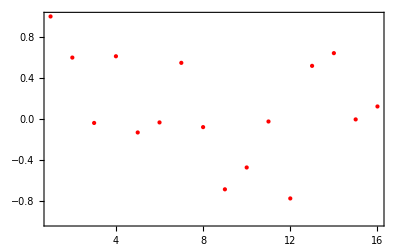
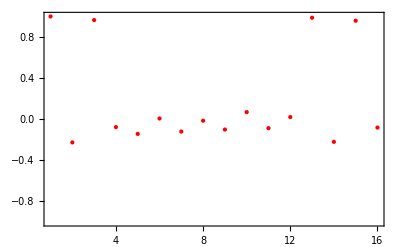
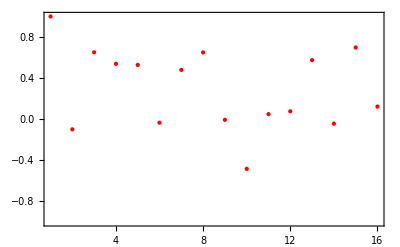

```mathematica
Map[ListPlot[#,Frame->True,PlotStyle->Red,PlotRange->{-1,1}]&,pauliSets2,{2}]//GraphicsGrid
```

Now we calculate the expectation values of the Pauli operators < Pi > = Tr(ρ.Pi) as a function of ρ: {<Pi>}=A.ρ

```mathematica
ρM1={{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}};
(ρV1=Transpose[ρM1]//Flatten)//MatrixForm
(meanValues=Tr[ρM1.#]&/@opBase2A)//MatrixForm
(matA=CoefficientArrays[meanValues,ρV1]//Normal//#[[2]]&)//MatrixForm
(matAInv=Inverse[matA])//MatrixForm
```

(ρ11
ρ21
ρ31
ρ41
ρ12
ρ22
ρ32
ρ42
ρ13
ρ23
ρ33
ρ43
ρ14
ρ24
ρ34
ρ44)

(ρ11+ρ22+ρ33+ρ44
ρ12+ρ21+ρ34+ρ43
ⅈ ρ12-ⅈ ρ21+ⅈ ρ34-ⅈ ρ43
ρ11-ρ22+ρ33-ρ44
ρ13+ρ24+ρ31+ρ42
ρ14+ρ23+ρ32+ρ41
ⅈ ρ14-ⅈ ρ23+ⅈ ρ32-ⅈ ρ41
ρ13-ρ24+ρ31-ρ42
ⅈ ρ13+ⅈ ρ24-ⅈ ρ31-ⅈ ρ42
ⅈ ρ14+ⅈ ρ23-ⅈ ρ32-ⅈ ρ41
-ρ14+ρ23+ρ32-ρ41
ⅈ ρ13-ⅈ ρ24-ⅈ ρ31+ⅈ ρ42
ρ11+ρ22-ρ33-ρ44
ρ12+ρ21-ρ34-ρ43
ⅈ ρ12-ⅈ ρ21-ⅈ ρ34+ⅈ ρ43
ρ11-ρ22-ρ33+ρ44)

(1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | -ⅈ | ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0
0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0
1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1)

(1/4 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 1/4
0 | 1/4 | ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | ⅈ/4 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 1/4 | ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | ⅈ/4 | 0 | 0 | ⅈ/4 | -1/4 | 0 | 0 | 0 | 0 | 0
0 | 1/4 | -ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | -ⅈ/4 | 0
1/4 | 0 | 0 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | -1/4
0 | 0 | 0 | 0 | 0 | 1/4 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | -1/4 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 1/4 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | ⅈ/4 | 0 | 0 | -ⅈ/4 | 1/4 | 0 | 0 | 0 | 0 | 0
1/4 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | 0 | 0 | -1/4
0 | 1/4 | ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | -ⅈ/4 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | -ⅈ/4 | 0 | 0 | -ⅈ/4 | -1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | -1/4 | -ⅈ/4 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0
0 | 1/4 | -ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | ⅈ/4 | 0
1/4 | 0 | 0 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | 0 | 0 | 1/4)

Finally we calculate the density matrices ρ by linear inversion  ρ = A^-1{<Pi>}...

```mathematica
ρFromPauliSet=Chop[Transpose[Partition[matAInv.#,4]]]&;
ρListExp3={ρInListExp3,ρOutListExp3}={ρFromPauliSet/@pauliSetsIn2,ρFromPauliSet/@pauliSetsOut2};
ρL1=Transpose[ρListExp3];
ρL1//Dimensions
```

{16,2,4,4}

... and compare them with ρListExp2: The phases are correct without conjugating but  there are small discrepencies (??) : 3rd input matrix ?

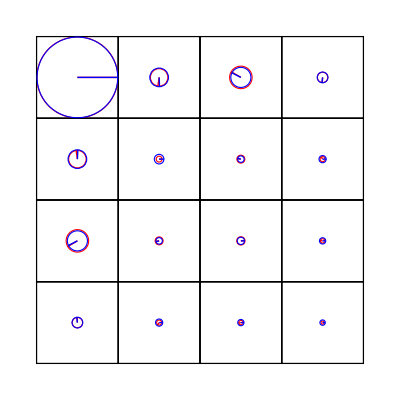
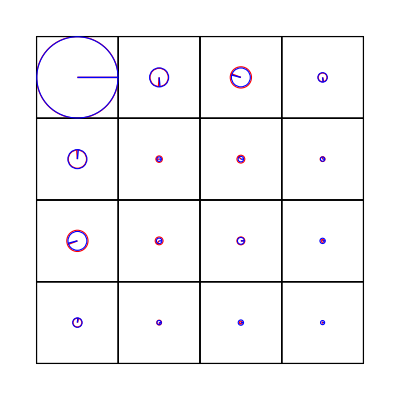
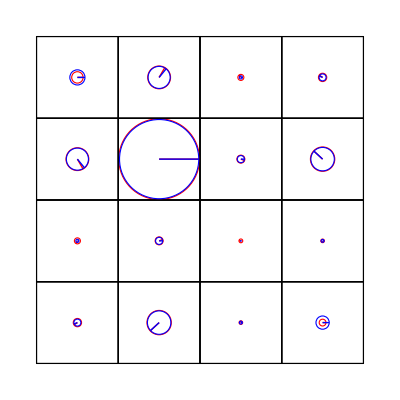
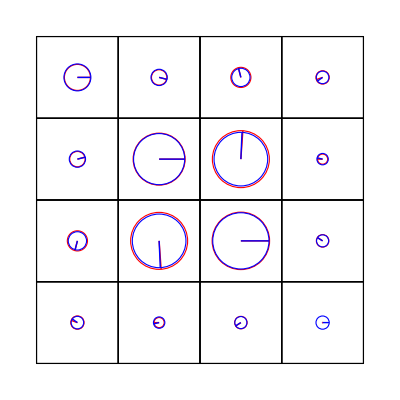
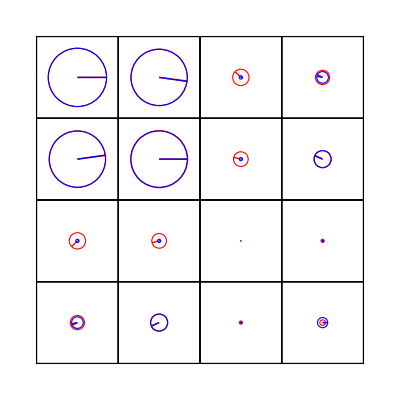
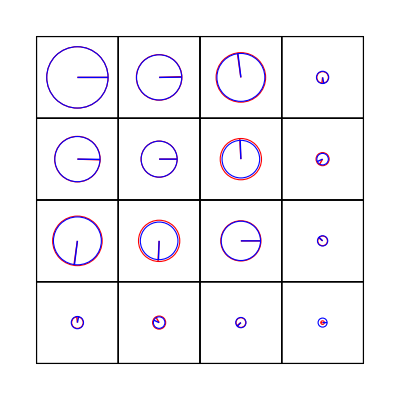
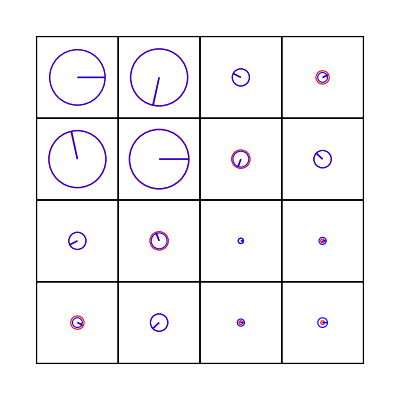
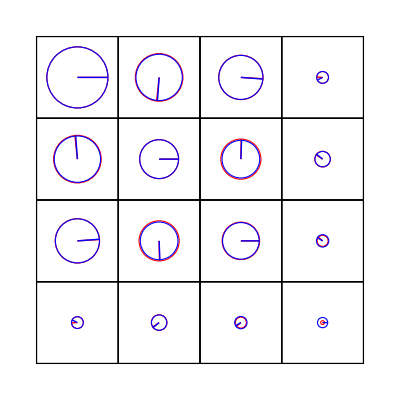

```mathematica
GraphicsGrid[MapThread[myCompareGraph[{#1,#2},{Red,Blue}]&,{ρL1,Transpose[ρListExp2]},2]]
```

Although these ρ's are Hermitian and have a trace 1, they are non physical because they are not positive (all eigenvalues positive)

```mathematica
Map[Max[Flatten[Chop[#-ConjugateTranspose[#]]]]&,ρL1,{2}]
Map[Tr,ρL1,{2}]//Chop
Map[Min[Chop[Eigenvalues[#]]]&,ρL1,{2}]//Chop
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

{{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.}}

{{-0.00757325,-0.0156842},{-0.00636662,-0.0485723},{-0.00843647,-0.0427148},{-0.0119629,-0.0476008},{-0.0127045,-0.0378065},{-0.00761845,0.0139868},{-0.00383887,-0.0184237},{-0.0101643,-0.0193506},{-0.0178248,-0.0191363},{-0.00400162,0.000728385},{-0.00271119,-0.022725},{-0.0116596,-0.0245823},{-0.00730792,-0.0363963},{0.00220394,-0.0129208},{-0.0062016,-0.015054},{-0.00951787,-0.0243344}}

Let us make them physical by minimization of the distance ( Hilbert-Schmitt norm) between each non physical matrices and physical matrices

```mathematica
Remove[d2Num,ρPofρ,ρM2,ρRealL,bestρPofρ]
```

```mathematica
d2Num[m1_/;And @@ (NumberQ/@Flatten[m1]),m2_/;And @@ (NumberQ/@Flatten[m2])]:=Plus@@(m2-m1//Flatten//Chop//Abs//#^2&)
```

```mathematica
ρPofρ[ρ_/;And @@ (NumberQ/@Flatten[ρ])]:=Block[{val,vec},
{val,vec}=Eigensystem[ρ]//Chop[#,10^-6]&//Transpose//Sort//Reverse//Transpose;
val=Max[#,0]&/@val;val=val/Plus@@val;
Chop[Transpose[vec].DiagonalMatrix[val].Conjugate[vec],10^-6]
];
```

```mathematica
ρM2=Table[ρ0[i,j],{i,1,4},{j,1,4}];
ρRealL=MapIndexed[Take[#1,#2[[1]]]&,ρM2,1]//Flatten;
(ρM2=ρM2//.{ρ0[i_,j_]/;j>i->Conjugate[ρ0[j,i]],ρ0[i_,j_]/;j<i->reρ0[i,j]+I imρ0[i,j]}//ComplexExpand)//MatrixForm
ρRealL=ρRealL/.ρ0[i_,j_]/;j≠i->Sequence[reρ0[i,j],imρ0[i,j]]//ComplexExpand
```

(ρ0[1,1] | -ⅈ imρ0[2,1]+reρ0[2,1] | -ⅈ imρ0[3,1]+reρ0[3,1] | -ⅈ imρ0[4,1]+reρ0[4,1]
ⅈ imρ0[2,1]+reρ0[2,1] | ρ0[2,2] | -ⅈ imρ0[3,2]+reρ0[3,2] | -ⅈ imρ0[4,2]+reρ0[4,2]
ⅈ imρ0[3,1]+reρ0[3,1] | ⅈ imρ0[3,2]+reρ0[3,2] | ρ0[3,3] | -ⅈ imρ0[4,3]+reρ0[4,3]
ⅈ imρ0[4,1]+reρ0[4,1] | ⅈ imρ0[4,2]+reρ0[4,2] | ⅈ imρ0[4,3]+reρ0[4,3] | ρ0[4,4])

{ρ0[1,1],reρ0[2,1],imρ0[2,1],ρ0[2,2],reρ0[3,1],imρ0[3,1],reρ0[3,2],imρ0[3,2],ρ0[3,3],reρ0[4,1],imρ0[4,1],reρ0[4,2],imρ0[4,2],reρ0[4,3],imρ0[4,3],ρ0[4,4]}

```mathematica
ρRealLofρ[ρm_]=ρRealL/.{ρ0[i_,j_]->ρm[[i,j]],reρ0[i_,j_]->Re[ρm[[i,j]]],imρ0[i_,j_]->Im[ρm[[i,j]]]}
```

Part::pspec: Part specification i is neither an integer nor a list of integers.

General::stop: Further output of Part will be suppressed during this calculation.

Part::partd: Part specification ρm ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification ρm ⟦ 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

{ρm⟦1,1⟧,Re[ρm⟦2,1⟧],Im[ρm⟦2,1⟧],ρm⟦2,2⟧,Re[ρm⟦3,1⟧],Im[ρm⟦3,1⟧],Re[ρm⟦3,2⟧],Im[ρm⟦3,2⟧],ρm⟦3,3⟧,Re[ρm⟦4,1⟧],Im[ρm⟦4,1⟧],Re[ρm⟦4,2⟧],Im[ρm⟦4,2⟧],Re[ρm⟦4,3⟧],Im[ρm⟦4,3⟧],ρm⟦4,4⟧}

```mathematica
ρofρRealL[ρReal_]=ρM2/.{
ρ0[i_,j_]:>ρReal[[Flatten[Position[ρRealL,ρ0[i,j]]][[-1]]]],
reρ0[i_,j_]:>ρReal[[Flatten[Position[ρRealL,reρ0[i,j]]][[-1]]]],
imρ0[i_,j_]:>ρReal[[Flatten[Position[ρRealL,imρ0[i,j]]][[-1]]]]}
```

Part::partd: Part specification ρReal ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification ρReal ⟦ 3 ⟧ is longer than depth of object.

Part::partd: Part specification ρReal ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

{{ρReal⟦1⟧,ρReal⟦2⟧-ⅈ ρReal⟦3⟧,ρReal⟦5⟧-ⅈ ρReal⟦6⟧,ρReal⟦10⟧-ⅈ ρReal⟦11⟧},{ρReal⟦2⟧+ⅈ ρReal⟦3⟧,ρReal⟦4⟧,ρReal⟦7⟧-ⅈ ρReal⟦8⟧,ρReal⟦12⟧-ⅈ ρReal⟦13⟧},{ρReal⟦5⟧+ⅈ ρReal⟦6⟧,ρReal⟦7⟧+ⅈ ρReal⟦8⟧,ρReal⟦9⟧,ρReal⟦14⟧-ⅈ ρReal⟦15⟧},{ρReal⟦10⟧+ⅈ ρReal⟦11⟧,ρReal⟦12⟧+ⅈ ρReal⟦13⟧,ρReal⟦14⟧+ⅈ ρReal⟦15⟧,ρReal⟦16⟧}}

```mathematica
bestρPofρ[ρm_/;And @@ (NumberQ/@Flatten[ρm]),showProgress_:False]:=Block[{a=If[showProgress,Print["Start minimization"]],sol=FindMinimum[d=d2Num[ρPofρ[ρofρRealL[ρRealL]],ρm],Evaluate[Transpose[{ρRealL,ρRealLofρ[ρm]}]],StepMonitor:>If[showProgress,Print[d],None]]},ρPofρ[ρofρRealL[ρRealL/.sol[[2]]]]]
```

```mathematica
ρL1P=Map[bestρPofρ,ρL1,{2}];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[False].

General::stop: Further output of Flatten will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

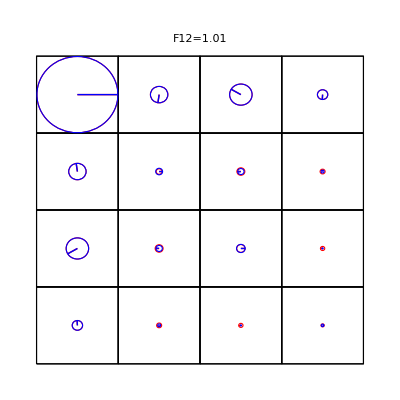
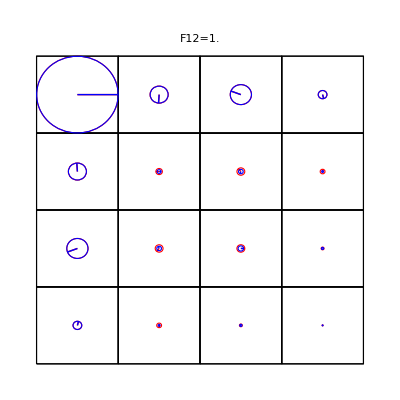
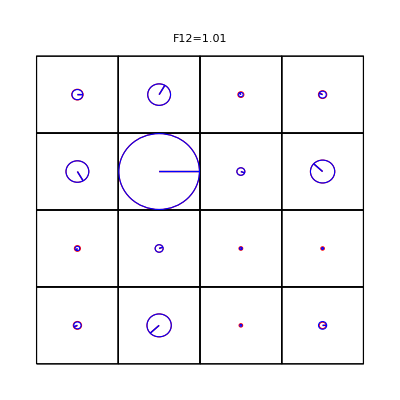
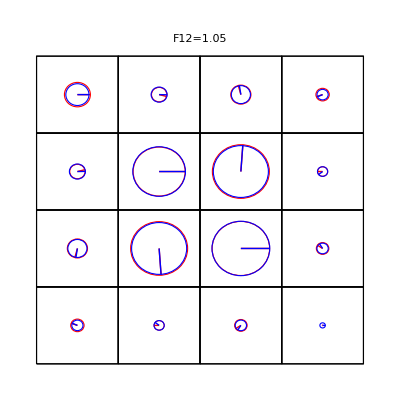
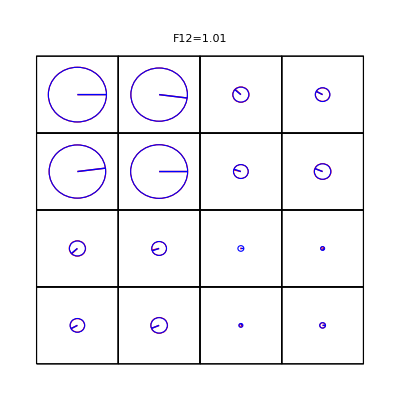
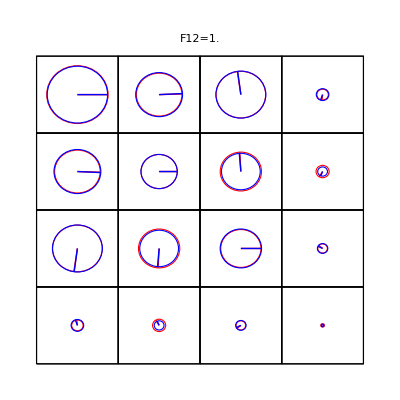
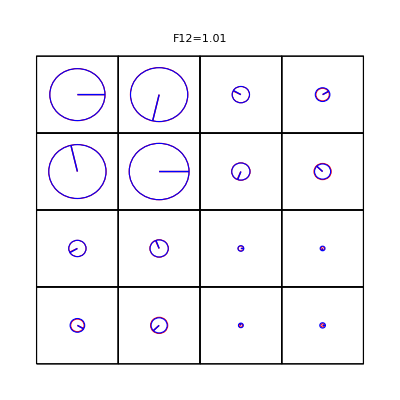
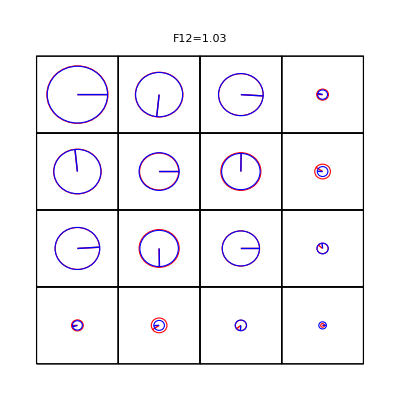

```mathematica
MapThread[myCompareGraph[{#1,#2},{Red,Blue},"fidDensity"]&,{ρL1,ρL1P},2]
```

Now the ρ's are physical:

```mathematica
Map[Max[Flatten[Chop[#-ConjugateTranspose[#]]]]&,ρL1P,{2}]
Map[Tr,ρL1P,{2}]//Chop
Map[Min[Chop[Eigenvalues[#]]]&,ρL1P,{2}]//Chop
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

{{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.}}

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0.0139868},{0,0},{0,0},{0,0},{0,0.000728385},{0,0},{0,0},{0,0},{0.00220394,0},{0,0},{0,0}}

We introduce ρInListExp3P and ρOutListExp3P

```mathematica
ρListExp3P={ρInListExp3P,ρOutListExp3P}=Transpose[ρL1P];
```

### Checks 2

Then we compare also the experimental ρout's with  U ρ_(in exp) U^† and   U ρ_(in ideal) U^†

```mathematica
ρOutList0=Chop[uS.#.uST]&/@ρListIn;
ρOutList1=Chop[uS.#.uST]&/@ρInListExp2;
```

```mathematica
grListOut0OutExp=MapThread[myCompareGraph[{#1,#2},{Red,Blue},"fidDensity"]&,{ρOutListExp2,ρOutList0}];
grListOut1OutExp=MapThread[myCompareGraph[{#1,#2},{Red,Blue},"fidDensity"]&,{ρOutListExp2,ρOutList1}];
```

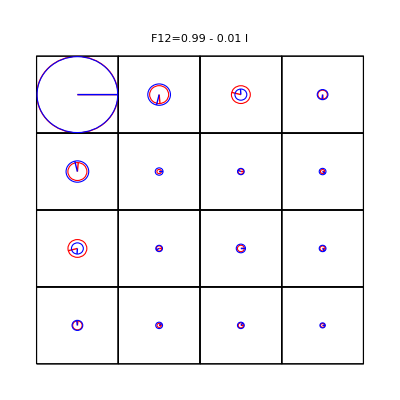
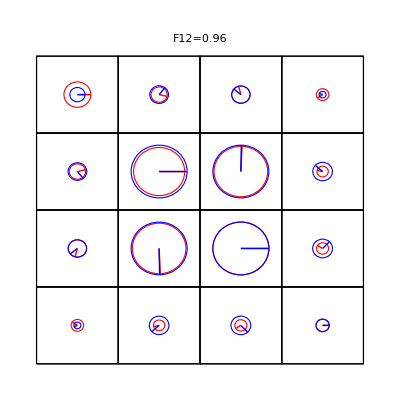
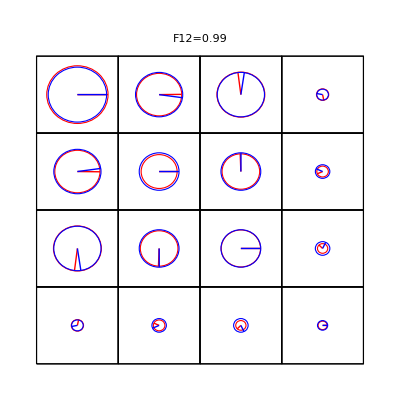
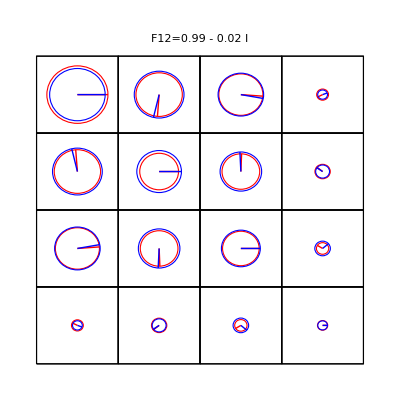
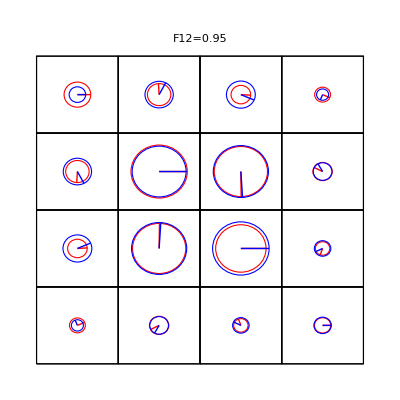
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
GraphicsGrid[{grListInInExp,grListOut0OutExp,grListOut1OutExp}//Transpose]
```

We observe that output fidelities are sytematically better for the ideal operator operated on the experimental input ρ's than on the ideal ones. So the errors on the preparation are not negligible and we use the experimentally determined ρin's to characterize the process.

```mathematica
fidelityRatios=Re[MapThread[fidDensity,{ρOutListExp2,ρOutList1}]]/Re[MapThread[fidDensity,{ρOutListExp2,ρOutList0}]]
```

{1.00439,1.11284,1.03869,1.0697,1.11576,1.2153,1.17746,1.05101,1.06523,1.16657,1.10266,1.09375,1.0614,1.11001,1.09476,1.11691}

### Calculate process map from the experimental data: (λExp1,χExp1) and (λExp1P,χExp1P) from non physical and physical ρ's (but both λ are non physical)

We want to find the λ matrix made of the ρout columns that correspond to the ρin's of ρBase2 ( ρout = ∑_(j, k)  λ_(j,k) ρ_in ) starting from the ρout's of the ρin's in ρInExp.
For that purpose, we decompose ρBase2 in the experimental ρin's by inversion of the ρinExp -> ρBase2 passage matrix P made of the ρinExp columns.
Then we compute the images of the ρBase2 vectors as λ= [ρoutExp]. P^-1 with [ρoutExp] the matrix made of the ρoutExp column vectors.
Note that this λ matrix can be non physical due to experimental uncertainties.
Then we calculate the chi matrix χ =β^-1. Flatten[λ] and the Kraus operators K_i = √λ_iV_i with λ_i and V_i the eignevalues and vectors of χ reexpressed in the ketBase2 x braBase2 operator basis

```mathematica
passageP=Composition[Flatten,ρToVect]/@ρInListExp2//Transpose;
ρVectOutListExp2=Composition[Flatten,ρToVect]/@ρOutListExp2//Transpose;;
inversePassageP=Inverse[passageP];
λExp1=ρVectOutListExp2.inversePassageP;
Print["λ matrix ="]
myCompareGraph[{λExp1,λIdeal}]
```

λ matrix =

-Graphics-

```mathematica
passagePP=Composition[Flatten,ρToVect]/@ρInListExp3P//Transpose;
ρVectOutListExp2P=Composition[Flatten,ρToVect]/@ρOutListExp3P//Transpose;;
inversePassagePP=Inverse[passagePP];
λExp1P=ρVectOutListExp2P.inversePassagePP;
Print["λP matrix ="]
myCompareGraph[{λExp1P,λIdeal}]
```

λP matrix =

-Graphics-

The theoretical λ matrix is symmetric but not the raw experimental one (process is non physical even with physical ρ's).

```mathematica
λExp1-Transpose[λExp1]//Chop//Flatten//Abs//Max
λExp1P-Transpose[λExp1P]//Chop//Flatten//Abs//Max
```

0.144549

0.148338

```mathematica
χExp1=βMatrixInv.Flatten[λExp1]//Partition[#,16]&//Chop;
Print["χExp1 matrix ="];
 myCompareGraph[{χExp1,χIdeal1},{Red,Blue},"fidChi"]
```

χExp1 matrix =

-Graphics-

```mathematica
χExp1P=βMatrixInv.Flatten[λExp1P]//Partition[#,16]&//Chop;
Print["χexp1P matrix ="];
 myCompareGraph[{χExp1P,χIdeal1},{Red,Blue},"fidChi"]
```

χexp1P matrix =

-Graphics-

χ is hermitian but has non positive eigenvalues and is thus non completely positive and consequently non physical.

```mathematica
χExp1-ConjugateTranspose[χExp1]//Chop//Flatten//Max
eigSysχExp={eigValχExp,eigVecχExp}=
Block[
{val,vect},
{val,vect}=Eigensystem[χExp1]//Chop;
{val,vect}//Transpose//Sort//Reverse//Transpose
];
eigValχExp
```

0

{0.933415,0.0892017,0.0601139,0.0518337,0.0457988,0.0245008,0.0175908,0.00636695,0.00119562,-0.00631353,-0.0103809,-0.0161994,-0.0239304,-0.0318341,-0.0612988,-0.08006}

```mathematica
χExp1P-ConjugateTranspose[χExp1P]//Chop//Flatten//Max
eigSysχExpP={eigValχExpP,eigVecχExpP}=
Block[
{val,vect},
{val,vect}=Eigensystem[χExp1P]//Chop;
{val,vect}//Transpose//Sort//Reverse//Transpose
];
eigValχExpP
```

0

{0.938723,0.0751016,0.0594422,0.0467395,0.0377895,0.02114,0.0160824,0.00623914,-0.000757295,-0.00366083,-0.0120615,-0.0132745,-0.0191414,-0.0322807,-0.054937,-0.0651445}

We finally calculate the Kraus operators corresponding to the χ eigenvalues and vectors

```mathematica
myOpts1
```

{functionForArrowLength→(√Abs[#1]&),fill2DShape→False}

```mathematica
eigValχExp
Norm/@eigVecχExp
eigOpχExp=(Plus@@ (#opBase2))&/@eigVecχExp;
krausOpExp=MapThread[#1#2&,{Sqrt[eigValχExp],eigOpχExp}];
complexMatrixDraw[uS,myOpts1~Join~{borderDirectives->{Blue,Thickness[0.001]},arrowDirectives->{Blue,Thickness[0.001],Arrowheads[0]}}]
complexMatrixDraw[#,myOpts1~Join~{borderDirectives->{Red,Thickness[0.001]},arrowDirectives->{Red,Thickness[0.001],Arrowheads[0]}}]&/@krausOpExp
```

{0.933415,0.0892017,0.0601139,0.0518337,0.0457988,0.0245008,0.0175908,0.00636695,0.00119562,-0.00631353,-0.0103809,-0.0161994,-0.0239304,-0.0318341,-0.0612988,-0.08006}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### analysis of the systematic preparation and tomographic pulse errors

Despite fidelities close to 1, we notice large spurious matrix elements in the input ρ's. So we suspect large pulse errors, which we try to determine.

```mathematica
myCompareGraph[{ρInListExp3[[1]],ρListIn[[1]]},{Red,Blue},"fidDensity"]
```

-Graphics-

```mathematica
opBase2NameA
```

{ii,ix,iy,iz,xi,xx,xy,xz,yi,yx,yy,yz,zi,zx,zy,zz}

We assume the following systematic errors:  
	- " π rotation" around of  π+ϵπx  with different ϵπx for qubit 1 and 2;
	- " π/2 rotation" of  π/2 + ϵhπ with different ϵhπ for qubit 1 and 2  and for x and y axis ;
	- y axis making 90°+ θy with x axis, with different θy for qubit 1 and 2;
	- x-y frame at tomography rotated by θt with respect to x-y frame at preparation,  with different θt for qubit 1 and 2.
As a consequence :	
	- instead of preparing the states of setState1 we prepare other states with errors
	-instead of measuring the expectation values of  opBase1, we measure those of opBase1E with errors

Instead of preparing  single qubit states stateSet1={ |0>, |1>,  |+> = |0> + |1>,  |-> = |0> + i |1>} and the tensorial product stateSet2=stateSet1x2 and corresponding density matrices ρListIn, we actually prepare ρListInE.
We check that ρListInE=ρListIn when all errors are zeroed.

```mathematica
Clear[id,rx1,ry1,rx2,ry2]
opSet1E1={id,rx1[π],ry1[π/2],rx1[-π/2]};
opSet1E2={id,rx2[π],ry2[π/2],rx2[-π/2]};
opE2=Outer[KroneckerProduct,opSet1E1,opSet1E2]//Flatten;
id={{1,0},{0,1}};
rx1[π]=MatrixExp[- I (π+ϵπx1Prep)/2 σx];
rx2[π]=MatrixExp[- I (π+ϵπx2Prep)/2 σx];
rx1[-π/2]=MatrixExp[ I( π/2+ϵhπx1Prep)/2 σx];
rx2[-π/2]=MatrixExp[ I( π/2+ϵhπx2Prep)/2 σx];
ry1[π/2]=MatrixExp[- I( π/2+ϵhπy1Prep)/2 (Cos[θy1]σy-Sin[θy1]σx)];
ry2[π/2]=MatrixExp[- I (π/2+ϵhπy2Prep)/2 (Cos[θy2]σy-Sin[θy2]σx)];
opE2=opE2;
ρListInE=#.ρListIn[[1]].ConjugateTranspose[#]&/@opE2//FullSimplify//ComplexExpand//FullSimplify;
noErrorRule={ϵπx1Prep->0,ϵπx2Prep->0,ϵhπx1Prep->0, ϵhπx2Prep->0,ϵhπy1Prep->0, ϵhπy2Prep->0,θy1->0,θy2->0};
ρListInNoE=ρListInE/.noErrorRule;
(ρListIn-ρListInNoE//Flatten//Max)==0
"ρListInE="
MatrixForm/@ρListInE
```

True

ρListInE=

{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(Sin[ϵπx2Prep/2]^2 | -1/2 ⅈ Sin[ϵπx2Prep] | 0 | 0
1/2 ⅈ Sin[ϵπx2Prep] | Cos[ϵπx2Prep/2]^2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1/2 (1-Sin[ϵhπy2Prep]) | 1/2 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] | 0 | 0
1/2 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] | 1/2 (1+Sin[ϵhπy2Prep]) | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(Cos[1/4 (π+2 ϵhπx2Prep)]^2 | -1/2 ⅈ Cos[ϵhπx2Prep] | 0 | 0
1/2 ⅈ Cos[ϵhπx2Prep] | Sin[1/4 (π+2 ϵhπx2Prep)]^2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(Sin[ϵπx1Prep/2]^2 | 0 | -1/2 ⅈ Sin[ϵπx1Prep] | 0
0 | 0 | 0 | 0
1/2 ⅈ Sin[ϵπx1Prep] | 0 | Cos[ϵπx1Prep/2]^2 | 0
0 | 0 | 0 | 0),(Sin[ϵπx1Prep/2]^2 Sin[ϵπx2Prep/2]^2 | -1/2 ⅈ Sin[ϵπx1Prep/2]^2 Sin[ϵπx2Prep] | -1/2 ⅈ Sin[ϵπx1Prep] Sin[ϵπx2Prep/2]^2 | -1/4 Sin[ϵπx1Prep] Sin[ϵπx2Prep]
1/2 ⅈ Sin[ϵπx1Prep/2]^2 Sin[ϵπx2Prep] | Cos[ϵπx2Prep/2]^2 Sin[ϵπx1Prep/2]^2 | 1/4 Sin[ϵπx1Prep] Sin[ϵπx2Prep] | -1/2 ⅈ Cos[ϵπx2Prep/2]^2 Sin[ϵπx1Prep]
1/2 ⅈ Sin[ϵπx1Prep] Sin[ϵπx2Prep/2]^2 | 1/4 Sin[ϵπx1Prep] Sin[ϵπx2Prep] | Cos[ϵπx1Prep/2]^2 Sin[ϵπx2Prep/2]^2 | -1/2 ⅈ Cos[ϵπx1Prep/2]^2 Sin[ϵπx2Prep]
-1/4 Sin[ϵπx1Prep] Sin[ϵπx2Prep] | 1/2 ⅈ Cos[ϵπx2Prep/2]^2 Sin[ϵπx1Prep] | 1/2 ⅈ Cos[ϵπx1Prep/2]^2 Sin[ϵπx2Prep] | Cos[ϵπx1Prep/2]^2 Cos[ϵπx2Prep/2]^2),(-1/2 (-1+Sin[ϵhπy2Prep]) Sin[ϵπx1Prep/2]^2 | 1/2 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] Sin[ϵπx1Prep/2]^2 | 1/4 ⅈ (-1+Sin[ϵhπy2Prep]) Sin[ϵπx1Prep] | -1/4 ⅈ ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] Sin[ϵπx1Prep]
1/2 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] Sin[ϵπx1Prep/2]^2 | 1/2 (1+Sin[ϵhπy2Prep]) Sin[ϵπx1Prep/2]^2 | 1/4 Cos[ϵhπy2Prep] Sin[ϵπx1Prep] (-ⅈ Cos[θy2]+Sin[θy2]) | -1/4 ⅈ (1+Sin[ϵhπy2Prep]) Sin[ϵπx1Prep]
-1/4 ⅈ (-1+Sin[ϵhπy2Prep]) Sin[ϵπx1Prep] | 1/4 Cos[ϵhπy2Prep] Sin[ϵπx1Prep] (ⅈ Cos[θy2]+Sin[θy2]) | -1/2 Cos[ϵπx1Prep/2]^2 (-1+Sin[ϵhπy2Prep]) | 1/2 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] Cos[ϵπx1Prep/2]^2
1/4 ⅈ ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] Sin[ϵπx1Prep] | 1/4 ⅈ (1+Sin[ϵhπy2Prep]) Sin[ϵπx1Prep] | 1/2 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] Cos[ϵπx1Prep/2]^2 | 1/4 (1+Cos[ϵπx1Prep]) (1+Sin[ϵhπy2Prep])),(Cos[1/4 (π+2 ϵhπx2Prep)]^2 Sin[ϵπx1Prep/2]^2 | -1/2 ⅈ Cos[ϵhπx2Prep] Sin[ϵπx1Prep/2]^2 | 1/4 ⅈ (-1+Sin[ϵhπx2Prep]) Sin[ϵπx1Prep] | -1/4 Cos[ϵhπx2Prep] Sin[ϵπx1Prep]
1/2 ⅈ Cos[ϵhπx2Prep] Sin[ϵπx1Prep/2]^2 | Sin[1/4 (π+2 ϵhπx2Prep)]^2 Sin[ϵπx1Prep/2]^2 | 1/4 Cos[ϵhπx2Prep] Sin[ϵπx1Prep] | -1/2 ⅈ Sin[1/4 (π+2 ϵhπx2Prep)]^2 Sin[ϵπx1Prep]
-1/4 ⅈ (-1+Sin[ϵhπx2Prep]) Sin[ϵπx1Prep] | 1/4 Cos[ϵhπx2Prep] Sin[ϵπx1Prep] | Cos[1/4 (π+2 ϵhπx2Prep)]^2 Cos[ϵπx1Prep/2]^2 | -1/2 ⅈ Cos[ϵhπx2Prep] Cos[ϵπx1Prep/2]^2
-1/4 Cos[ϵhπx2Prep] Sin[ϵπx1Prep] | 1/2 ⅈ Sin[1/4 (π+2 ϵhπx2Prep)]^2 Sin[ϵπx1Prep] | 1/2 ⅈ Cos[ϵhπx2Prep] Cos[ϵπx1Prep/2]^2 | Cos[ϵπx1Prep/2]^2 Sin[1/4 (π+2 ϵhπx2Prep)]^2),(1/2 (1-Sin[ϵhπy1Prep]) | 0 | 1/2 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] | 0
0 | 0 | 0 | 0
1/2 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] | 0 | 1/2 (1+Sin[ϵhπy1Prep]) | 0
0 | 0 | 0 | 0),(-1/2 (-1+Sin[ϵhπy1Prep]) Sin[ϵπx2Prep/2]^2 | 1/4 ⅈ (-1+Sin[ϵhπy1Prep]) Sin[ϵπx2Prep] | 1/2 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] Sin[ϵπx2Prep/2]^2 | -1/4 ⅈ ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] Sin[ϵπx2Prep]
-1/4 ⅈ (-1+Sin[ϵhπy1Prep]) Sin[ϵπx2Prep] | -1/2 Cos[ϵπx2Prep/2]^2 (-1+Sin[ϵhπy1Prep]) | 1/4 Cos[ϵhπy1Prep] Sin[ϵπx2Prep] (ⅈ Cos[θy1]+Sin[θy1]) | 1/2 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] Cos[ϵπx2Prep/2]^2
1/2 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] Sin[ϵπx2Prep/2]^2 | 1/4 Cos[ϵhπy1Prep] Sin[ϵπx2Prep] (-ⅈ Cos[θy1]+Sin[θy1]) | 1/2 (1+Sin[ϵhπy1Prep]) Sin[ϵπx2Prep/2]^2 | -1/4 ⅈ (1+Sin[ϵhπy1Prep]) Sin[ϵπx2Prep]
1/4 ⅈ ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] Sin[ϵπx2Prep] | 1/2 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] Cos[ϵπx2Prep/2]^2 | 1/4 ⅈ (1+Sin[ϵhπy1Prep]) Sin[ϵπx2Prep] | 1/4 (1+Cos[ϵπx2Prep]) (1+Sin[ϵhπy1Prep])),(1/4 (-1+Sin[ϵhπy1Prep]) (-1+Sin[ϵhπy2Prep]) | -1/4 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] (-1+Sin[ϵhπy1Prep]) | -1/4 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] (-1+Sin[ϵhπy2Prep]) | 1/4 Cos[ϵhπy1Prep] Cos[ϵhπy2Prep] (Cos[θy1+θy2]-ⅈ Sin[θy1+θy2])
-1/4 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] (-1+Sin[ϵhπy1Prep]) | -1/4 (-1+Sin[ϵhπy1Prep]) (1+Sin[ϵhπy2Prep]) | 1/4 ⅇ^(-ⅈ (θy1-θy2)) Cos[ϵhπy1Prep] Cos[ϵhπy2Prep] | 1/4 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] (1+Sin[ϵhπy2Prep])
-1/4 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] (-1+Sin[ϵhπy2Prep]) | 1/4 ⅇ^(ⅈ (θy1-θy2)) Cos[ϵhπy1Prep] Cos[ϵhπy2Prep] | -1/4 (1+Sin[ϵhπy1Prep]) (-1+Sin[ϵhπy2Prep]) | 1/4 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] (1+Sin[ϵhπy1Prep])
1/4 Cos[ϵhπy1Prep] Cos[ϵhπy2Prep] (Cos[θy1+θy2]+ⅈ Sin[θy1+θy2]) | 1/4 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] (1+Sin[ϵhπy2Prep]) | 1/4 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] (1+Sin[ϵhπy1Prep]) | 1/4 (1+Sin[ϵhπy1Prep]) (1+Sin[ϵhπy2Prep])),(1/4 (-1+Sin[ϵhπx2Prep]) (-1+Sin[ϵhπy1Prep]) | 1/4 ⅈ Cos[ϵhπx2Prep] (-1+Sin[ϵhπy1Prep]) | -1/4 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] (-1+Sin[ϵhπx2Prep]) | -1/4 ⅈ ⅇ^(-ⅈ θy1) Cos[ϵhπx2Prep] Cos[ϵhπy1Prep]
-1/4 ⅈ Cos[ϵhπx2Prep] (-1+Sin[ϵhπy1Prep]) | -1/4 (1+Sin[ϵhπx2Prep]) (-1+Sin[ϵhπy1Prep]) | 1/4 Cos[ϵhπx2Prep] Cos[ϵhπy1Prep] (ⅈ Cos[θy1]+Sin[θy1]) | 1/4 ⅇ^(-ⅈ θy1) Cos[ϵhπy1Prep] (1+Sin[ϵhπx2Prep])
-1/4 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] (-1+Sin[ϵhπx2Prep]) | 1/4 Cos[ϵhπx2Prep] Cos[ϵhπy1Prep] (-ⅈ Cos[θy1]+Sin[θy1]) | -1/4 (-1+Sin[ϵhπx2Prep]) (1+Sin[ϵhπy1Prep]) | -1/4 ⅈ Cos[ϵhπx2Prep] (1+Sin[ϵhπy1Prep])
1/4 ⅈ ⅇ^(ⅈ θy1) Cos[ϵhπx2Prep] Cos[ϵhπy1Prep] | 1/4 ⅇ^(ⅈ θy1) Cos[ϵhπy1Prep] (1+Sin[ϵhπx2Prep]) | 1/4 ⅈ Cos[ϵhπx2Prep] (1+Sin[ϵhπy1Prep]) | 1/4 (1+Sin[ϵhπx2Prep]) (1+Sin[ϵhπy1Prep])),(Cos[1/4 (π+2 ϵhπx1Prep)]^2 | 0 | -1/2 ⅈ Cos[ϵhπx1Prep] | 0
0 | 0 | 0 | 0
1/2 ⅈ Cos[ϵhπx1Prep] | 0 | Sin[1/4 (π+2 ϵhπx1Prep)]^2 | 0
0 | 0 | 0 | 0),(Cos[1/4 (π+2 ϵhπx1Prep)]^2 Sin[ϵπx2Prep/2]^2 | 1/4 ⅈ (-1+Sin[ϵhπx1Prep]) Sin[ϵπx2Prep] | -1/2 ⅈ Cos[ϵhπx1Prep] Sin[ϵπx2Prep/2]^2 | -1/4 Cos[ϵhπx1Prep] Sin[ϵπx2Prep]
-1/4 ⅈ (-1+Sin[ϵhπx1Prep]) Sin[ϵπx2Prep] | Cos[1/4 (π+2 ϵhπx1Prep)]^2 Cos[ϵπx2Prep/2]^2 | 1/4 Cos[ϵhπx1Prep] Sin[ϵπx2Prep] | -1/2 ⅈ Cos[ϵhπx1Prep] Cos[ϵπx2Prep/2]^2
1/2 ⅈ Cos[ϵhπx1Prep] Sin[ϵπx2Prep/2]^2 | 1/4 Cos[ϵhπx1Prep] Sin[ϵπx2Prep] | Sin[1/4 (π+2 ϵhπx1Prep)]^2 Sin[ϵπx2Prep/2]^2 | -1/2 ⅈ Sin[1/4 (π+2 ϵhπx1Prep)]^2 Sin[ϵπx2Prep]
-1/4 Cos[ϵhπx1Prep] Sin[ϵπx2Prep] | 1/2 ⅈ Cos[ϵhπx1Prep] Cos[ϵπx2Prep/2]^2 | 1/2 ⅈ Sin[1/4 (π+2 ϵhπx1Prep)]^2 Sin[ϵπx2Prep] | Cos[ϵπx2Prep/2]^2 Sin[1/4 (π+2 ϵhπx1Prep)]^2),(1/4 (-1+Sin[ϵhπx1Prep]) (-1+Sin[ϵhπy2Prep]) | -1/4 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] (-1+Sin[ϵhπx1Prep]) | 1/4 ⅈ Cos[ϵhπx1Prep] (-1+Sin[ϵhπy2Prep]) | -1/4 ⅈ ⅇ^(-ⅈ θy2) Cos[ϵhπx1Prep] Cos[ϵhπy2Prep]
-1/4 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] (-1+Sin[ϵhπx1Prep]) | -1/4 (-1+Sin[ϵhπx1Prep]) (1+Sin[ϵhπy2Prep]) | 1/4 Cos[ϵhπx1Prep] Cos[ϵhπy2Prep] (-ⅈ Cos[θy2]+Sin[θy2]) | -1/4 ⅈ Cos[ϵhπx1Prep] (1+Sin[ϵhπy2Prep])
-1/4 ⅈ Cos[ϵhπx1Prep] (-1+Sin[ϵhπy2Prep]) | 1/4 Cos[ϵhπx1Prep] Cos[ϵhπy2Prep] (ⅈ Cos[θy2]+Sin[θy2]) | -1/4 (1+Sin[ϵhπx1Prep]) (-1+Sin[ϵhπy2Prep]) | 1/4 ⅇ^(-ⅈ θy2) Cos[ϵhπy2Prep] (1+Sin[ϵhπx1Prep])
1/4 ⅈ ⅇ^(ⅈ θy2) Cos[ϵhπx1Prep] Cos[ϵhπy2Prep] | 1/4 ⅈ Cos[ϵhπx1Prep] (1+Sin[ϵhπy2Prep]) | 1/4 ⅇ^(ⅈ θy2) Cos[ϵhπy2Prep] (1+Sin[ϵhπx1Prep]) | 1/4 (1+Sin[ϵhπx1Prep]) (1+Sin[ϵhπy2Prep])),(Cos[1/4 (π+2 ϵhπx1Prep)]^2 Cos[1/4 (π+2 ϵhπx2Prep)]^2 | 1/4 ⅈ Cos[ϵhπx2Prep] (-1+Sin[ϵhπx1Prep]) | 1/4 ⅈ Cos[ϵhπx1Prep] (-1+Sin[ϵhπx2Prep]) | -1/4 Cos[ϵhπx1Prep] Cos[ϵhπx2Prep]
-1/4 ⅈ Cos[ϵhπx2Prep] (-1+Sin[ϵhπx1Prep]) | Cos[1/4 (π+2 ϵhπx1Prep)]^2 Sin[1/4 (π+2 ϵhπx2Prep)]^2 | 1/4 Cos[ϵhπx1Prep] Cos[ϵhπx2Prep] | -1/4 ⅈ Cos[ϵhπx1Prep] (1+Sin[ϵhπx2Prep])
-1/4 ⅈ Cos[ϵhπx1Prep] (-1+Sin[ϵhπx2Prep]) | 1/4 Cos[ϵhπx1Prep] Cos[ϵhπx2Prep] | Cos[1/4 (π+2 ϵhπx2Prep)]^2 Sin[1/4 (π+2 ϵhπx1Prep)]^2 | -1/4 ⅈ Cos[ϵhπx2Prep] (1+Sin[ϵhπx1Prep])
-1/4 Cos[ϵhπx1Prep] Cos[ϵhπx2Prep] | 1/4 ⅈ Cos[ϵhπx1Prep] (1+Sin[ϵhπx2Prep]) | 1/4 ⅈ Cos[ϵhπx2Prep] (1+Sin[ϵhπx1Prep]) | Sin[1/4 (π+2 ϵhπx1Prep)]^2 Sin[1/4 (π+2 ϵhπx2Prep)]^2)}

- instead of measuring i,x,y,z, we measure i,xp,yp,z with up=Rudagger Z Ru and Ru the rotation (with errors) trying to bring u along z.
The list of  measured operators is opE2b instead of opBase2.

```mathematica
Clear[id,xe1,ye1,xe2,ye2,σz,iye1,iye2];
opE1b1={id,xe1,ye1,σz};
opE1b2={id,xe2,ye2,σz};
opE2b=Outer[KroneckerProduct,opE1b1,opE1b2]//Flatten;
opE1b1I={id,xe1,iye1,σz};
opE1b2I={id,xe2,iye2,σz};
opE2bI=Outer[KroneckerProduct,opE1b1I,opE1b2I]//Flatten;
id={{1,0},{0,1}};
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
iσy=I σy;
σz={{1,0},{0,-1}};
rx1[π/2]=MatrixExp[ -I (π/2+ϵhπx1Tomo)/2 (Cos[θt1]σx+Sin[θt1]σy)];
rx2[π/2]=MatrixExp[- I (π/2+ϵhπx2Tomo)/2(Cos[θt2]σx+Sin[θt2]σy)];
ry1[-π/2]=MatrixExp[ I (π/2+ϵhπy1Tomo)/2 (Cos[θy1+θt1]σy-Sin[θy1+θt1]σx)];
ry2[-π/2]=MatrixExp[I (π/2+ϵhπy2Tomo)/2 (Cos[θy2+θt2]σy-Sin[θy2+θt2]σx)];
xe1=ConjugateTranspose[ry1[-π/2]].σz.ry1[-π/2]//ComplexExpand//Simplify;
ye1= ConjugateTranspose[rx1[π/2]].σz.rx1[π/2]//ComplexExpand//Simplify;
xe2=ConjugateTranspose[ry2[-π/2]].σz.ry2[-π/2]//ComplexExpand//Simplify;
ye2= ConjugateTranspose[rx2[π/2]].σz.rx2[π/2]//ComplexExpand//Simplify;
iye1=I ye1;
iye2=I ye2;
noErrorRule=noErrorRule~Join~{ϵhπx1Tomo->0,ϵhπx2Tomo->0,ϵhπy1Tomo->0,ϵhπy2Tomo->0,θt1->0,θt2->0};
opE2b=opE2b//FullSimplify;
opE2bI=opE2bI//FullSimplify;
opNoEI=opE2bI/.noErrorRule;
(opNoEI-opBase2//Flatten//Max)==0
Print ["opE2b="]
MatrixForm/@opE2b
```

True

opE2b=

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2]) | 0 | 0
Cos[ϵhπy2Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπy2Tomo] | 0 | 0
0 | 0 | -Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2])
0 | 0 | Cos[ϵhπy2Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπy2Tomo]),(-Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] (-ⅈ Cos[θt2]-Sin[θt2]) | 0 | 0
ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] | Sin[ϵhπx2Tomo] | 0 | 0
0 | 0 | -Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] (-ⅈ Cos[θt2]-Sin[θt2])
0 | 0 | ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] | Sin[ϵhπx2Tomo]),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(-Sin[ϵhπy1Tomo] | 0 | Cos[ϵhπy1Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1]) | 0
0 | -Sin[ϵhπy1Tomo] | 0 | Cos[ϵhπy1Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1])
Cos[ϵhπy1Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | 0 | Sin[ϵhπy1Tomo] | 0
0 | Cos[ϵhπy1Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | 0 | Sin[ϵhπy1Tomo]),(Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπy1Tomo] (-Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Cos[ϵhπy1Tomo] Sin[ϵhπy2Tomo] (-Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπy1Tomo] Cos[ϵhπy2Tomo] (Cos[θt1+θt2+θy1+θy2]-ⅈ Sin[θt1+θt2+θy1+θy2])
-Cos[ϵhπy2Tomo] Sin[ϵhπy1Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | -Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy1Tomo] Cos[ϵhπy2Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1]) (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Cos[ϵhπy1Tomo] Sin[ϵhπy2Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1])
-Cos[ϵhπy1Tomo] Sin[ϵhπy2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπy1Tomo] Cos[ϵhπy2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2]) | -Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπy1Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2])
Cos[ϵhπy1Tomo] Cos[ϵhπy2Tomo] (Cos[θt1+θt2+θy1+θy2]+ⅈ Sin[θt1+θt2+θy1+θy2]) | Cos[ϵhπy1Tomo] Sin[ϵhπy2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπy2Tomo] Sin[ϵhπy1Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπy1Tomo] Sin[ϵhπy2Tomo]),(Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo] | Cos[ϵhπx2Tomo] Sin[ϵhπy1Tomo] (ⅈ Cos[θt2]+Sin[θt2]) | Cos[ϵhπy1Tomo] Sin[ϵhπx2Tomo] (-Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπx2Tomo] Cos[ϵhπy1Tomo] (-ⅈ Cos[θt1+θt2+θy1]-Sin[θt1+θt2+θy1])
Cos[ϵhπx2Tomo] Sin[ϵhπy1Tomo] (-ⅈ Cos[θt2]+Sin[θt2]) | -Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo] | Cos[ϵhπx2Tomo] Cos[ϵhπy1Tomo] (ⅈ Cos[θt1-θt2+θy1]+Sin[θt1-θt2+θy1]) | Cos[ϵhπy1Tomo] Sin[ϵhπx2Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1])
-Cos[ϵhπy1Tomo] Sin[ϵhπx2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | Cos[ϵhπx2Tomo] Cos[ϵhπy1Tomo] (-ⅈ Cos[θt1-θt2+θy1]+Sin[θt1-θt2+θy1]) | -Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo] | Cos[ϵhπx2Tomo] Sin[ϵhπy1Tomo] (-ⅈ Cos[θt2]-Sin[θt2])
Cos[ϵhπx2Tomo] Cos[ϵhπy1Tomo] (ⅈ Cos[θt1+θt2+θy1]-Sin[θt1+θt2+θy1]) | Cos[ϵhπy1Tomo] Sin[ϵhπx2Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] Sin[ϵhπy1Tomo] | Sin[ϵhπx2Tomo] Sin[ϵhπy1Tomo]),(-Sin[ϵhπy1Tomo] | 0 | Cos[ϵhπy1Tomo] (Cos[θt1+θy1]-ⅈ Sin[θt1+θy1]) | 0
0 | Sin[ϵhπy1Tomo] | 0 | Cos[ϵhπy1Tomo] (-Cos[θt1+θy1]+ⅈ Sin[θt1+θy1])
Cos[ϵhπy1Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | 0 | Sin[ϵhπy1Tomo] | 0
0 | -Cos[ϵhπy1Tomo] (Cos[θt1+θy1]+ⅈ Sin[θt1+θy1]) | 0 | -Sin[ϵhπy1Tomo]),(-Sin[ϵhπx1Tomo] | 0 | Cos[ϵhπx1Tomo] (-ⅈ Cos[θt1]-Sin[θt1]) | 0
0 | -Sin[ϵhπx1Tomo] | 0 | Cos[ϵhπx1Tomo] (-ⅈ Cos[θt1]-Sin[θt1])
ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] | 0 | Sin[ϵhπx1Tomo] | 0
0 | ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] | 0 | Sin[ϵhπx1Tomo]),(Sin[ϵhπx1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπx1Tomo] (-Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Cos[ϵhπx1Tomo] Sin[ϵhπy2Tomo] (ⅈ Cos[θt1]+Sin[θt1]) | Cos[ϵhπx1Tomo] Cos[ϵhπy2Tomo] (-ⅈ Cos[θt1+θt2+θy2]-Sin[θt1+θt2+θy2])
-Cos[ϵhπy2Tomo] Sin[ϵhπx1Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | -Sin[ϵhπx1Tomo] Sin[ϵhπy2Tomo] | ⅇ^(-ⅈ θt1) Cos[ϵhπx1Tomo] Cos[ϵhπy2Tomo] (-ⅈ Cos[θt2+θy2]+Sin[θt2+θy2]) | Cos[ϵhπx1Tomo] Sin[ϵhπy2Tomo] (-ⅈ Cos[θt1]-Sin[θt1])
Cos[ϵhπx1Tomo] Sin[ϵhπy2Tomo] (-ⅈ Cos[θt1]+Sin[θt1]) | ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] Cos[ϵhπy2Tomo] (ⅈ Cos[θt2+θy2]+Sin[θt2+θy2]) | -Sin[ϵhπx1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπx1Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2])
Cos[ϵhπx1Tomo] Cos[ϵhπy2Tomo] (ⅈ Cos[θt1+θt2+θy2]-Sin[θt1+θt2+θy2]) | ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] Sin[ϵhπx1Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπx1Tomo] Sin[ϵhπy2Tomo]),(Sin[ϵhπx1Tomo] Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] Sin[ϵhπx1Tomo] (ⅈ Cos[θt2]+Sin[θt2]) | Cos[ϵhπx1Tomo] Sin[ϵhπx2Tomo] (ⅈ Cos[θt1]+Sin[θt1]) | Cos[ϵhπx1Tomo] Cos[ϵhπx2Tomo] (-Cos[θt1+θt2]+ⅈ Sin[θt1+θt2])
Cos[ϵhπx2Tomo] Sin[ϵhπx1Tomo] (-ⅈ Cos[θt2]+Sin[θt2]) | -Sin[ϵhπx1Tomo] Sin[ϵhπx2Tomo] | ⅇ^(-ⅈ (θt1-θt2)) Cos[ϵhπx1Tomo] Cos[ϵhπx2Tomo] | Cos[ϵhπx1Tomo] Sin[ϵhπx2Tomo] (-ⅈ Cos[θt1]-Sin[θt1])
Cos[ϵhπx1Tomo] Sin[ϵhπx2Tomo] (-ⅈ Cos[θt1]+Sin[θt1]) | ⅇ^(ⅈ (θt1-θt2)) Cos[ϵhπx1Tomo] Cos[ϵhπx2Tomo] | -Sin[ϵhπx1Tomo] Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] Sin[ϵhπx1Tomo] (-ⅈ Cos[θt2]-Sin[θt2])
-Cos[ϵhπx1Tomo] Cos[ϵhπx2Tomo] (Cos[θt1+θt2]+ⅈ Sin[θt1+θt2]) | ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] Sin[ϵhπx2Tomo] | ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] Sin[ϵhπx1Tomo] | Sin[ϵhπx1Tomo] Sin[ϵhπx2Tomo]),(-Sin[ϵhπx1Tomo] | 0 | Cos[ϵhπx1Tomo] (-ⅈ Cos[θt1]-Sin[θt1]) | 0
0 | Sin[ϵhπx1Tomo] | 0 | Cos[ϵhπx1Tomo] (ⅈ Cos[θt1]+Sin[θt1])
ⅈ ⅇ^(ⅈ θt1) Cos[ϵhπx1Tomo] | 0 | Sin[ϵhπx1Tomo] | 0
0 | Cos[ϵhπx1Tomo] (-ⅈ Cos[θt1]+Sin[θt1]) | 0 | -Sin[ϵhπx1Tomo]),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] (Cos[θt2+θy2]-ⅈ Sin[θt2+θy2]) | 0 | 0
Cos[ϵhπy2Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | Sin[ϵhπy2Tomo] | 0 | 0
0 | 0 | Sin[ϵhπy2Tomo] | Cos[ϵhπy2Tomo] (-Cos[θt2+θy2]+ⅈ Sin[θt2+θy2])
0 | 0 | -Cos[ϵhπy2Tomo] (Cos[θt2+θy2]+ⅈ Sin[θt2+θy2]) | -Sin[ϵhπy2Tomo]),(-Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] (-ⅈ Cos[θt2]-Sin[θt2]) | 0 | 0
ⅈ ⅇ^(ⅈ θt2) Cos[ϵhπx2Tomo] | Sin[ϵhπx2Tomo] | 0 | 0
0 | 0 | Sin[ϵhπx2Tomo] | Cos[ϵhπx2Tomo] (ⅈ Cos[θt2]+Sin[θt2])
0 | 0 | Cos[ϵhπx2Tomo] (-ⅈ Cos[θt2]+Sin[θt2]) | -Sin[ϵhπx2Tomo]),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)}

The measured Pauli sets {Tr[ρE.PauliE]} contain both preparation and tomography pulse errors

```mathematica
pauliSetError[ρMi_]:=Tr[ρMi.#]&/@opE2b
pauliSetInErrorL=pauliSetError/@ρListInE;
```

Define error indicator for minimization on all Pauli sets

```mathematica
errorPSL=MapThread[(Plus@@(Abs[Flatten[#1-#2]]^2))&,{pauliSetInErrorL,pauliSetsIn2}];
errorPSf[indexList_]:=Plus@@(errorPSL[[indexList]])
errorPS=Plus@@errorPSL;
errorPSL/.noErrorRule
errorPS/.noErrorRule
```

{0.067095,0.117645,0.0783691,0.173738,0.285935,0.354338,0.343102,0.300787,0.16033,0.137026,0.183971,0.186411,0.0400574,0.110113,0.0980734,0.194682}

2.83167

We use functions that minmize the error on one or several Paulisets and that take some of the elements {ϵπx1, ϵπx2, ϵhπx1, ϵhπx2, ϵhπy1, ϵhπy2, θy1, θy2, θt1, θt2} as fitting parameters and some other as fixed ones.
The syntax is minimizeFunction[ indexList, initialParams, fixedParams] with fixedParams a list of ten 0 or 1 with 1 meaning that the parameter is fixed

```mathematica
params={ϵπx1Prep,ϵπx2Prep,ϵhπx1Prep,ϵhπx2Prep,ϵhπy1Prep,ϵhπy2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,θt1,θt2};

minimize[mode_,indexList_,initialParams_:ConstantArray[0,Length[params]],fixedParams_:ConstantArray[0,Length[params]]]:=
Block[{posRules=Position[fixedParams,1]//Flatten,posParams=Position[fixedParams,0]//Flatten,expr,sol},
rules=params[[#]]->initialParams[[#]]&/@posRules;
fitParams=Transpose[{params,initialParams}][[posParams]];
expr=errorPSf[indexList]/.rules;
sol=If[mode=="FindMinimum",FindMinimum[Evaluate[expr],Evaluate[fitParams]],Minimize[expr,#[[1]]&/@fitParams]];
sol~Join~{(params/.sol[[2]])/.rules,fixedParams}
]
```

```mathematica
showPauliSet[ps_,title_:""]:=ListPlot[ps,Frame->True, PlotStyle->{{PointSize[.02],Red},{PointSize[0.015],Blue}},PlotRange->{{0.5,16.5},{-1.1,1.1}},FrameTicks->Evaluate[{Transpose[{Range[16],ToUpperCase[opBase2NameA]}],Automatic}],PlotLabel->title];

compare[indexList_,paramList_:ConstantArray[0,Length[params]],title_:""]:=Block[{PauliSets={pauliSetsIn2[[#]],pauliSetInErrorL[[#]]/.MapThread[#1->#2&,{params,paramList}]}&/@indexList},
GraphicsGrid[{showPauliSet[#,title],myCompareGraph[ρFromPauliSet/@#]}&/@PauliSets]]
compare[index_?NumberQ,paramList_:ConstantArray[0,Length[params]],title_:""]:=compare[{index},paramList,title]
```

```mathematica
init=initList[[#]]&/@Range[Length[params]];
Sequence@@MapThread[{{#1,#2},-0.25,0.25}&,{params,init}]
```

Part::partd: Part specification initList ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification initList ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification initList ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

Sequence[{{ϵπx1Prep,initList⟦1⟧},-0.25,0.25},{{ϵπx2Prep,initList⟦2⟧},-0.25,0.25},{{ϵhπx1Prep,initList⟦3⟧},-0.25,0.25},{{ϵhπx2Prep,initList⟦4⟧},-0.25,0.25},{{ϵhπy1Prep,initList⟦5⟧},-0.25,0.25},{{ϵhπy2Prep,initList⟦6⟧},-0.25,0.25},{{ϵhπx1Tomo,initList⟦7⟧},-0.25,0.25},{{ϵhπx2Tomo,initList⟦8⟧},-0.25,0.25},{{ϵhπy1Tomo,initList⟦9⟧},-0.25,0.25},{{ϵhπy2Tomo,initList⟦10⟧},-0.25,0.25},{{θy1,initList⟦11⟧},-0.25,0.25},{{θy2,initList⟦12⟧},-0.25,0.25},{{θt1,initList⟦13⟧},-0.25,0.25},{{θt2,initList⟦14⟧},-0.25,0.25}]

```mathematica
manip[indexList_,initList_:ConstantArray[0,Length[params]]]:=Manipulate[compare[indexList,{ϵπx1Prep,ϵπx2Prep,ϵhπx1Prep,ϵhπx2Prep,ϵhπy1Prep,ϵhπy2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,θt1,θt2}],{{ϵπx1Prep,initList⟦1⟧},-0.25,0.25},{{ϵπx2Prep,initList⟦2⟧},-0.25,0.25},{{ϵhπx1Prep,initList⟦3⟧},-0.25,0.25},{{ϵhπx2Prep,initList⟦4⟧},-0.25,0.25},{{ϵhπy1Prep,initList⟦5⟧},-0.25,0.25},{{ϵhπy2Prep,initList⟦6⟧},-0.25,0.25},{{ϵhπx1Tomo,initList⟦7⟧},-0.25,0.25},{{ϵhπx2Tomo,initList⟦8⟧},-0.25,0.25},{{ϵhπy1Tomo,initList⟦9⟧},-0.25,0.25},{{ϵhπy2Tomo,initList⟦10⟧},-0.25,0.25},{{θy1,initList⟦11⟧},-0.25,0.25},{{θy2,initList⟦12⟧},-0.25,0.25},{{θt1,initList⟦13⟧},-0.25,0.25},{{θt2,initList⟦14⟧},-0.25,0.25}]
```

First, we look at the pulse length errors on the simples cases |00> (index 1), |01>(index 2) and |10> (index 5).
Non orthogonality θ parameters are almost not relevant for these three states. We notice that local and global minima are always the same if we don't use the θ as fitting parameters.
We look how the fit evolves when adding progressively the states  00, 01 and 10.
The discrepency of the final fit looks like relaxation. We double the weigth of state 10 in the fit and obtain a kind of constant dicrepency near the equatorial plane, probably due to relaxation or readout errors.

```mathematica
min1=minimize["FindMinimum",{1},ConstantArray[0,Length[params]],{1,1,1,1,1,1,0,0,0,0,1,1,1,1}]
```

{0.00536437,{ϵhπx1Tomo→0.0770829,ϵhπx2Tomo→-0.0876535,ϵhπy1Tomo→0.129085,ϵhπy2Tomo→0.0127808},{0,0,0,0,0,0,0.0770829,-0.0876535,0.129085,0.0127808,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,1,1,1}}

```mathematica
min2=minimize["FindMinimum",{2},min1[[3]],{1,0,1,1,1,1,1,1,1,0,1,1,1,1}]
```

{0.00991839,{ϵπx2Prep→-0.0485516,ϵhπy2Tomo→0.0773424},{0,-0.0485516,0,0,0,0,0.0770829,-0.0876535,0.129085,0.0773424,0,0,0,0},{1,0,1,1,1,1,1,1,1,0,1,1,1,1}}

```mathematica
min2b=minimize["FindMinimum",{1,2},min2[[3]],{1,0,1,1,1,1,0,0,0,0,1,1,1,1}]
```

{0.0174085,{ϵπx2Prep→-0.0507559,ϵhπx1Tomo→0.0998184,ϵhπx2Tomo→-0.0856342,ϵhπy1Tomo→0.128513,ϵhπy2Tomo→0.0451121},{0,-0.0507559,0,0,0,0,0.0998184,-0.0856342,0.128513,0.0451121,0,0,0,0},{1,0,1,1,1,1,0,0,0,0,1,1,1,1}}

```mathematica
min3=minimize["FindMinimum",{5},min2b[[3]],{0,1,1,1,1,1,1,1,1,0,1,1,1,1}]
```

{0.0860622,{ϵπx1Prep→0.0373744,ϵhπy2Tomo→0.130458},{0.0373744,-0.0507559,0,0,0,0,0.0998184,-0.0856342,0.128513,0.130458,0,0,0,0},{0,1,1,1,1,1,1,1,1,0,1,1,1,1}}

```mathematica
min3b=minimize["FindMinimum",{1,2,5},min3[[3]],{0,0,1,1,1,1,0,0,0,0,1,1,1,1}]
```

{0.0931651,{ϵπx1Prep→0.0388118,ϵπx2Prep→-0.0586178,ϵhπx1Tomo→0.0986897,ϵhπx2Tomo→-0.0767187,ϵhπy1Tomo→0.186488,ϵhπy2Tomo→0.0724731},{0.0388118,-0.0586178,0,0,0,0,0.0986897,-0.0767187,0.186488,0.0724731,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,1,1,1,1}}

```mathematica
min3c=minimize["FindMinimum",{1,2,5,5},min3[[3]],{0,0,1,1,1,1,0,0,0,0,1,1,1,1}]
```

{0.144297,{ϵπx1Prep→0.0403143,ϵπx2Prep→-0.060149,ϵhπx1Tomo→0.0972849,ϵhπx2Tomo→-0.0745362,ϵhπy1Tomo→0.215508,ϵhπy2Tomo→0.0857336},{0.0403143,-0.060149,0,0,0,0,0.0972849,-0.0745362,0.215508,0.0857336,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,1,1,1,1}}

```mathematica
set1=min3c[[3]]
```

{0.0403143,-0.060149,0,0,0,0,0.0972849,-0.0745362,0.215508,0.0857336,0,0,0,0}

```mathematica
manip[{1,2,5},set1]
```

```mathematica
set2=(min4=minimize["FindMinimum",Range[16],min3[[3]],{0,0,1,1,1,1,0,0,0,0,1,1,1,1}])[[3]]
```

{0.0170577,-0.0391357,0,0,0,0,0.0943279,-0.074105,0.223033,0.0871738,0,0,0,0}

```mathematica
manip[{1,2,5},set2]
```

Now we work on |00>+|01> (index 3) and  |00> + |10> (index 9),  |00>+I |01> (index 43) and  |00> +I  |10> (index13) for determining errors on π/2 pulse at preparation.

```mathematica
params
```

{ϵπx1Prep,ϵπx2Prep,ϵhπx1Prep,ϵhπx2Prep,ϵhπy1Prep,ϵhπy2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,θt1,θt2}

```mathematica
minimize["FindMinimum",{3,9,4,13},set2,{1,1,0,0,0,0,1,1,1,1,1,1,1,1}]
set3=%[[3]];
minimize["FindMinimum",{3,9,4,13},set2,{1,1,0,0,0,0,0,0,0,0,1,1,1,1}]
set4=%[[3]];
```

{0.344439,{ϵhπx1Prep→0.0186229,ϵhπx2Prep→0.0622985,ϵhπy1Prep→-0.0942344,ϵhπy2Prep→-0.0327585},{0.0170577,-0.0391357,0.0186229,0.0622985,-0.0942344,-0.0327585,0.0943279,-0.074105,0.223033,0.0871738,0,0,0,0},{1,1,0,0,0,0,1,1,1,1,1,1,1,1}}

{0.297467,{ϵhπx1Prep→0.0302172,ϵhπx2Prep→0.0750166,ϵhπy1Prep→-0.106226,ϵhπy2Prep→-0.0299163,ϵhπx1Tomo→0.0695227,ϵhπx2Tomo→-0.0696274,ϵhπy1Tomo→0.129781,ϵhπy2Tomo→0.0329191},{0.0170577,-0.0391357,0.0302172,0.0750166,-0.106226,-0.0299163,0.0695227,-0.0696274,0.129781,0.0329191,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,1,1,1,1}}

```mathematica
manip[{3,9,4,13},set4]
```

We notice that the phase errors cannot be fitted by tomo length errors = > we need non orthogonalities

```mathematica
minimize["FindMinimum",{3,9,4,13},set3,{1,1,0,0,0,0,1,1,1,1,0,0,1,1}]
set5=%[[3]];
minimize["FindMinimum",{3,9,4,13},set3,{1,1,0,0,0,0,1,1,1,1,0,0,0,0}]
set6=%[[3]];
```

{0.315873,{ϵhπx1Prep→0.00461009,ϵhπx2Prep→0.0664442,ϵhπy1Prep→-0.0988283,ϵhπy2Prep→-0.0372737,θy1→0.0661879,θy2→-0.0544397},{0.0170577,-0.0391357,0.00461009,0.0664442,-0.0988283,-0.0372737,0.0943279,-0.074105,0.223033,0.0871738,0.0661879,-0.0544397,0,0},{1,1,0,0,0,0,1,1,1,1,0,0,1,1}}

{0.0632154,{ϵhπx1Prep→0.0454539,ϵhπx2Prep→0.0803998,ϵhπy1Prep→-0.109784,ϵhπy2Prep→-0.0213607,θy1→0.0603835,θy2→-0.0560477,θt1→-0.182708,θt2→-0.181256},{0.0170577,-0.0391357,0.0454539,0.0803998,-0.109784,-0.0213607,0.0943279,-0.074105,0.223033,0.0871738,0.0603835,-0.0560477,-0.182708,-0.181256},{1,1,0,0,0,0,1,1,1,1,0,0,0,0}}

```mathematica
manip[{3,9,4,13},set6]
```

Only a -10° rotation of the tomo frame with respect to the preparation frame can explained the phase errors !

{2.63794,{θy1→-0.00200496,θy2→-0.0253803}}

We try a global fit with all parameters at the same time

```mathematica
minimize["FindMinimum",Range[16],set6]
set7=%[[3]];
minimize["Minimize",Range[16],set6]
```

{0.38373,{ϵπx1Prep→-0.0213153,ϵπx2Prep→-0.049521,ϵhπx1Prep→0.0551391,ϵhπx2Prep→0.066701,ϵhπy1Prep→-0.108476,ϵhπy2Prep→-0.0520556,ϵhπx1Tomo→0.112956,ϵhπx2Tomo→-0.0688039,ϵhπy1Tomo→0.215847,ϵhπy2Tomo→0.0823603,θy1→0.0154969,θy2→-0.0369297,θt1→-0.201782,θt2→-0.182215},{-0.0213153,-0.049521,0.0551391,0.066701,-0.108476,-0.0520556,0.112956,-0.0688039,0.215847,0.0823603,0.0154969,-0.0369297,-0.201782,-0.182215},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{0.38373,{ϵπx1Prep→-0.0213153,ϵπx2Prep→-0.049521,ϵhπx1Prep→0.0551391,ϵhπx2Prep→0.066701,ϵhπy1Prep→-0.108476,ϵhπy2Prep→-0.0520556,ϵhπx1Tomo→0.112956,ϵhπx2Tomo→-0.0688039,ϵhπy1Tomo→0.215847,ϵhπy2Tomo→0.0823603,θy1→0.0154969,θy2→-0.0369297,θt1→-0.201782,θt2→-0.182215},{-0.0213153,-0.049521,0.0551391,0.066701,-0.108476,-0.0520556,0.112956,-0.0688039,0.215847,0.0823603,0.0154969,-0.0369297,-0.201782,-0.182215},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
set6
```

{0.0170577,-0.0391357,0.0454539,0.0803998,-0.109784,-0.0213607,0.0943279,-0.074105,0.223033,0.0871738,0.0603835,-0.0560477,-0.182708,-0.181256}

```mathematica
manip[Range[16],set7]
```

(Preparation and tomography pulses, and readout ramp take about 20 ns. During this time, σz relax to +1 at rate 2 MHz, and  σx and σy to 0 at rate 1 MHz)

```mathematica
set=MapThread[#1->#2&,{params,set7}]; (*best fitting prep and tomo error parameters*)
opE2b1=opE2b/.set; (*calculated measurement operators with tomo errors only*)
ρListInE1=ρListInE/.set;  (*calculated inputρ's with prep errors only*)
pauliSetError1[ρMi_]:=Tr[ρMi.#]&/@opE2b1
pauliSetInErrorL1=pauliSetInErrorL/.set; (*calculated input Pauli sets with both prep and tomo errors*)
ρListInThTomoErr1=ρFromPauliSet/@pauliSetInErrorL1; (*calculated input ρ's with both prep and tomo errors*)
MapThread[myCompareGraph[{#1,#2},{Red,Blue},"fidDensity"]&,{ρListInThTomoErr1,ρInListExp3}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
params
((set7 /π 180*10)//Round)/10.
```

{ϵπx1Prep,ϵπx2Prep,ϵhπx1Prep,ϵhπx2Prep,ϵhπy1Prep,ϵhπy2Prep,ϵhπx1Tomo,ϵhπx2Tomo,ϵhπy1Tomo,ϵhπy2Tomo,θy1,θy2,θt1,θt2}

{-1.2,-2.8,3.2,3.8,-6.2,-3.,6.5,-3.9,12.4,4.7,0.9,-2.1,-11.6,-10.4}

So errors consisting in
	-1° and -3° for a preparation X(π) pulse on qubit 1 and 2, respectively
	3° and 4° for a preparation -X(π/2) pulse on qubit 1 and 2, respectively
	-6° and -3° for a preparation Y(π/2) pulse on qubit 1 and 2, respectively
	-6.5° and -4° for a tomographic X(π/2) pulse on qubit 1 and 2, respectively
	12.5° and 5° for a tomographic -Y(π/2) pulse on qubit 1 and 2, respectively
	91° and 88° between x1, y1 and x2,y2, respectively
	tomographic frames rotated by -11° with respect to preparation frame ??? 
		fit very well the errors on ρListInExp3.

#### Figure for supplementary Material

```mathematica
states={"|00>","|01>","|10>","|11>"}
```

{|00>,|01>,|10>,|11>}

```mathematica
myTitle[i_]:=Plus@@((ketSet2[[i]]//Flatten )states)//Simplify
```

```mathematica
graphList=Show[compare[#,set7,myTitle[#]]]&/@Range[16]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{graphList[[#,1,2,1,1,1]],graphList[[#,1,2,1,2,1]]}&/@Range[16];
```

```mathematica
folder="U:\\Commun\\PROJET Cavités\\articles\\ISWAP\\material for figures\\FitError\\";
myExport=Block[{},Export[folder<>"fitPauli"<>ToString[#]<>".wmf",graphList[[#,1,2,1,1,1]]];
Export[folder<>"fitRho"<>ToString[#]<>".wmf",graphList[[#,1,2,1,2,1]]]]&
```

Block[{},Export[folder<>fitPauli<>ToString[#1]<>.wmf,graphList⟦#1,1,2,1,1,1⟧];Export[folder<>fitRho<>ToString[#1]<>.wmf,graphList⟦#1,1,2,1,2,1⟧]]&

```mathematica
(*myExport/@Range[16]*)
```

{U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho1.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho2.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho3.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho4.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho5.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho6.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho7.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho8.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho9.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho10.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho11.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho12.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho13.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho14.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho15.wmf,U:\Commun\PROJET Cavités\articles\ISWAP\material for figures\FitError\fitRho16.wmf}

### Removal of tomographic errors : non physical ρListExp4 = { ρInListExp4, ρOutListExp4 } ρ's and physical ρ's ρListExp4P = { ρInListExp4P, ρOutListExp4P }

We now remove the tomographic errors only, keeping the preparation errors which are relevant for characterizing the process map.
We do as in subsection "Import Pauli sets ..." but with opE2b1 instead of opBase2A.
As {<Pi>}_TomoError = B.ρ⃗, we get ρ⃗ =B^-1{<Pi>}_TomoError and recalculate the correct ρ's from the experimental Pauli sets.

```mathematica
ρM1={{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}};
(ρV1=Transpose[ρM1]//Flatten)//MatrixForm;
(matB=CoefficientArrays[pauliSetError1[ρM1],ρV1]//Normal//#[[2]]&)//MatrixForm//Chop;
(matBInv=Inverse[matB]//Chop)//MatrixForm;
ρFromPauliSetTomoError1=Chop[Transpose[Partition[matBInv.#,4]]]&;
{ρInListExp4,ρOutListExp4}={ρFromPauliSetTomoError1/@pauliSetsIn2,ρFromPauliSetTomoError1/@pauliSetsOut2};
ρListExp4:={ρInListExp4,ρOutListExp4};
```

```mathematica
{ρInListExp4P,ρOutListExp4P}=Map[bestρPofρ,ρListExp4,{2}];
ρListExp4P:={ρInListExp4P,ρOutListExp4P};
Map[Max[Flatten[Chop[#-ConjugateTranspose[#]]]]&,ρListExp4P,{2}]
Map[Tr,ρListExp4P,{2}]//Chop
Map[Min[Chop[Eigenvalues[#]]]&,ρListExp4P,{2}]//Chop
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[False].

General::stop: Further output of Flatten will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0.00228843,0,0},{0,0,0,0,0,0.0148985,0,0,0,0.00984234,0,0,0,0,0,0}}

Check on ρ00

```mathematica
showPauliSet[{pauliSetInErrorL1[[1]],pauliSetsIn2[[1]]}]
ρ00NoErrorExp=matBInv.pauliSetsIn2[[1]]//Chop//Partition[#,4]&//Transpose
ρ00NoErrorTheo=matBInv.pauliSetInErrorL1[[1]]//Chop//Partition[#,4]&//Transpose
GraphicsRow[{myCompareGraph[{ρListInThTomoErr1[[1]],ρInListExp3[[1]]}],myCompareGraph[{ρ00NoErrorExp,ρ00NoErrorTheo}]}]
```

-Graphics-

{{0.983109,0.0357383-0.00504726 ⅈ,0.0419791-0.00849923 ⅈ,0.00625936-0.0195059 ⅈ},{0.0357383+0.00504726 ⅈ,0.00511557,-0.00613379+0.00405509 ⅈ,-0.00211836+0.00269151 ⅈ},{0.0419791+0.00849923 ⅈ,-0.00613379-0.00405509 ⅈ,0.0102633,-0.0025294+0.000472792 ⅈ},{0.00625936+0.0195059 ⅈ,-0.00211836-0.00269151 ⅈ,-0.0025294-0.000472792 ⅈ,0.00151171}}

{{1.,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

-Graphics-

Comparison between raw experimental ρ's and tomography error corrected ρ's

```mathematica
MapThread[myCompareGraph[{#1,#2},{Red,Blue},"fidDensity"]&,{ρInListExp4,ρInListExp3}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsGrid[MapThread[myCompareGraph[{#1,#2},{Red,Blue},"fidDensity"]&,{Transpose[ρListExp4P],Transpose[ρListIdeal]},2]]
```

-Graphics-

```mathematica
fidList=MapThread[fidDensity[#1,#2]&,{Transpose[ρListExp4P],Transpose[ρListIdeal]},2]//Chop[#,10^-6]&
```

{{0.980953,0.995207},{0.974195,0.904001},{0.978256,0.980372},{0.986911,0.956559},{0.948053,0.908546},{0.925192,0.801704},{0.938222,0.848729},{0.947133,0.947574},{0.995798,0.991824},{0.985111,0.848882},{0.984363,0.933675},{0.985396,0.887251},{0.981027,0.98948},{0.968725,0.87116},{0.967143,0.91434},{0.972082,0.920673}}

```mathematica
Transpose[fidList]
```

{{0.980953,0.974195,0.978256,0.986911,0.948053,0.925192,0.938222,0.947133,0.995798,0.985111,0.984363,0.985396,0.981027,0.968725,0.967143,0.972082},{0.995207,0.904001,0.980372,0.956559,0.908546,0.801704,0.848729,0.947574,0.991824,0.848882,0.933675,0.887251,0.98948,0.87116,0.91434,0.920673}}

```mathematica
Mean/@(Transpose[fidList])
```

{0.96991,0.918749}

### Calculate process map from the tomography pulse error corrected experimental data: {λExp4P,χExp4P} from physical ρ's ρListExp4P = { ρInListExp4P, ρOutListExp4P }

We want to find the λ matrix made of the ρout columns that correspond to the ρin's of ρBase2 ( ρout = ∑_(j, k)  λ_(j,k) ρ_in ) starting from the ρout's of the ρin's in ρInExp.
For that purpose, we decompose ρBase2 in the experimental ρin's by inversion of the ρinExp -> ρBase2 passage matrix P made of the ρinExp columns.
Then we compute the images of the ρBase2 vectors as λ= [ρoutExp]. P^-1 with [ρoutExp] the matrix made of the ρoutExp column vectors.
Note that this λ matrix can be non physical due to experimental uncertainties.
Then we calculate the chi matrix χ =β^-1. Flatten[λ] and the Kraus operators K_i = √λ_iV_i with λ_i and V_i the eignevalues and vectors of χ reexpressed in the ketBase2 x braBase2 operator basis

```mathematica
passageP=Composition[Flatten,ρToVect]/@ρInListExp4P//Transpose;
ρVectOutListExp4P=Composition[Flatten,ρToVect]/@ρOutListExp4P//Transpose;
inversePassageP=Inverse[passageP];
λExp4P=ρVectOutListExp4P.inversePassageP;
Print["λ matrix ="]
myCompareGraph[{λExp4P,λIdeal}]
```

λ matrix =

-Graphics-

The theoretical λ matrix is symmetric but not the raw experimental one (process is non physical even with physical ρ's).

```mathematica
λExp4P-Transpose[λExp4P]//Chop//Flatten//Abs//Max
λIdeal-Transpose[λIdeal]//Chop//Flatten//Abs//Max
```

0.152822

0

```mathematica
χExp4P=βMatrixInv.Flatten[λExp4P]//Partition[#,16]&//Chop;
Print["χExp4P matrix ="];
 myCompareGraph[{χExp4P,χIdeal1},{Red,Blue},"fidChi"]
```

χExp4P matrix =

-Graphics-

χ is hermitian but has non positive eigenvalues and is thus non completely positive and consequently non physical.

```mathematica
χExp4P-ConjugateTranspose[χExp4P]//Chop//Flatten//Max
eigSysχExp4P={eigValχExp4P,eigVecχExp4P}=
Block[
{val,vect},
{val,vect}=Eigensystem[χExp4P]//Chop;
{val,vect}//Transpose//Sort//Reverse//Transpose
];
eigValχExp4P
```

0

{0.939452,0.0825399,0.0580467,0.0445605,0.034454,0.0300247,0.0172332,0.00987086,0.00482813,-0.00472622,-0.0112788,-0.0128178,-0.0258464,-0.041338,-0.0538322,-0.0711708}

We finally calculate the Kraus operators corresponding to the χ eigenvalues and vectors

```mathematica
eigValχExp4P
Norm/@eigVecχExp4P
eigOpχExp4P=(Plus@@ (#opBase2))&/@eigVecχExp4P;
krausOpExp4P=MapThread[#1#2&,{Sqrt[eigValχExp4P],eigOpχExp4P}];
complexMatrixDraw[uS,myOpts1~Join~{borderDirectives->{Blue,Thickness[0.001]},arrowDirectives->{Blue,Thickness[0.001],Arrowheads[0]}}]
complexMatrixDraw[#,myOpts1~Join~{borderDirectives->{Red,Thickness[0.001]},arrowDirectives->{Red,Thickness[0.001],Arrowheads[0]}}]&/@krausOpExp4P
```

{0.939452,0.0825399,0.0580467,0.0445605,0.034454,0.0300247,0.0172332,0.00987086,0.00482813,-0.00472622,-0.0112788,-0.0128178,-0.0258464,-0.041338,-0.0538322,-0.0711708}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Apparent process map of the perfect gate characterized using pulses with errors {λThError1,χThError1}

Now, let's  calculate now the incorrect output ρ's that would be obtained after ideal gate , starting from the incorrect input ρ's after preparation (i.e. ρListInE1), and compare them to the ideal ones and the measured ones.

```mathematica
ρListInThTomoErr0=ρListInE1;
ρListOutThErr0=(uS.#.uST&/@ρListInThTomoErr0)//Chop;
pauliSetListOutThErr0=(pauliSetError1/@ρListOutThErr0)//Chop;
```

```mathematica
ρListOutThTomoErr0=ρFromPauliSet/@pauliSetListOutThErr0//Chop;
```

The following is a copy of section "Calculate the process map from the experimental data" above, but with (ρInListExp2 , ρOutListExp2) replaced by  (ρListInThTomoErr0 , ρListOutThTomoErr0).

We want to find the λ matrix made of the ρout columns that correspond to the ρin's of ρBase2 ( ρout = ∑_(j, k)  λ_(j,k) ρ_in ) starting from the ρout's of the ρin's in ρInExp.
For that purpose, we decompose ρBase2 in the experimental ρin's by inversion of the ρinExp -> ρBase2 passage matrix P made of the ρinExp columns.
Then we compute the images of the ρBase2 vectors as λ= [ρoutExp]. P^-1 with [ρoutExp] the matrix made of the ρoutExp column vectors.
Note that this λ matrix can be non physical due to experimental uncertainties.

```mathematica
passageP=Composition[Flatten,ρToVect]/@ρListInThTomoErr0//Transpose;
ρVectOutListExp2=Composition[Flatten,ρToVect]/@ρListOutThTomoErr0//Transpose;
inversePassageP=Inverse[passageP];
λThError1=ρVectOutListExp2.inversePassageP;
Print["λ matrix ="]
 myCompareGraph[{λThError1,λIdeal}]
```

λ matrix =

-Graphics-

```mathematica
χThError1=βMatrixInv.Flatten[λThError1]//Partition[#,16]&//Chop;
Print["χ matrix ="];
 myCompareGraph[{χThError1,χIdeal1},{Red,Blue},"fidChi"]
```

χ matrix =

-Graphics-

χ is hermitian but has non positive eigenvalues and is thus non completely positive and consequently non physical.
This is because the xp and yp measurements are interpreted as  x and y measurement.

```mathematica
χThError1-ConjugateTranspose[χThError1]//Chop//Flatten//Max
eigSysχThError1={eigValχThError1,eigVecχThError1}=
Block[
{val,vect},
{val,vect}=Eigensystem[χThError1]//Chop;
{val,vect}//Transpose//Sort//Reverse//Transpose
];
eigValχThError1
```

0

{0.995455,0.0648465,0.0322592,0.00210145,0.00124575,0.000548302,0.0000949643,0.0000417975,-0.000140277,-0.000626156,-0.00142263,-0.00184016,-0.00432867,-0.00961209,-0.0218387,-0.0567837}

### fit of the λ process to the tomographied output ρ's (bug check everything)

REMINDER:

ρListIn: list of ideal input ρ's
ρListOut: list of  ideal output ρ's

ρInListExp3: list of  experimental input non physical ρ's computed from experimental input  Pauli sets
ρOutListExp3:  list of  experimental output non physical ρ's computed from experimental output  Pauli sets

ρInListExp2: list of  experimental input physical ρ's computed from ρInListExp3
ρOutListExp2: list of  experimental input physical ρ's computed from ρOutListExp3

ρListInThErr0 (or ρListIn1)  =  list of therotecial input ρ after preparation, taking into account the fitted preparation errors
pauliSetListInThErr0 =  list of theoretical "Pauli sets" after preparation and tomography,  taking into account the fitted preparation AND tomography errors.
ρListInThTomoErr0= list of theoretical apparent input ρ's after tomographic reconstruction,  taking into account the fitted preparation AND tomography errors.

ρListOutThErr0 =  list of therotecial output ρ after preparation and ideal gate, taking into account the fitted preparation errors
pauliSetListOutThErr0 =  list of theoretical output "Pauli sets" after preparation, ideal gate, and tomography,  taking into account the fitted preparation AND tomography errors.
ρListOutThTomoErr0 = list of theoretical apparent output ρ's after preparation, ideal gate, and tomography,  taking into account the fitted preparation AND tomography errors.

ρListOut2ThErr0 =  list of therotecial output ρ after preparation and NON ideal gate, taking into account the fitted preparation errors
pauliSetListOut2ThErr0 =  list of theoretical output "Pauli sets" after preparation, NON ideal gate, and tomography,  taking into account the fitted preparation AND tomography errors.
ρListOut2ThTomoErr0 = list of theoretical apparent output ρ's after preparation, NON  ideal gate, and tomography,  taking into account the fitted preparation AND tomography errors.

We define an error function that measures the distance between the calculated output Pauli sets including preparation and tomographic errors (pauliSetListOut2ThErr0)  and the measured ones (pauliSetsOut2).
Matrices are not made physical here since systematic preparation and tomographic errors yield non physical matrices.

```mathematica
ρListInThErr0=ρListInE1;
ρOut2F[ρIn_,processParamsList_]:=Chop[Transpose[Partition[λProcessNum[processParamsList].Flatten[Transpose[ρIn]],4]]]
ρListOut2ThErr0F[processParamsList_]:=ρOut2F[#,processParamsList]&/@ρListInThErr0
pauliSetListOutThErr0F[processParamsList_]:=(pauliSetError1/@ρListOut2ThErr0F[processParamsList])//Chop
ρListOutThTomoErr0F[processParamsList_]:=(ρFromPauliSet/@pauliSetListOutThErr0F[processParamsList])//Chop
errorF[processParamsList_,PauliSetListOutExp_]:=Plus@@((pauliSetListOutThErr0F[processParamsList]-PauliSetListOutExp)//Flatten//Abs[#]^2&);
errorFNum[processParamsList_/;And@@NumberQ/@processParamsList,PauliSetListOutExp_/;And@@NumberQ/@Flatten[PauliSetListOutExp]]:=errorF[processParamsList,PauliSetListOutExp];
```

test:

```mathematica
processParamsList0={1.,0,0,0,0,0,0,0,0,0,0,0,π/2.};
processParamsList1={1.,0,0,0,0,0,0,0,0.1,0.1,0,0,π/2.};
GraphicsRow[{ρListInThErr0[[2]]//complexMatrixDraw[#,myOpts1]&,
ρOut2F[ρListInThErr0[[2]],processParamsList0]//complexMatrixDraw[#,myOpts1]&,
ρOut2F[ρListInThErr0[[2]],processParamsList1]//complexMatrixDraw[#,myOpts1]&}]
((pauliSetListOutThErr0F[processParamsList0]-pauliSetListOutThErr0)//Chop//Flatten//Abs//Max)==0
errorF[processParamsList0,pauliSetsOut2]
errorF[processParamsList1,pauliSetsOut2]
Print[ToString[Timing[errorF[processParamsList1,pauliSetsOut2]][[1]]]<>" seconds per parameter set"]
```

-Graphics-

True

2.52669

1.88984

0.031 seconds per parameter set

```mathematica
bestFit=FindMinimum[errorFNum[{1.,Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW},pauliSetsOut2],{Δ,0.},{X1,0.},{X2,0.},{Y1,0.},{Y2,0.},{Z1,0.},{Z2,0.},{Γr1,0.},{Γr2,0.},{Γϕ1,0.},{Γϕ2,0.},{tSW,1.57}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.07256,{Δ→0.0512126,X1→-0.0303044,X2→-0.0195293,Y1→-0.000945943,Y2→0.0116163,Z1→-0.0800474,Z2→-0.104512,Γr1→0.0555594,Γr2→0.0628132,Γϕ1→0.00108318,Γϕ2→0.00239762,tSW→1.67127}}

Conclusion: best fit corresponds to
	g~9.2MHz * 2 π(+-g/2 in   Hamiltonian/hbar)
	Δ=0.04 g ~ 0.36 MHz * 2π
	X1=-1.5°, X2= -3.9°
	Y1=-5.8°, Y2= -3.9°
	Z1=-4.4°, Z2= -6.4°
	tSW=96°
	Γr1=0.073g ~ 1/(237 ns), Γr2= 0.066g ~ 1/(262 ns) about two times too low compared to what is expected
	Γϕ1,  Γϕ2  not measurable

{1.24222,{Δ→0.0560828,Z1→-0.0862495,Z2→-0.088273,Γr1→0.0806716,Γr2→0.059348,Γϕ1→0.,Γϕ2→0.,tSW→1.66072}}

```mathematica
bestFit2=FindMinimum[errorFNum[{1.,Δ,0,0,0,0,Z1,Z2,Γr1,Γr2,0,0,tSW},pauliSetsOut2],{Δ,0.},{Z1,0.},{Z2,0.},{Γr1,0.},{Γr2,0.},{Γϕ1,0.},{Γϕ2,0.},{tSW,1.57}]
```

{1.10262,{Δ→0.0524402,Z1→-0.0867357,Z2→-0.108971,Γr1→0.0548806,Γr2→0.0619902,Γϕ1→0.,Γϕ2→0.,tSW→1.66349}}

Conclusion: best fit2 corresponds to
	g~9.2MHz * 2 π(+-g/2 in   Hamiltonian/hbar)
	Δ=0.056 g ~ 0.51 MHz * 2π
	Z1=-4.4°, Z2= -6.4°
	tSW=95°
	Γr1=0.081g ~ 1/(214 ns), Γr2= 0.059g ~ 1/(292 ns)  about two times too low compared to what is expected.
	Γϕ1,  Γϕ2  not measurable

```mathematica
ρListOutThTomoErr0FitProcess=ρListOutThTomoErr0F[{1,Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW}/.bestFit[[2]]];
MapThread[myCompareGraph[{#1,#2},{Red,Blue},"fidDensity"]&,{ρListOutThTomoErr0FitProcess,ρOutListExp3}]
ρListOutThTomoErr0FitProcess2=ρListOutThTomoErr0F[{1,Δ,0,0,0,0,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW}/.bestFit2[[2]]];
MapThread[myCompareGraph[{#1,#2},{Red,Blue},"fidDensity"]&,{ρListOutThTomoErr0FitProcess,ρOutListExp3}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

We now calculate the apparent λ Matrix from ρListInThTomoErr0 and ρListOutThTomoErr0FitProcess (calculated apparent input and output  ρ's with errors). As these matrices are close the experimental ones, it should give a  λ matrix similar to λExp1

```mathematica
passageP=Composition[Flatten,ρToVect]/@ρListInThTomoErr0//Transpose;
ρVectOutListTh2=Composition[Flatten,ρToVect]/@ρListOutThTomoErr0FitProcess2//Transpose;
inversePassageP=Inverse[passageP];
λThErrFit2=ρVectOutListTh2.inversePassageP;
Print["λ matrix ="]
 myCompareGraph[{λThErrFit2,λIdeal}]
```

λ matrix =

-Graphics-

```mathematica
myCompareGraph[{λThErrFit2,λExp1}]
```

-Graphics-

```mathematica
χThErrFit2=βMatrixInv.Flatten[λThErrFit2]//Partition[#,16]&//Chop;
Print["χ matrix ="];
 myCompareGraph[{χThErrFit2,χIdeal1},{Red,Blue},"fidChi"]
 myCompareGraph[{χThErrFit2,χExp1},{Red,Blue},"fidChi"]
```

χ matrix =

-Graphics-

-Graphics-

## Theoretical physical process (evaluate)

The goal is to transform the non physica matrix χMatrix1 in a physical matrix being completely positive by minimization of the distance dist between χMatrix1 and all possible physical matrices .
A physical χp matrix  is built(using χPofχ) from any χ matrix by finding the eigenvalues of χ, zeroing the negative ones, and rebuilding χ= QΛQ^-1 with Q the matrix of the eigenvectors (in column) and Λ the diagonal matrix of the modified eigenvalues.
The function f to be minimized is the distance between χ and χexp defined as the Hilbert-Schmitt norm of the difference χ-χexp, where the Hilbert-Schmitt norm of matrix aij is given by (Σ| aij|^2)^1/2.
The constrain in the minimization is to keep the optimized matrix completely positive, i.e. with eigenvalues that are all positive positive, or equivalently  with  the determinants of all the 16 possible upper left blocks positive.
But the analytical expressions for this constrains are too big to be managed by Mathematica. So we do a minimization without constrains and impose the constrain only in the calculation of the distance by making the  χ matrix physical at each step.

```mathematica
χPofχ[χ_/;And @@ (NumberQ/@Flatten[χ])]:=Block[{val,vec},
{val,vec}=Eigensystem[χ]//Chop//Transpose//Sort//Reverse//Transpose;
val=Max[#,0]&/@val;val=val/Plus@@val;
Chop[Transpose[vec].DiagonalMatrix[val].Conjugate[vec]]
];
dist[χ_/;And @@ (NumberQ/@Flatten[χ]),χref_]:=Chop[(Plus@@(χ-χref//Flatten//Chop//Abs//#^2&))^0.5];
distP[χ_/;And @@ (NumberQ/@Flatten[χ]),χref_]:=dist[χPofχ[χ],χref];
```

We represent a χ matrix as a list χRealList={χ11, Re χ21, Im χ21, χ22, Reχ31, Imχ31, Reχ32,  Imχ32, χ33, ... χ1616} of 256 real numbers (the diagonal elements have no imaginary part and we consider only the bottom triangular part of the matrix since it is Hermitian).

```mathematica
(χMl= Table[χ[i,j],{i,1,16},{j,1,16}])//MatrixForm;
χRealList=MapIndexed[Take[#1,#2[[1]]]&,χMl,1]//Flatten;
(χMl=χMl//.{χ[i_,j_]/;j≠i->reχ[i,j]+ I imχ[i,j],reχ[i_,j_]/;j>i->reχ[j,i],imχ[i_,j_]/;j>i->-imχ[j,i]})//MatrixForm
χRealList=χRealList/.χ[i_,j_]/;j≠i->Sequence[reχ[i,j],imχ[i,j]]
le=χRealList//Length
distV[χRL_/;And @@ (NumberQ/@Flatten[χRL]),χRef_/;And @@ (NumberQ/@Flatten[χRef])]:=distP[χMl/.MapThread[#1->#2&,{χRealList,χRL}],χRef];
```

(χ[1,1] | -ⅈ imχ[2,1]+reχ[2,1] | -ⅈ imχ[3,1]+reχ[3,1] | -ⅈ imχ[4,1]+reχ[4,1] | -ⅈ imχ[5,1]+reχ[5,1] | -ⅈ imχ[6,1]+reχ[6,1] | -ⅈ imχ[7,1]+reχ[7,1] | -ⅈ imχ[8,1]+reχ[8,1] | -ⅈ imχ[9,1]+reχ[9,1] | -ⅈ imχ[10,1]+reχ[10,1] | -ⅈ imχ[11,1]+reχ[11,1] | -ⅈ imχ[12,1]+reχ[12,1] | -ⅈ imχ[13,1]+reχ[13,1] | -ⅈ imχ[14,1]+reχ[14,1] | -ⅈ imχ[15,1]+reχ[15,1] | -ⅈ imχ[16,1]+reχ[16,1]
ⅈ imχ[2,1]+reχ[2,1] | χ[2,2] | -ⅈ imχ[3,2]+reχ[3,2] | -ⅈ imχ[4,2]+reχ[4,2] | -ⅈ imχ[5,2]+reχ[5,2] | -ⅈ imχ[6,2]+reχ[6,2] | -ⅈ imχ[7,2]+reχ[7,2] | -ⅈ imχ[8,2]+reχ[8,2] | -ⅈ imχ[9,2]+reχ[9,2] | -ⅈ imχ[10,2]+reχ[10,2] | -ⅈ imχ[11,2]+reχ[11,2] | -ⅈ imχ[12,2]+reχ[12,2] | -ⅈ imχ[13,2]+reχ[13,2] | -ⅈ imχ[14,2]+reχ[14,2] | -ⅈ imχ[15,2]+reχ[15,2] | -ⅈ imχ[16,2]+reχ[16,2]
ⅈ imχ[3,1]+reχ[3,1] | ⅈ imχ[3,2]+reχ[3,2] | χ[3,3] | -ⅈ imχ[4,3]+reχ[4,3] | -ⅈ imχ[5,3]+reχ[5,3] | -ⅈ imχ[6,3]+reχ[6,3] | -ⅈ imχ[7,3]+reχ[7,3] | -ⅈ imχ[8,3]+reχ[8,3] | -ⅈ imχ[9,3]+reχ[9,3] | -ⅈ imχ[10,3]+reχ[10,3] | -ⅈ imχ[11,3]+reχ[11,3] | -ⅈ imχ[12,3]+reχ[12,3] | -ⅈ imχ[13,3]+reχ[13,3] | -ⅈ imχ[14,3]+reχ[14,3] | -ⅈ imχ[15,3]+reχ[15,3] | -ⅈ imχ[16,3]+reχ[16,3]
ⅈ imχ[4,1]+reχ[4,1] | ⅈ imχ[4,2]+reχ[4,2] | ⅈ imχ[4,3]+reχ[4,3] | χ[4,4] | -ⅈ imχ[5,4]+reχ[5,4] | -ⅈ imχ[6,4]+reχ[6,4] | -ⅈ imχ[7,4]+reχ[7,4] | -ⅈ imχ[8,4]+reχ[8,4] | -ⅈ imχ[9,4]+reχ[9,4] | -ⅈ imχ[10,4]+reχ[10,4] | -ⅈ imχ[11,4]+reχ[11,4] | -ⅈ imχ[12,4]+reχ[12,4] | -ⅈ imχ[13,4]+reχ[13,4] | -ⅈ imχ[14,4]+reχ[14,4] | -ⅈ imχ[15,4]+reχ[15,4] | -ⅈ imχ[16,4]+reχ[16,4]
ⅈ imχ[5,1]+reχ[5,1] | ⅈ imχ[5,2]+reχ[5,2] | ⅈ imχ[5,3]+reχ[5,3] | ⅈ imχ[5,4]+reχ[5,4] | χ[5,5] | -ⅈ imχ[6,5]+reχ[6,5] | -ⅈ imχ[7,5]+reχ[7,5] | -ⅈ imχ[8,5]+reχ[8,5] | -ⅈ imχ[9,5]+reχ[9,5] | -ⅈ imχ[10,5]+reχ[10,5] | -ⅈ imχ[11,5]+reχ[11,5] | -ⅈ imχ[12,5]+reχ[12,5] | -ⅈ imχ[13,5]+reχ[13,5] | -ⅈ imχ[14,5]+reχ[14,5] | -ⅈ imχ[15,5]+reχ[15,5] | -ⅈ imχ[16,5]+reχ[16,5]
ⅈ imχ[6,1]+reχ[6,1] | ⅈ imχ[6,2]+reχ[6,2] | ⅈ imχ[6,3]+reχ[6,3] | ⅈ imχ[6,4]+reχ[6,4] | ⅈ imχ[6,5]+reχ[6,5] | χ[6,6] | -ⅈ imχ[7,6]+reχ[7,6] | -ⅈ imχ[8,6]+reχ[8,6] | -ⅈ imχ[9,6]+reχ[9,6] | -ⅈ imχ[10,6]+reχ[10,6] | -ⅈ imχ[11,6]+reχ[11,6] | -ⅈ imχ[12,6]+reχ[12,6] | -ⅈ imχ[13,6]+reχ[13,6] | -ⅈ imχ[14,6]+reχ[14,6] | -ⅈ imχ[15,6]+reχ[15,6] | -ⅈ imχ[16,6]+reχ[16,6]
ⅈ imχ[7,1]+reχ[7,1] | ⅈ imχ[7,2]+reχ[7,2] | ⅈ imχ[7,3]+reχ[7,3] | ⅈ imχ[7,4]+reχ[7,4] | ⅈ imχ[7,5]+reχ[7,5] | ⅈ imχ[7,6]+reχ[7,6] | χ[7,7] | -ⅈ imχ[8,7]+reχ[8,7] | -ⅈ imχ[9,7]+reχ[9,7] | -ⅈ imχ[10,7]+reχ[10,7] | -ⅈ imχ[11,7]+reχ[11,7] | -ⅈ imχ[12,7]+reχ[12,7] | -ⅈ imχ[13,7]+reχ[13,7] | -ⅈ imχ[14,7]+reχ[14,7] | -ⅈ imχ[15,7]+reχ[15,7] | -ⅈ imχ[16,7]+reχ[16,7]
ⅈ imχ[8,1]+reχ[8,1] | ⅈ imχ[8,2]+reχ[8,2] | ⅈ imχ[8,3]+reχ[8,3] | ⅈ imχ[8,4]+reχ[8,4] | ⅈ imχ[8,5]+reχ[8,5] | ⅈ imχ[8,6]+reχ[8,6] | ⅈ imχ[8,7]+reχ[8,7] | χ[8,8] | -ⅈ imχ[9,8]+reχ[9,8] | -ⅈ imχ[10,8]+reχ[10,8] | -ⅈ imχ[11,8]+reχ[11,8] | -ⅈ imχ[12,8]+reχ[12,8] | -ⅈ imχ[13,8]+reχ[13,8] | -ⅈ imχ[14,8]+reχ[14,8] | -ⅈ imχ[15,8]+reχ[15,8] | -ⅈ imχ[16,8]+reχ[16,8]
ⅈ imχ[9,1]+reχ[9,1] | ⅈ imχ[9,2]+reχ[9,2] | ⅈ imχ[9,3]+reχ[9,3] | ⅈ imχ[9,4]+reχ[9,4] | ⅈ imχ[9,5]+reχ[9,5] | ⅈ imχ[9,6]+reχ[9,6] | ⅈ imχ[9,7]+reχ[9,7] | ⅈ imχ[9,8]+reχ[9,8] | χ[9,9] | -ⅈ imχ[10,9]+reχ[10,9] | -ⅈ imχ[11,9]+reχ[11,9] | -ⅈ imχ[12,9]+reχ[12,9] | -ⅈ imχ[13,9]+reχ[13,9] | -ⅈ imχ[14,9]+reχ[14,9] | -ⅈ imχ[15,9]+reχ[15,9] | -ⅈ imχ[16,9]+reχ[16,9]
ⅈ imχ[10,1]+reχ[10,1] | ⅈ imχ[10,2]+reχ[10,2] | ⅈ imχ[10,3]+reχ[10,3] | ⅈ imχ[10,4]+reχ[10,4] | ⅈ imχ[10,5]+reχ[10,5] | ⅈ imχ[10,6]+reχ[10,6] | ⅈ imχ[10,7]+reχ[10,7] | ⅈ imχ[10,8]+reχ[10,8] | ⅈ imχ[10,9]+reχ[10,9] | χ[10,10] | -ⅈ imχ[11,10]+reχ[11,10] | -ⅈ imχ[12,10]+reχ[12,10] | -ⅈ imχ[13,10]+reχ[13,10] | -ⅈ imχ[14,10]+reχ[14,10] | -ⅈ imχ[15,10]+reχ[15,10] | -ⅈ imχ[16,10]+reχ[16,10]
ⅈ imχ[11,1]+reχ[11,1] | ⅈ imχ[11,2]+reχ[11,2] | ⅈ imχ[11,3]+reχ[11,3] | ⅈ imχ[11,4]+reχ[11,4] | ⅈ imχ[11,5]+reχ[11,5] | ⅈ imχ[11,6]+reχ[11,6] | ⅈ imχ[11,7]+reχ[11,7] | ⅈ imχ[11,8]+reχ[11,8] | ⅈ imχ[11,9]+reχ[11,9] | ⅈ imχ[11,10]+reχ[11,10] | χ[11,11] | -ⅈ imχ[12,11]+reχ[12,11] | -ⅈ imχ[13,11]+reχ[13,11] | -ⅈ imχ[14,11]+reχ[14,11] | -ⅈ imχ[15,11]+reχ[15,11] | -ⅈ imχ[16,11]+reχ[16,11]
ⅈ imχ[12,1]+reχ[12,1] | ⅈ imχ[12,2]+reχ[12,2] | ⅈ imχ[12,3]+reχ[12,3] | ⅈ imχ[12,4]+reχ[12,4] | ⅈ imχ[12,5]+reχ[12,5] | ⅈ imχ[12,6]+reχ[12,6] | ⅈ imχ[12,7]+reχ[12,7] | ⅈ imχ[12,8]+reχ[12,8] | ⅈ imχ[12,9]+reχ[12,9] | ⅈ imχ[12,10]+reχ[12,10] | ⅈ imχ[12,11]+reχ[12,11] | χ[12,12] | -ⅈ imχ[13,12]+reχ[13,12] | -ⅈ imχ[14,12]+reχ[14,12] | -ⅈ imχ[15,12]+reχ[15,12] | -ⅈ imχ[16,12]+reχ[16,12]
ⅈ imχ[13,1]+reχ[13,1] | ⅈ imχ[13,2]+reχ[13,2] | ⅈ imχ[13,3]+reχ[13,3] | ⅈ imχ[13,4]+reχ[13,4] | ⅈ imχ[13,5]+reχ[13,5] | ⅈ imχ[13,6]+reχ[13,6] | ⅈ imχ[13,7]+reχ[13,7] | ⅈ imχ[13,8]+reχ[13,8] | ⅈ imχ[13,9]+reχ[13,9] | ⅈ imχ[13,10]+reχ[13,10] | ⅈ imχ[13,11]+reχ[13,11] | ⅈ imχ[13,12]+reχ[13,12] | χ[13,13] | -ⅈ imχ[14,13]+reχ[14,13] | -ⅈ imχ[15,13]+reχ[15,13] | -ⅈ imχ[16,13]+reχ[16,13]
ⅈ imχ[14,1]+reχ[14,1] | ⅈ imχ[14,2]+reχ[14,2] | ⅈ imχ[14,3]+reχ[14,3] | ⅈ imχ[14,4]+reχ[14,4] | ⅈ imχ[14,5]+reχ[14,5] | ⅈ imχ[14,6]+reχ[14,6] | ⅈ imχ[14,7]+reχ[14,7] | ⅈ imχ[14,8]+reχ[14,8] | ⅈ imχ[14,9]+reχ[14,9] | ⅈ imχ[14,10]+reχ[14,10] | ⅈ imχ[14,11]+reχ[14,11] | ⅈ imχ[14,12]+reχ[14,12] | ⅈ imχ[14,13]+reχ[14,13] | χ[14,14] | -ⅈ imχ[15,14]+reχ[15,14] | -ⅈ imχ[16,14]+reχ[16,14]
ⅈ imχ[15,1]+reχ[15,1] | ⅈ imχ[15,2]+reχ[15,2] | ⅈ imχ[15,3]+reχ[15,3] | ⅈ imχ[15,4]+reχ[15,4] | ⅈ imχ[15,5]+reχ[15,5] | ⅈ imχ[15,6]+reχ[15,6] | ⅈ imχ[15,7]+reχ[15,7] | ⅈ imχ[15,8]+reχ[15,8] | ⅈ imχ[15,9]+reχ[15,9] | ⅈ imχ[15,10]+reχ[15,10] | ⅈ imχ[15,11]+reχ[15,11] | ⅈ imχ[15,12]+reχ[15,12] | ⅈ imχ[15,13]+reχ[15,13] | ⅈ imχ[15,14]+reχ[15,14] | χ[15,15] | -ⅈ imχ[16,15]+reχ[16,15]
ⅈ imχ[16,1]+reχ[16,1] | ⅈ imχ[16,2]+reχ[16,2] | ⅈ imχ[16,3]+reχ[16,3] | ⅈ imχ[16,4]+reχ[16,4] | ⅈ imχ[16,5]+reχ[16,5] | ⅈ imχ[16,6]+reχ[16,6] | ⅈ imχ[16,7]+reχ[16,7] | ⅈ imχ[16,8]+reχ[16,8] | ⅈ imχ[16,9]+reχ[16,9] | ⅈ imχ[16,10]+reχ[16,10] | ⅈ imχ[16,11]+reχ[16,11] | ⅈ imχ[16,12]+reχ[16,12] | ⅈ imχ[16,13]+reχ[16,13] | ⅈ imχ[16,14]+reχ[16,14] | ⅈ imχ[16,15]+reχ[16,15] | χ[16,16])

{χ[1,1],reχ[2,1],imχ[2,1],χ[2,2],reχ[3,1],imχ[3,1],reχ[3,2],imχ[3,2],χ[3,3],reχ[4,1],imχ[4,1],reχ[4,2],imχ[4,2],reχ[4,3],imχ[4,3],χ[4,4],reχ[5,1],imχ[5,1],reχ[5,2],imχ[5,2],reχ[5,3],imχ[5,3],reχ[5,4],imχ[5,4],χ[5,5],reχ[6,1],imχ[6,1],reχ[6,2],imχ[6,2],reχ[6,3],imχ[6,3],reχ[6,4],imχ[6,4],reχ[6,5],imχ[6,5],χ[6,6],reχ[7,1],imχ[7,1],reχ[7,2],imχ[7,2],reχ[7,3],imχ[7,3],reχ[7,4],imχ[7,4],reχ[7,5],imχ[7,5],reχ[7,6],imχ[7,6],χ[7,7],reχ[8,1],imχ[8,1],reχ[8,2],imχ[8,2],reχ[8,3],imχ[8,3],reχ[8,4],imχ[8,4],reχ[8,5],imχ[8,5],reχ[8,6],imχ[8,6],reχ[8,7],imχ[8,7],χ[8,8],reχ[9,1],imχ[9,1],reχ[9,2],imχ[9,2],reχ[9,3],imχ[9,3],reχ[9,4],imχ[9,4],reχ[9,5],imχ[9,5],reχ[9,6],imχ[9,6],reχ[9,7],imχ[9,7],reχ[9,8],imχ[9,8],χ[9,9],reχ[10,1],imχ[10,1],reχ[10,2],imχ[10,2],reχ[10,3],imχ[10,3],reχ[10,4],imχ[10,4],reχ[10,5],imχ[10,5],reχ[10,6],imχ[10,6],reχ[10,7],imχ[10,7],reχ[10,8],imχ[10,8],reχ[10,9],imχ[10,9],χ[10,10],reχ[11,1],imχ[11,1],reχ[11,2],imχ[11,2],reχ[11,3],imχ[11,3],reχ[11,4],imχ[11,4],reχ[11,5],imχ[11,5],reχ[11,6],imχ[11,6],reχ[11,7],imχ[11,7],reχ[11,8],imχ[11,8],reχ[11,9],imχ[11,9],reχ[11,10],imχ[11,10],χ[11,11],reχ[12,1],imχ[12,1],reχ[12,2],imχ[12,2],reχ[12,3],imχ[12,3],reχ[12,4],imχ[12,4],reχ[12,5],imχ[12,5],reχ[12,6],imχ[12,6],reχ[12,7],imχ[12,7],reχ[12,8],imχ[12,8],reχ[12,9],imχ[12,9],reχ[12,10],imχ[12,10],reχ[12,11],imχ[12,11],χ[12,12],reχ[13,1],imχ[13,1],reχ[13,2],imχ[13,2],reχ[13,3],imχ[13,3],reχ[13,4],imχ[13,4],reχ[13,5],imχ[13,5],reχ[13,6],imχ[13,6],reχ[13,7],imχ[13,7],reχ[13,8],imχ[13,8],reχ[13,9],imχ[13,9],reχ[13,10],imχ[13,10],reχ[13,11],imχ[13,11],reχ[13,12],imχ[13,12],χ[13,13],reχ[14,1],imχ[14,1],reχ[14,2],imχ[14,2],reχ[14,3],imχ[14,3],reχ[14,4],imχ[14,4],reχ[14,5],imχ[14,5],reχ[14,6],imχ[14,6],reχ[14,7],imχ[14,7],reχ[14,8],imχ[14,8],reχ[14,9],imχ[14,9],reχ[14,10],imχ[14,10],reχ[14,11],imχ[14,11],reχ[14,12],imχ[14,12],reχ[14,13],imχ[14,13],χ[14,14],reχ[15,1],imχ[15,1],reχ[15,2],imχ[15,2],reχ[15,3],imχ[15,3],reχ[15,4],imχ[15,4],reχ[15,5],imχ[15,5],reχ[15,6],imχ[15,6],reχ[15,7],imχ[15,7],reχ[15,8],imχ[15,8],reχ[15,9],imχ[15,9],reχ[15,10],imχ[15,10],reχ[15,11],imχ[15,11],reχ[15,12],imχ[15,12],reχ[15,13],imχ[15,13],reχ[15,14],imχ[15,14],χ[15,15],reχ[16,1],imχ[16,1],reχ[16,2],imχ[16,2],reχ[16,3],imχ[16,3],reχ[16,4],imχ[16,4],reχ[16,5],imχ[16,5],reχ[16,6],imχ[16,6],reχ[16,7],imχ[16,7],reχ[16,8],imχ[16,8],reχ[16,9],imχ[16,9],reχ[16,10],imχ[16,10],reχ[16,11],imχ[16,11],reχ[16,12],imχ[16,12],reχ[16,13],imχ[16,13],reχ[16,14],imχ[16,14],reχ[16,15],imχ[16,15],χ[16,16]}

256

## Physical process (long evaluation - short circuit 1 below) {λExp1Phys,χExp1Phys} from {λExp1P,χExp1P} and {λExp4Phys,χExp4Phys} from {λExp4P,χExp4P}

### Raw Experimental process map: χExp1Phys and λExp1Phys

We calculate the physical process only from the λ and χ determined from physical ρ's.

```mathematica
χP0=χPofχ[χExp1P]//Chop;
dist[χP0,χExp1P];
χRealList0=χRealList//.{reχ[i_,j_]->Re[χP0[[i,j]]],imχ[i_,j_]->Im[χP0[[i,j]]],χ[i_,j_]->χP0[[i,j]]}//Chop;
distV[χRealList0,χExp1P]
```

Part::pspec: Part specification i is neither an integer nor a list of integers.

General::stop: Further output of Part will be suppressed during this calculation.

0.184718

```mathematica
plot0[i_]:=Plot[distV[ReplacePart[χRealList0,i->χRealList0[[i]](1+ϵ)],χExp1P],{ϵ,-0.01,0.01}]
```

```mathematica
pl0List=plot0/@Range[16];
Show[pl0List]
```

-Graphics-

```mathematica
distV[χRealList0,χExp1P]
```

0.184718

We first look for a local minimum

```mathematica
minimize1=FindMinimum[d=distV[χRealList,χExp1P],Evaluate[Transpose[{χRealList,χRealList0}]],StepMonitor:>Print[d]];
```

0.183014

0.156813

0.132316

0.125948

0.123345

0.122539

0.122054

0.121854

0.121732

0.121689

0.121621

0.121611

0.121597

0.121586

0.12158

0.121575

0.121573

0.121572

0.121571

0.12157

0.121569

0.121569

0.121569

«24 more identical outputs»

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
minimize1[[1]]
χExp1Phys=χPofχ[χMl/.minimize1[[2]]];
dist[χExp1Phys,χExp1P]
fidChi[χExp1Phys,χIdeal1]//Chop
myCompareGraph[{χExp1,χExp1Phys},{Red,Blue},"fidChi"]
```

-Graphics-

0.898616

0.121569

0.121569

-Graphics-

Then we try to find a global minimum, which happens to be the same as the local one.

```mathematica
(*minimize2=NMinimize[d=distV[χRealList,χExp1P],χRealList,StepMonitor:>Print[d],Method->"NelderMead"];
minimize2[[1]]*)
```

```mathematica
dist[χExp1Phys,χExp1P]
fidChi[χExp1Phys,χIdeal1]//Chop
myCompareGraph[{χExp1Phys,χIdeal1},{Red,Blue},"fidChi"]
myCompareGraph[{χExp1P,χExp1Phys},{Red,Blue},"fidChi"]
λExp1Phys=(βMatrix.Flatten[χExp1Phys])//Partition[#,16]&;
myCompareGraph[{λExp1,λExp1Phys}]
```

0.121569

0.898616

-Graphics-

-Graphics-

-Graphics-

### Apparent physical process map of the perfect gate characterized using pulses with errors: χThError1P and λThError1P

```mathematica
χP1=χPofχ[χThError1];
dist[χP1,χThError1]
χRealList1=χRealList//.{reχ[i_,j_]->Re[χP1[[i,j]]],imχ[i_,j_]->Im[χP1[[i,j]]],χ[i_,j_]->χP1[[i,j]]}//Chop;
distV[χRealList1,χThError1]
```

0.107459

Part::pspec: Part specification i is neither an integer nor a list of integers.

General::stop: Further output of Part will be suppressed during this calculation.

0.107459

We first look for a local minimum

```mathematica
minimizeTh1=FindMinimum[d=distV[χRealList,χThError1],Evaluate[Transpose[{χRealList,χRealList1}]],StepMonitor:>Print[d]];
```

0.107251

0.106239

0.104284

0.101689

0.0977105

0.0833657

0.0824478

0.0821841

0.082119

0.0818997

0.0818207

0.0817654

0.0817468

0.0817434

0.0817401

0.0817375

0.0817369

0.0817364

0.081736

0.0817357

0.0817354

0.0817347

0.0817343

0.081734

0.0817337

0.0817336

0.0817336

0.0817335

0.0817335

0.0817335

0.0817334

0.0817334

0.0817334

«43 more identical outputs»

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
minimizeTh1[[1]]
χThError1P=χPofχ[χMl/.minimizeTh1[[2]]]//Chop;
dist[χThError1P,χThError1]
fidChi[χThError1P,χIdeal]//Chop
myCompareGraph[{χThError1,χThError1P},{Red,Blue},"fidChi"]
```

0.0817334

0.0817334

0.942005

-Graphics-

Physical matrix found by the minimization

```mathematica
χThError1P={{0.7143564790130167,1.0763520478912483*^-6-4.712101006346811*^-8 ⅈ,3.671633461983456*^-9+1.012000398389329*^-6 ⅈ,1.0361059483101458*^-8-1.8882041179527042*^-7 ⅈ,-1.275251817009382*^-7-2.3839746820162197*^-7 ⅈ,-0.00007572614394628893+0.2962856931541938 ⅈ,0.0024103254630068807+0.000013204495394430938 ⅈ,-0.006216411141461238+0.0030336433457127635 ⅈ,2.6650906909004567*^-7+1.994092016326099*^-7 ⅈ,-0.003603217831147171+0.000012132322744613019 ⅈ,0.00007571151279451333-0.2962745138124314 ⅈ,0.00297252209801588+0.006216477601378596 ⅈ,9.626827813690672*^-9-6.852200321592436*^-8 ⅈ,-0.0012532771631778394+0.014907671659194736 ⅈ,0.015213509049152174+0.0012533479947065428 ⅈ,0.12242796105307235+0.0002428048292992343 ⅈ},{1.0763520478912483*^-6+4.7121010063468105*^-8 ⅈ,0.0006039807298152537,-5.236304449782457*^-6-0.0006137494519834868 ⅈ,0.000043753939532856624+0.000049258096408237095 ⅈ,-0.0007003300263237043-0.0011225922606984903 ⅈ,4.17489245319749*^-6+8.688509771094154*^-6 ⅈ,-0.0012942385174754645+0.0006595081147064638 ⅈ,0.000010512120387948088+0.00005845537653177088 ⅈ,-0.0011237967729699199+0.0006980505102501464 ⅈ,0.0012941787139839575-0.0006594687875107546 ⅈ,-9.40253629225261*^-6-0.000018362768803419518 ⅈ,-0.00005900888135291719+0.000011396164926587948 ⅈ,0.00010338692417776713+0.00014881703076267125 ⅈ,0.00006878656195230651+0.00014001803303130217 ⅈ,-0.00013757054140338474+0.00006708341697544528 ⅈ,1.4746863183234984*^-7-7.478784883614239*^-8 ⅈ},{3.6716334619834825*^-9-1.012000398389329*^-6 ⅈ,-5.236304449782457*^-6+0.0006137494519834867 ⅈ,0.000623721849727838,-0.0000504047997853061+0.000043906408118133705 ⅈ,0.0011468477730238445-0.0007018941398243704 ⅈ,-8.001109387173043*^-6+4.220475355638124*^-6 ⅈ,-0.0006589311302114346-0.0013209209124905319 ⅈ,-0.00005928406476696136+0.00001020655025538503 ⅈ,-0.0006995673171717255-0.0011480518758808476 ⅈ,0.000658892027427748+0.0013208634346047916 ⅈ,0.00001785954157104275-9.392491312186265*^-6 ⅈ,-0.000011062332053262697-0.0000598706720080665 ⅈ,-0.0001519561145727812+0.00010306828193367395 ⅈ,-0.00014271216081723878+0.00006822397175255715 ⅈ,-0.00006651392379875801-0.00014030119932988854 ⅈ,8.565141475068676*^-8-2.1041822283620406*^-7 ⅈ},{1.0361059483101456*^-8+1.8882041179527047*^-7 ⅈ,0.000043753939532856624-0.00004925809640823709 ⅈ,-0.0000504047997853061-0.000043906408118133705 ⅈ,0.0000702390386006243,-0.00015362289341459823-8.233189118179254*^-6 ⅈ,-0.000013122249611854182-1.0024800106765447*^-6 ⅈ,-0.000025968698965725037+0.00016142174749358577 ⅈ,0.000020971551309311035+0.00009799098435181256 ⅈ,-8.567647202629076*^-6+0.0001535675340710471 ⅈ,0.000025952946134460554-0.0001612295512681148 ⅈ,-0.00001625844774486422-1.5012144395705274*^-6 ⅈ,-0.00009797217715483185+0.00002138289141740854 ⅈ,0.0003647520533871167+4.162409342416106*^-6 ⅈ,0.00024751802255891335+0.000012180430685804507 ⅈ,-0.0000120639425122392+0.00024257276324933275 ⅈ,2.5572757076190758*^-8-8.552191037165924*^-8 ⅈ},{-1.275251817009382*^-7+2.3839746820162202*^-7 ⅈ,-0.0007003300263237043+0.0011225922606984903 ⅈ,0.0011468477730238445+0.0007018941398243704 ⅈ,-0.00015362289341459823+8.233189118179258*^-6 ⅈ,0.0029046468758657886,-0.00001808094550656044+1.9652372466269577*^-6 ⅈ,0.000274438575902093-0.003175267341246282 ⅈ,-0.00009964581689208749-0.00006914439624318281 ⅈ,5.647439903489214*^-6-0.0029042290435078943 ⅈ,-0.0002743947833539591+0.0031750839684230583 ⅈ,0.00004663093797264005+7.0845089603380746*^-6 ⅈ,0.00006826063409452954-0.00010174513804699497 ⅈ,-0.0004580653840808622-0.00006816051563089907 ⅈ,-0.00037958382398656714-0.00009440568535131987 ⅈ,0.00009360158338346273-0.0003723154881693156 ⅈ,1.4054588399517572*^-7+8.078940349869598*^-8 ⅈ},{-0.00007572614394628894-0.29628569315419384 ⅈ,4.174892453197491*^-6-8.688509771094154*^-6 ⅈ,-8.001109387173043*^-6-4.220475355638124*^-6 ⅈ,-0.000013122249611854182+1.002480010676545*^-6 ⅈ,-0.00001808094550656044-1.9652372466269573*^-6 ⅈ,0.12289041455482831,1.957148336500828*^-6-0.0009789825574129578 ⅈ,0.0012544329441330309+0.002557523059204245 ⅈ,-1.961550517994819*^-6+0.000017868337214717727 ⅈ,8.677686563355804*^-6+0.0014737022242354643 ⅈ,-0.12287962821884847-5.986296088921725*^-8 ⅈ,0.002598494880058458-0.0012380489069008392 ⅈ,-0.00007405649541610962+6.121797635090637*^-6 ⅈ,0.0061340660443165535+0.000521185248323219 ⅈ,0.0005153346054260982-0.006358239562589234 ⅈ,0.00008772084385707674-0.0507780836093242 ⅈ},{0.0024103254630068807-0.00001320449539443094 ⅈ,-0.0012942385174754647-0.0006595081147064638 ⅈ,-0.0006589311302114346+0.001320920912490532 ⅈ,-0.000025968698965725037-0.00016142174749358577 ⅈ,0.00027443857590209305+0.0031752673412462824 ⅈ,1.957148336500828*^-6+0.0009789825574129578 ⅈ,0.0035057924768298727,0.00003593189143240848-0.00010735968554460131 ⅈ,0.0031753489254276643-0.00026822799453931376 ⅈ,-0.0035096292303847467+1.294784451616106*^-7 ⅈ,-7.870352636321605*^-6-0.000949380407228017 ⅈ,0.00013004007904668605+0.00007659881387454953 ⅈ,0.00001783532038022562-0.0004756738858755378 ⅈ,0.00005381744430036132-0.0003527423902822264 ⅈ,0.00044683108987402756+0.00006171757505113568 ⅈ,0.0004130723153862024-1.2548193266945554*^-6 ⅈ},{-0.006216411141461238-0.003033643345712764 ⅈ,0.000010512120387948102-0.00005845537653177088 ⅈ,-0.00005928406476696136-0.000010206550255385016 ⅈ,0.000020971551309311035-0.00009799098435181255 ⅈ,-0.00009964581689208749+0.00006914439624318281 ⅈ,0.0012544329441330309-0.002557523059204245 ⅈ,0.00003593189143240848+0.00010735968554460131 ⅈ,0.00021858306058760243,0.00006890102487815751+0.0000998147074480795 ⅈ,-0.000025166914591965668-0.00010244062872872428 ⅈ,-0.0012656679548261349+0.0025995537992445318 ⅈ,1.056000651982684*^-6+0.00008503933103905307 ⅈ,0.00010345478461060583-0.0005248654625594954 ⅈ,0.00015704710049895053-0.00047357269143323956 ⅈ,0.0002150430431527148+5.798876997791121*^-6 ⅈ,-0.0010645238096142335-0.0005221013030520947 ⅈ},{2.6650906909004567*^-7-1.994092016326099*^-7 ⅈ,-0.0011237967729699199-0.0006980505102501464 ⅈ,-0.0006995673171717256+0.0011480518758808479 ⅈ,-8.567647202629076*^-6-0.00015356753407104706 ⅈ,5.647439903489187*^-6+0.002904229043507894 ⅈ,-1.961550517994818*^-6-0.000017868337214717723 ⅈ,0.0031753489254276643+0.00026822799453931376 ⅈ,0.0000689010248781575-0.0000998147074480795 ⅈ,0.002903822278601689,-0.0031751663779207677-0.0002681845385437067 ⅈ,-7.014239321625235*^-6+0.0000464252314498189 ⅈ,0.0001019174435140569+0.0000680213096690314 ⅈ,0.00006705751225261938-0.00045803689743495446 ⅈ,0.00009351747750334694-0.0003796424661655645 ⅈ,0.00037239640327517475+0.00009272908000053354 ⅈ,6.101459017769865*^-9+1.285298306254998*^-7 ⅈ},{-0.003603217831147171-0.000012132322744613019 ⅈ,0.0012941787139839575+0.0006594687875107547 ⅈ,0.000658892027427748-0.0013208634346047919 ⅈ,0.000025952946134460557+0.0001612295512681148 ⅈ,-0.0002743947833539591-0.0031750839684230583 ⅈ,8.677686563355804*^-6-0.001473702224235464 ⅈ,-0.0035096292303847467-1.2947844516161062*^-7 ⅈ,-0.000025166914591965675+0.00010244062872872428 ⅈ,-0.0031751663779207677+0.0002681845385437067 ⅈ,0.0035154594282893513,-2.7641336342571043*^-6+0.0014441659445459801 ⅈ,-0.00013470865571496002-0.00008680843821716575 ⅈ,-0.000017910916967415345+0.0004746403094138603 ⅈ,-0.000051224939405981114+0.0003271951776278272 ⅈ,-0.000471507797455692-0.00006437833220015757 ⅈ,-0.0006175045286533604-3.4929758258205574*^-6 ⅈ},{0.00007571151279451333+0.2962745138124315 ⅈ,-9.40253629225261*^-6+0.000018362768803419518 ⅈ,0.00001785954157104275+9.392491312186265*^-6 ⅈ,-0.00001625844774486422+1.5012144395705274*^-6 ⅈ,0.00004663093797264005-7.084508960338075*^-6 ⅈ,-0.12287962821884847+5.986296088921725*^-8 ⅈ,-7.870352636321605*^-6+0.000949380407228017 ⅈ,-0.0012656679548261349-0.002599553799244532 ⅈ,-7.014239321625235*^-6-0.0000464252314498189 ⅈ,-2.7641336342571056*^-6-0.0014441659445459804 ⅈ,0.12288174513056763,-0.0025562858239395977+0.0012265681570078648 ⅈ,-0.00008371439249609202+5.636604736016667*^-6 ⅈ,-0.006240357348661993-0.0005165271280591486 ⅈ,-0.0005198204335171359+0.0062536062974690755 ⅈ,-0.00008772874992140419+0.05077622037125364 ⅈ},{0.00297252209801588-0.006216477601378596 ⅈ,-0.000059008881352917184-0.000011396164926587955 ⅈ,-0.000011062332053262697+0.0000598706720080665 ⅈ,-0.00009797217715483185-0.00002138289141740854 ⅈ,0.00006826063409452952+0.00010174513804699496 ⅈ,0.002598494880058458+0.0012380489069008392 ⅈ,0.00013004007904668602-0.0000765988138745495 ⅈ,1.056000651982684*^-6-0.00008503933103905307 ⅈ,0.0001019174435140569-0.0000680213096690314 ⅈ,-0.00013470865571496002+0.00008680843821716575 ⅈ,-0.0025562858239395973-0.0012265681570078645 ⅈ,0.00021838340513083518,-0.0005247838671211693-0.00010539034749885046 ⅈ,-0.00022450781256686005-0.000011227334883499328 ⅈ,0.00015683122143627602-0.00046914329851491384 ⅈ,0.0005114735587130916-0.0010642101598390297 ⅈ},{9.626827813690665*^-9+6.852200321592436*^-8 ⅈ,0.00010338692417776713-0.00014881703076267125 ⅈ,-0.0001519561145727812-0.00010306828193367395 ⅈ,0.0003647520533871167-4.162409342416106*^-6 ⅈ,-0.0004580653840808622+0.00006816051563089909 ⅈ,-0.00007405649541610962-6.121797635090637*^-6 ⅈ,0.000017835320380225622+0.0004756738858755377 ⅈ,0.00010345478461060582+0.0005248654625594953 ⅈ,0.00006705751225261938+0.00045803689743495446 ⅈ,-0.000017910916967415345-0.0004746403094138603 ⅈ,-0.00008371439249609202-5.636604736016666*^-6 ⅈ,-0.0005247838671211693+0.00010539034749885046 ⅈ,0.0019435156275175987,0.001311565884325595+0.00004223550879689807 ⅈ,-0.00004192930810778629+0.0012853196119646379 ⅈ,1.5391196126792811*^-7-6.23120005015744*^-7 ⅈ},{-0.0012532771631778394-0.014907671659194738 ⅈ,0.00006878656195230651-0.0001400180330313022 ⅈ,-0.0001427121608172388-0.00006822397175255718 ⅈ,0.0002475180225589134-0.000012180430685804507 ⅈ,-0.00037958382398656725+0.00009440568535131987 ⅈ,0.0061340660443165535-0.000521185248323219 ⅈ,0.00005381744430036132+0.0003527423902822264 ⅈ,0.00015704710049895053+0.00047357269143323956 ⅈ,0.00009351747750334694+0.0003796424661655646 ⅈ,-0.0000512249394059811-0.0003271951776278272 ⅈ,-0.006240357348661993+0.0005165271280591485 ⅈ,-0.00022450781256686005+0.000011227334883499315 ⅈ,0.001311565884325595-0.00004223550879689807 ⅈ,0.0012017026847823892,-9.189104746865434*^-7+0.0005509700354872707 ⅈ,-0.00020963761373439982-0.0025557610701468967 ⅈ},{0.015213509049152175-0.0012533479947065428 ⅈ,-0.00013757054140338474-0.00006708341697544531 ⅈ,-0.00006651392379875802+0.0001403011993298886 ⅈ,-0.000012063942512239199-0.00024257276324933275 ⅈ,0.00009360158338346273+0.0003723154881693156 ⅈ,0.0005153346054260982+0.006358239562589235 ⅈ,0.00044683108987402756-0.00006171757505113568 ⅈ,0.00021504304315271477-5.798876997791114*^-6 ⅈ,0.0003723964032751748-0.00009272908000053354 ⅈ,-0.0004715077974556919+0.0000643783322001576 ⅈ,-0.0005198204335171359-0.006253606297469075 ⅈ,0.00015683122143627602+0.00046914329851491384 ⅈ,-0.0000419293081077863-0.0012853196119646379 ⅈ,-9.189104746865366*^-7-0.0005509700354872707 ⅈ,0.0011794618675257389,0.0026073326963434707-0.00020971339137690584 ⅈ},{0.12242796105307237-0.00024280482929923432 ⅈ,1.4746863183234984*^-7+7.47878488361424*^-8 ⅈ,8.565141475068676*^-8+2.1041822283620406*^-7 ⅈ,2.5572757076190758*^-8+8.552191037165924*^-8 ⅈ,1.4054588399517572*^-7-8.078940349869598*^-8 ⅈ,0.00008772084385707672+0.0507780836093242 ⅈ,0.00041307231538620246+1.2548193266945554*^-6 ⅈ,-0.0010645238096142335+0.0005221013030520947 ⅈ,6.101459017769871*^-9-1.285298306254998*^-7 ⅈ,-0.0006175045286533605+3.4929758258205574*^-6 ⅈ,-0.00008772874992140417-0.05077622037125364 ⅈ,0.0005114735587130917+0.00106421015983903 ⅈ,1.5391196126792814*^-7+6.23120005015744*^-7 ⅈ,-0.00020963761373439982+0.0025557610701468967 ⅈ,0.0026073326963434707+0.00020971339137690584 ⅈ,0.02098205197831296}};
```

```mathematica
dist[χThError1P,χThError1]
fidChi[χThError1P,χIdeal]//Chop
myCompareGraph[{χThError1P,χIdeal},{Red,Blue},"fidChi"]
myCompareGraph[{χThError1,χThError1P},{Red,Blue},"fidChi"]
λThError1P=(βMatrix.Flatten[χThError1P])//Partition[#,16]&;
myCompareGraph[{λThError1P,λIdeal},{Red,Blue}]
```

0.0817334

0.942005

-Graphics-

-Graphics-

-Graphics-

### Tomography pulse error corrected experimental process map: χExp4Phys and λExp4Phys

We calculate the physical process only, from the λ and χ determined from physical ρ's.

```mathematica
χP0=χPofχ[χExp4P];
dist[χP0,χExp4P]
χRealList0=χRealList//.{reχ[i_,j_]->Re[χP0[[i,j]]],imχ[i_,j_]->Im[χP0[[i,j]]],χ[i_,j_]->χP0[[i,j]]}//Chop;
distV[χRealList0,χExp4P]
```

0.200126

Part::pspec: Part specification i is neither an integer nor a list of integers.

General::stop: Further output of Part will be suppressed during this calculation.

0.200126

```mathematica
plot0[i_]:=Plot[distV[ReplacePart[χRealList0,i->χRealList0[[i]](1+ϵ)],χExp4P],{ϵ,-0.01,0.01}]
```

```mathematica
pl0List=plot0/@Range[16];
Show[pl0List]
```

-Graphics-

```mathematica
distV[χRealList0,χExp4P]
```

0.200126

We first look for a local minimum

```mathematica
minimize1=FindMinimum[d=distV[χRealList,χExp4P],Evaluate[Transpose[{χRealList,χRealList0}]],StepMonitor:>Print[d]];
```

0.191692

0.163981

0.139434

0.134701

0.133137

0.131994

0.131379

0.130939

0.130822

0.13061

0.130583

0.130567

0.130561

0.130556

0.130551

0.130547

0.130546

0.130545

0.130545

0.130544

0.130544

0.130543

0.130543

0.130543

«29 more identical outputs»

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
minimize1[[1]]
χExp4Phys=χPofχ[χMl/.minimize1[[2]]];
(χExp4Phys-ConjugateTranspose[χExp4Phys]//Chop//Flatten//Abs//Max)==0
dist[χExp4Phys,χExp4P]
fidChi[χExp4Phys,χIdeal1]//Chop
myCompareGraph[{χExp4P,χExp4Phys},{Red,Blue},"fidChi"]
```

0.130543

True

0.130543

0.90044

-Graphics-

Then we try to find a global minimum, which happens to be the same as the local one.

```mathematica
(*minimize2=NMinimize[d=distV[χRealList,χExp4P],χRealList,StepMonitor:>Print[d],Method->"NelderMead"];
minimize2[[1]]*)
```

```mathematica
(χExp4Phys-ConjugateTranspose[χExp4Phys]//Chop//Flatten//Abs//Max)
Tr[χExp4Phys]
Eigenvalues[χExp4Phys]//Chop
```

0

1.

{0.908302,0.0513901,0.0268969,0.0134106,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
dist[χExp4Phys,χExp4P]
fidChi[χExp4Phys,χIdeal]//Chop
myCompareGraph[{χExp4Phys,χIdeal},{Red,Blue},"fidChi"]
myCompareGraph[{χExp4P,χExp4Phys},{Red,Blue},"fidChi"]
λExp4Phys=(βMatrix.Flatten[χExp4Phys])//Partition[#,16]&;
myCompareGraph[{λExp4P,λIdeal}]
myCompareGraph[{λExp4P,λExp4Phys}]
```

0.130543

0.90044

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## Short-circuit 1: Direct evaluation of computed process map {λExp1Phys,χExp1Phys} and {λExp4Phys,χExp4Phys} (evaluate)

```mathematica
λExp1Phys={{0.9935870786392783,0.002322392202076742-0.04066224360571124 ⅈ,-0.017292849074288498-0.0037301894482276074 ⅈ,-0.003166532683530233+0.0075559725561824 ⅈ,0.0023223922020767385+0.040662243605711246 ⅈ,0.0506763708406106,-0.010004967210214197-0.011146497868976998 ⅈ,-0.009896175317129108+0.0067034081237607734 ⅈ,-0.017292849074288512+0.0037301894482276053 ⅈ,-0.010004967210214193+0.011146497868976998 ⅈ,0.049846125017226454,-0.000369206005221211-0.0033237171668030457 ⅈ,-0.003166532683530232-0.0075559725561823235 ⅈ,-0.009896175317129097-0.0067034081237607734 ⅈ,-0.0003692060052212145+0.0033237171668030474 ⅈ,0.0036927421042331904},{0.006730444340318997-0.031672164279428185 ⅈ,0.619232468625519-0.1054203622458258 ⅈ,-0.08790836462777994-0.6957900670929331 ⅈ,-0.015590073858786415+0.0010607905502712177 ⅈ,0.0187516052165053-0.01734962307819033 ⅈ,0.01698442596854905+0.02706063618229053 ⅈ,0.034490527765835804+0.023480682234579667 ⅈ,-0.0161488335854515-0.025385933277424593 ⅈ,0.0007657276981021205+0.011514099196628557 ⅈ,-0.00123218320213096+0.0027411877331140954 ⅈ,-0.021997935637581695+0.009482096863982164 ⅈ,0.03104753988097687+0.011538200942042628 ⅈ,-0.00618128931661456-0.000040901697181897154 ⅈ,-0.0006517673791993648-0.004766912478242909 ⅈ,-0.0015191608492657882-0.004184608420075867 ⅈ,-0.0015983515826452767+0.009074260185676029 ⅈ},{-0.05084734638980271-0.019181636194060443 ⅈ,-0.06583610757815135-0.6885884912705651 ⅈ,0.642515279904556-0.0339764024310035 ⅈ,0.011081003634978551+0.05321634700213832 ⅈ,0.00543200083495272-0.007513452855519932 ⅈ,0.03354318501970797-0.010271923108798688 ⅈ,0.012127217413898798+0.04070355298543711 ⅈ,0.009399296878047216+0.0016390632445232468 ⅈ,-0.006070420649554457+0.003427614993323597 ⅈ,0.021035003370862778+0.021270292321766443 ⅈ,-0.023808916912895904-0.01172571023364386 ⅈ,-0.0001308417054348358-0.024495766382582107 ⅈ,-0.0024320048611796625+0.002252667234705937 ⅈ,-0.008799564368164078+0.0003459998192347633 ⅈ,-0.0022702491632752434-0.007518152728149659 ⅈ,-0.004050236119398385-0.004418404071937109 ⅈ},{-0.0006885076755267236-0.004462385112310958 ⅈ,0.04302035324584059+0.0369318921678626 ⅈ,-9.676415866522771*^-6+0.05374163651269769 ⅈ,0.8795294420923178-0.14723311770576042 ⅈ,0.0002098428057576646+0.00830739779274723 ⅈ,0.004931700515683358+0.0018739338455653703 ⅈ,-0.008467263719562062+0.019981986229148752 ⅈ,0.009100457857501422+0.0532647075598576 ⅈ,-0.00014547360850679456+0.003362847690635034 ⅈ,-0.019565022044516336+0.017457820909889357 ⅈ,0.0028354490183239295-0.011627260005000063 ⅈ,-0.029974762311569605-0.03288466970743515 ⅈ,0.002100955729721854-0.002399174885806591 ⅈ,-0.001640786879930991-0.00021909386261332285 ⅈ,0.0008540850826282416-0.0006927068726447776 ⅈ,-0.001026330519220034-0.013312249927536365 ⅈ},{0.006730444340318997+0.0316721642794282 ⅈ,0.0187516052165053+0.01734962307819033 ⅈ,0.0007657276981021219-0.011514099196628559 ⅈ,-0.006181289316614568+0.000040901697181897154 ⅈ,0.619232468625519+0.1054203622458258 ⅈ,0.016984425968549044-0.02706063618229053 ⅈ,-0.001232183202130953-0.0027411877331140954 ⅈ,-0.00065176737919937+0.0047669124782429295 ⅈ,-0.08790836462777991+0.695790067092933 ⅈ,0.034490527765835804-0.02348068223457967 ⅈ,-0.021997935637581702-0.009482096863982157 ⅈ,-0.0015191608492657882+0.004184608420075867 ⅈ,-0.015590073858786406-0.001060790550271212 ⅈ,-0.016148833585451498+0.025385933277424597 ⅈ,0.03104753988097687-0.011538200942042632 ⅈ,-0.001598351582645278-0.009074260185676027 ⅈ},{0.015173714580428457,0.008298892300200512+0.028189583732459778 ⅈ,0.014262828372037527+0.0069333695321526344 ⅈ,0.0013179823926684872-0.01814906014884538 ⅈ,0.008298892300200512-0.028189583732459778 ⅈ,0.4298467105505078,0.016968508144927612-0.44168624664754597 ⅈ,-0.010297757263856431+0.012343730073961553 ⅈ,0.01426282837203752-0.006933369532152636 ⅈ,0.016968508144927612+0.44168624664754585 ⅈ,0.5211991936782543,-0.026847060395970117-0.009886395394353969 ⅈ,0.0013179823926684872+0.018149060148845382 ⅈ,-0.010297757263856427-0.012343730073961548 ⅈ,-0.026847060395970117+0.009886395394353969 ⅈ,0.03854056204679902},{0.002162655736269793-0.002706324579402737 ⅈ,0.029814840767096503-0.0099536127088009 ⅈ,0.0009934123578823903+0.02871114650137052 ⅈ,0.004013888422533538+0.0021964626076780274 ⅈ,-0.033050424273783005-0.009526222669932707 ⅈ,0.023539969120658085-0.44521732829113103 ⅈ,0.406420648531872+0.05202542300517499 ⅈ,-0.010535026971029603+0.0159859561207012 ⅈ,0.01687466854711195-0.037701984143102545 ⅈ,0.4799419791362072+0.004676942180790014 ⅈ,-0.02185878695055035+0.4556710049949456 ⅈ,-0.0371243993210362+0.004063950332723795 ⅈ,0.0037374791536306778+0.0075715757876365355 ⅈ,0.006321146656265807+0.022811404578800938 ⅈ,-0.02400000128641666-0.005834970180609606 ⅈ,-0.014230338064145927+0.0007622543720355195 ⅈ},{-0.001644694735940551+0.004210333842080756 ⅈ,0.0007875604167026528+0.004083963495121169 ⅈ,-0.014194279520588472-3.324254398548096*^-6 ⅈ,0.007251733564079586+0.03531221867542121 ⅈ,0.004489651653327196-0.005135253821089619 ⅈ,0.015713878381041713+0.039777858319882266 ⅈ,-0.01820747169775201+0.05732317202240045 ⅈ,0.5593356138154234-0.02939332865230676 ⅈ,0.008629393708877373-0.000652920803790039 ⅈ,-0.02234435631667561+0.01686474166222328 ⅈ,-0.03294765577792605+0.0014512890927219752 ⅈ,0.04245619956468312+0.6445735037404806 ⅈ,-0.005432001511145348-0.002501345237447032 ⅈ,-0.0025644768040230716+0.015701724273509996 ⅈ,0.004843374111092069-0.007781928702213502 ⅈ,-0.04938361887293066-0.015263446768464523 ⅈ},{-0.05084734638980272+0.019181636194060443 ⅈ,0.005432000834952723+0.007513452855519934 ⅈ,-0.006070420649554459-0.0034276149933235986 ⅈ,-0.0024320048611796616-0.0022526672347059342 ⅈ,-0.06583610757815136+0.6885884912705652 ⅈ,0.03354318501970796+0.010271923108798684 ⅈ,0.021035003370862778-0.021270292321766443 ⅈ,-0.008799564368164092-0.0003459998192347634 ⅈ,0.642515279904556+0.0339764024310035 ⅈ,0.0121272174138988-0.04070355298543711 ⅈ,-0.023808916912895897+0.011725710233643856 ⅈ,-0.00227024916327524+0.007518152728149742 ⅈ,0.011081003634978551-0.053216347002138314 ⅈ,0.009399296878047227-0.0016390632445232468 ⅈ,-0.00013084170543483135+0.02449576638258211 ⅈ,-0.00405023611939838+0.004418404071937106 ⅈ},{0.0021626557362697946+0.0027063245794027363 ⅈ,-0.033050424273783005+0.009526222669932702 ⅈ,0.016874668547111952+0.037701984143102545 ⅈ,0.003737479153630676-0.0075715757876365355 ⅈ,0.029814840767096496+0.0099536127088009 ⅈ,0.023539969120658092+0.4452173282911308 ⅈ,0.4799419791362071-0.004676942180790013 ⅈ,0.006321146656265809-0.022811404578800935 ⅈ,0.0009934123578823869-0.028711146501370514 ⅈ,0.4064206485318719-0.05202542300517498 ⅈ,-0.021858786950550328-0.4556710049949456 ⅈ,-0.02400000128641666+0.0058349701806096055 ⅈ,0.004013888422533539-0.0021964626076780257 ⅈ,-0.0105350269710296-0.01598595612070121 ⅈ,-0.03712439932103621-0.004063950332723798 ⅈ,-0.014230338064145922-0.0007622543720355218 ⅈ},{0.008766208176772664,0.012681008816649745+0.03812719509299181 ⅈ,-0.02987076651213659+0.018159348977793602 ⅈ,-0.004334552350051595+0.009994368170010648 ⅈ,0.012681008816649745-0.038127195092991804 ⅈ,0.5016365768741317,-0.027711899767098733+0.44342326484419614 ⅈ,-0.02613633955639753-0.005609497490172874 ⅈ,-0.029870766512136576-0.018159348977793605 ⅈ,-0.027711899767098733-0.44342326484419603 ⅈ,0.42964967994368464,0.012017520414852038+0.04061572141298132 ⅈ,-0.004334552350051592-0.009994368170010648 ⅈ,-0.026136339556397534+0.005609497490172874 ⅈ,0.012017520414852038-0.04061572141298132 ⅈ,0.03673272937403078},{-0.003267751310255674-0.0007644676733918662 ⅈ,0.004461282276928647-0.0023580834282763826 ⅈ,0.0033640294666236158+0.0023685164786053465 ⅈ,-0.05149518271055804+0.03617790287758895 ⅈ,0.0037208959449307327+0.006870232886250275 ⅈ,-0.034035043874767364+0.03131244837622118 ⅈ,-0.03991605908124825-0.0206342317384601 ⅈ,0.04434964665934519+0.6202720129364406 ⅈ,-0.0008271118539383117-0.0028154803001603362 ⅈ,0.02784154640357423+0.016279769047344485 ⅈ,0.007738464340740346+0.04682217372864975 ⅈ,0.5858778658528608-0.05891879740213647 ⅈ,-0.002992973496766271+0.008566601857529593 ⅈ,-0.008883196605926442-0.01815491456294892 ⅈ,0.00546936237472856-0.010331136342756399 ⅈ,0.03602507074779998-0.03953354906246395 ⅈ},{-0.0006885076755267037+0.004462385112311042 ⅈ,0.00020984280575766677-0.00830739779274723 ⅈ,-0.00014547360850679716-0.0033628476906350357 ⅈ,0.002100955729721854+0.00239917488580659 ⅈ,0.04302035324584059-0.03693189216786261 ⅈ,0.004931700515683361-0.0018739338455653657 ⅈ,-0.01956502204451634-0.01745782090988936 ⅈ,-0.001640786879930997+0.0002190938626133298 ⅈ,-9.676415866521036*^-6-0.053741636512697685 ⅈ,-0.008467263719562062-0.019981986229148752 ⅈ,0.002835449018323932+0.011627260005000062 ⅈ,0.0008540850826282429+0.0006927068726447741 ⅈ,0.8795294420923178+0.1472331177057604 ⅈ,0.009100457857501427-0.0532647075598576 ⅈ,-0.029974762311569605+0.032884669707435144 ⅈ,-0.0010263305192200313+0.013312249927536365 ⅈ},{-0.0016446947359405528-0.004210333842080758 ⅈ,0.004489651653327198+0.005135253821089647 ⅈ,0.008629393708877456+0.0006529208037900388 ⅈ,-0.005432001511145349+0.0025013452374470346 ⅈ,0.0007875604167026558-0.004083963495121168 ⅈ,0.015713878381041713-0.03977785831988226 ⅈ,-0.02234435631667561-0.01686474166222328 ⅈ,-0.002564476804023079-0.015701724273509996 ⅈ,-0.014194279520588472+3.3242543985463613*^-6 ⅈ,-0.018207471697752005-0.05732317202240045 ⅈ,-0.03294765577792604-0.0014512890927219795 ⅈ,0.004843374111092069+0.007781928702213504 ⅈ,0.007251733564079584-0.035312218675421204 ⅈ,0.5593356138154234+0.029393328652306767 ⅈ,0.042456199564683134-0.6445735037404805 ⅈ,-0.049383618872930655+0.015263446768464516 ⅈ},{-0.0032677513102556755+0.0007644676733918714 ⅈ,0.0037208959449307605-0.006870232886250275 ⅈ,-0.0008271118539383126+0.0028154803001604056 ⅈ,-0.002992973496766269-0.00856660185752959 ⅈ,0.004461282276928644+0.0023580834282763835 ⅈ,-0.034035043874767364-0.03131244837622117 ⅈ,0.02784154640357423-0.016279769047344475 ⅈ,-0.008883196605926442+0.018154914562948925 ⅈ,0.0033640294666236166-0.0023685164786053452 ⅈ,-0.039916059081248255+0.020634231738460098 ⅈ,0.00773846434074035-0.046822173728649746 ⅈ,0.005469362374728562+0.010331136342756399 ⅈ,-0.05149518271055804-0.03617790287758895 ⅈ,0.04434964665934519-0.6202720129364407 ⅈ,0.5858778658528608+0.058918797402136486 ⅈ,0.03602507074779998+0.03953354906246395 ⅈ},{0.003854985169920444,-0.001375087675367123+0.0024309152974460076 ⅈ,-0.0035397165405193745+0.0003148166662062667 ⅈ,0.0031992482127550983-0.0009594349811797367 ⅈ,-0.0013750876753671195-0.002430915297446006 ⅈ,0.020410589751289246,0.005454252151078146+0.007479576323337519 ⅈ,0.015922894506557813-0.01468743539083302 ⅈ,-0.0035397165405193698-0.00031481666620626603 ⅈ,0.005454252151078146-0.007479576323337517 ⅈ,0.035232495165427334,-0.014266174222813026-0.03957538992040567 ⅈ,0.0031992482127551026+0.000959434981179827 ⅈ,0.015922894506557816+0.014687435390833017 ⅈ,-0.014266174222813028+0.03957538992040568 ⅈ,0.8611542380874074}};
```

```mathematica
χExp1Phys={{0.6312537715541235,0.005478292864713579-0.003827355766278888 ⅈ,-0.005662089793864793-0.005369801608155347 ⅈ,0.018662196382707098-0.04544971254486221 ⅈ,-0.01464657563325882-0.006079611533724427 ⅈ,-0.004808902177660872+0.27584514477378175 ⅈ,-0.0007122432638519106+0.0053016685672540465 ⅈ,-0.015049978290136845+0.011692875028679228 ⅈ,0.006800944714600569+0.003000631007906096 ⅈ,0.0023732632740821793+0.0002742029255575134 ⅈ,0.0046912022515849215-0.278557595203498 ⅈ,-0.018420320762774993+0.01214738317698303 ⅈ,0.012458692294000645-0.019822178222986958 ⅈ,0.002497829135849858+0.03952438745652591 ⅈ,0.003504588433921728+0.0006440482150782504 ⅈ,0.12134140708458656-0.006385579827798256 ⅈ},{0.005478292864713579+0.0038273557662788886 ⅈ,0.010485033078989084,-0.00526187770412856+0.0012369044749345004 ⅈ,0.00114680442139659+0.0027534906442861166 ⅈ,-0.0013648748237329745+0.0040820090877033725 ⅈ,-0.0032033893406195352-0.003971371458999737 ⅈ,-0.00045739077545014573-0.0017371696869299936 ⅈ,0.0013760625098044195-0.0029419799925081156 ⅈ,0.002479181094399507+0.0012003978659389494 ⅈ,0.0018706499883308048+0.0006229076793516492 ⅈ,-0.0002017553641282554-0.00010674573995974666 ⅈ,-0.0008343353585223173+0.0033052385597504607 ⅈ,-0.0033951699445291137+0.002757954715977103 ⅈ,0.0012780841603209014+0.002976773478368935 ⅈ,-0.0005650073604617186+0.0006720124045640173 ⅈ,0.001801113598795887-0.0006829072191179607 ⅈ},{-0.005662089793864794+0.005369801608155348 ⅈ,-0.00526187770412856-0.0012369044749345006 ⅈ,0.0055431350054377495,0.0029001536635234284-0.0019055231535831663 ⅈ,0.0040562536975905766-0.0017414560221427715 ⅈ,-0.0017088183131912793+0.0013723933071508587 ⅈ,-0.0005977112413261508+0.0019917484349525846 ⅈ,-0.0017854759038321562+0.0018418469893566592 ⅈ,-0.002228435525588556-0.0014233374599434425 ⅈ,-0.0007798497321729099-0.0016679635788861941 ⅈ,0.002486059140327509+0.0015484424553833336 ⅈ,0.0010649669113282063-0.0017852984991510712 ⅈ,0.002782014005405575+0.0008456530403912042 ⅈ,-0.0036852953959856188-0.0010826092792944656 ⅈ,-0.002042476550123284-0.00256783873083776 ⅈ,-0.001690734853214914-0.0019310892857527806 ⅈ},{0.018662196382707098+0.04544971254486221 ⅈ,0.00114680442139659-0.002753490644286116 ⅈ,0.002900153663523429+0.0019055231535831667 ⅈ,0.008488665278481144,0.003328068835144827+0.0022343668387681645 ⅈ,-0.021474542859820485+0.008614426267565667 ⅈ,-0.000825004475615555-0.00007650523351394292 ⅈ,-0.004086484634030085-0.0005112642371135159 ⅈ,0.0020535087703823047-0.003123055323788091 ⅈ,0.00014427504472040026+0.00008863141490322358 ⅈ,0.01985414244182881-0.007851040805814563 ⅈ,-0.0003382194508966021-0.0006908323717834593 ⅈ,0.00306420869447508+0.005239811383124069 ⅈ,-0.003579559843415794+0.0024937357970258576 ⅈ,-0.0024240905330239018-0.0024253912130934785 ⅈ,0.004120041600836132+0.003979745452159393 ⅈ},{-0.014646575633258819+0.006079611533724427 ⅈ,-0.0013648748237329743-0.004082009087703372 ⅈ,0.0040562536975905766+0.0017414560221427715 ⅈ,0.0033280688351448266-0.0022343668387681645 ⅈ,0.008728515538685751,-0.004035827016772287-0.004646046694645739 ⅈ,-0.004031047721776515-0.00008793508304994922 ⅈ,-0.00045941914344699514+0.002383295329502384 ⅈ,-0.00702390027150375-0.005519841995544937 ⅈ,0.00350855212473929-0.0014242736928152765 ⅈ,0.0020032440874907763+0.006741725599923435 ⅈ,0.0014784411157093753-0.00020277188626657684 ⅈ,0.005949525328788105+0.0007872678496059194 ⅈ,0.000020353173572154343-0.004725174735560587 ⅈ,-0.0014532504864939926-5.652306317689021*^-6 ⅈ,-0.004808497549933372-0.0008622982756007411 ⅈ},{-0.004808902177660872-0.27584514477378175 ⅈ,-0.0032033893406195352+0.003971371458999736 ⅈ,-0.0017088183131912793-0.0013723933071508587 ⅈ,-0.021474542859820485-0.008614426267565669 ⅈ,-0.004035827016772287+0.004646046694645741 ⅈ,0.12490828102694713,0.0034114235014932976+0.0005488115750527745 ⅈ,0.006833115680757217+0.008304398810051402 ⅈ,-0.0004065921775295541-0.0018431675878058135 ⅈ,-0.000557516259377639-0.00024635578880351835 ⅈ,-0.12318563063070018-0.0012569900854126678 ⅈ,0.003573283811626215+0.007095733165107808 ⅈ,-0.009347741700498466-0.007724466126362072 ⅈ,0.01502827251071344-0.00029005178338681456 ⅈ,-0.001053143585257899-0.002001178277808466 ⅈ,-0.0037686914032672345-0.05313720556219726 ⅈ},{-0.0007122432638519106-0.0053016685672540465 ⅈ,-0.00045739077545014595+0.0017371696869299936 ⅈ,-0.0005977112413261507-0.001991748434952584 ⅈ,-0.000825004475615555+0.00007650523351394292 ⅈ,-0.004031047721776515+0.00008793508304994965 ⅈ,0.0034114235014932968-0.0005488115750527743 ⅈ,0.0038471135365486433,-0.0009003639445164692-0.0005927653316651246 ⅈ,0.005945335227281743+0.0015196506876204708 ⅈ,-0.0037253747790788553+0.0015067202411688679 ⅈ,-0.0018675304579267723+0.0003230860349423372 ⅈ,-0.0001744452406422113-0.0007490732861490962 ⅈ,-0.0019157909842517104+0.0021027912989279515 ⅈ,0.0004621336572788505+0.005314456487847157 ⅈ,-0.0021608860940987955+0.00020422585663853218 ⅈ,-0.0014455192866870878-0.0016826113379031777 ⅈ},{-0.015049978290136842-0.01169287502867923 ⅈ,0.0013760625098044198+0.0029419799925081156 ⅈ,-0.0017854759038321562-0.0018418469893566592 ⅈ,-0.004086484634030085+0.0005112642371135161 ⅈ,-0.00045941914344699536-0.0023832953295023843 ⅈ,0.006833115680757215-0.008304398810051402 ⅈ,-0.0009003639445164692+0.0005927653316651247 ⅈ,0.003808195721930788,-0.004347184183827378+0.003271299206313177 ⅈ,0.0012698560284632949-0.001124247660487935 ⅈ,-0.006354141697766541+0.006953221000840161 ⅈ,-0.000377335870491695+0.000737507178836537 ⅈ,-0.0018586721403937379-0.003968813365984831 ⅈ,-0.00044268659486598944-0.002354889794376214 ⅈ,0.0010578101451439194+0.0012159250106479876 ⅈ,-0.002897483648225683-0.00007570293255492258 ⅈ},{0.00680094471460057-0.0030006310079060965 ⅈ,0.002479181094399506-0.0012003978659389496 ⅈ,-0.002228435525588556+0.001423337459943442 ⅈ,0.0020535087703823047+0.003123055323788091 ⅈ,-0.00702390027150375+0.005519841995544937 ⅈ,-0.0004065921775295539+0.001843167587805814 ⅈ,0.005945335227281742-0.0015196506876204708 ⅈ,-0.004347184183827378-0.003271299206313177 ⅈ,0.01484412562480155,-0.005565351441372554+0.0033223118631720136 ⅈ,0.0002602674251277016-0.002631607407350887 ⅈ,0.00041706681793585013-0.00008826595106082197 ⅈ,-0.004394779169305709+0.008134224530513677 ⅈ,0.0021938199316634457+0.008942111665643874 ⅈ,-0.0022279389849239363-0.0014048516943502747 ⅈ,0.0018043081316010314-0.003151735128456036 ⅈ},{0.0023732632740821793-0.0002742029255575134 ⅈ,0.0018706499883308055-0.0006229076793516487 ⅈ,-0.00077984973217291+0.0016679635788861941 ⅈ,0.00014427504472040026-0.00008863141490322369 ⅈ,0.0035085521247392904+0.0014242736928152765 ⅈ,-0.000557516259377639+0.00024635578880351824 ⅈ,-0.0037253747790788553-0.001506720241168868 ⅈ,0.0012698560284632946+0.0011242476604879355 ⅈ,-0.005565351441372554-0.0033223118631720136 ⅈ,0.0044400899752865455,-0.0009458160177670749-0.0012202176915963765 ⅈ,-0.000470408256714585+0.0012521431376696346 ⅈ,0.0021596319841539644-0.002007050798072856 ⅈ,0.001785260305730685-0.004985363041954173 ⅈ,0.0021460911820446664+0.0007609196184059589 ⅈ,0.0014604002114514836+0.0011656896770022602 ⅈ},{0.0046912022515849215+0.27855759520349804 ⅈ,-0.00020175536412825584+0.00010674573995974687 ⅈ,0.002486059140327509-0.0015484424553833336 ⅈ,0.01985414244182881+0.007851040805814563 ⅈ,0.0020032440874907767-0.006741725599923435 ⅈ,-0.12318563063070018+0.001256990085412667 ⅈ,-0.0018675304579267725-0.0003230860349423373 ⅈ,-0.006354141697766541-0.006953221000840162 ⅈ,0.0002602674251277016+0.0026316074073508876 ⅈ,-0.0009458160177670749+0.0012202176915963765 ⅈ,0.12440038991785256,-0.004723228198651195-0.00864823934263533 ⅈ,0.009461152605342138+0.005693327221901969 ⅈ,-0.01600120694694729+0.0010274449483699958 ⅈ,0.0007409898728257492+0.002232121446031321 ⅈ,0.0034658606629627163+0.05476607322062787 ⅈ},{-0.018420320762774993-0.01214738317698303 ⅈ,-0.000834335358522317-0.0033052385597504607 ⅈ,0.0010649669113282061+0.0017852984991510712 ⅈ,-0.0003382194508966023+0.0006908323717834594 ⅈ,0.0014784411157093753+0.00020277188626657678 ⅈ,0.003573283811626215-0.007095733165107808 ⅈ,-0.0001744452406422112+0.0007490732861490962 ⅈ,-0.0003773358704916949-0.000737507178836537 ⅈ,0.00041706681793585013+0.00008826595106082197 ⅈ,-0.0004704082567145851-0.0012521431376696346 ⅈ,-0.004723228198651195+0.00864823934263533 ⅈ,0.0020100343626037573,-0.0003290293793114322+0.0014546692337125862 ⅈ,0.00036980835329301237-0.0013262703322837425 ⅈ,-0.00011860240256552506-0.0005101018638020502 ⅈ,-0.0039536615120522745-0.002828755519369072 ⅈ},{0.012458692294000645+0.019822178222986958 ⅈ,-0.0033951699445291137-0.0027579547159771035 ⅈ,0.0027820140054055746-0.0008456530403912042 ⅈ,0.0030642086944750804-0.005239811383124069 ⅈ,0.005949525328788107-0.0007872678496059194 ⅈ,-0.009347741700498464+0.007724466126362072 ⅈ,-0.0019157909842517108-0.0021027912989279515 ⅈ,-0.0018586721403937377+0.003968813365984832 ⅈ,-0.004394779169305709-0.008134224530513679 ⅈ,0.0021596319841539644+0.002007050798072856 ⅈ,0.009461152605342138-0.005693327221901969 ⅈ,-0.0003290293793114322-0.0014546692337125862 ⅈ,0.009303525468081232,0.004003086646752001-0.0010429200242974847 ⅈ,-0.001693883027989078+0.0036061234894398534 ⅈ,-0.0021327201395761166+0.004364922632871636 ⅈ},{0.0024978291358498583-0.03952438745652591 ⅈ,0.0012780841603209014-0.0029767734783689346 ⅈ,-0.0036852953959856196+0.0010826092792944656 ⅈ,-0.003579559843415794-0.002493735797025858 ⅈ,0.00002035317357215521+0.004725174735560587 ⅈ,0.01502827251071344+0.00029005178338681456 ⅈ,0.00046213365727885026-0.005314456487847157 ⅈ,-0.00044268659486598923+0.002354889794376214 ⅈ,0.0021938199316634457-0.008942111665643874 ⅈ,0.001785260305730685+0.004985363041954172 ⅈ,-0.016001206946947285-0.0010274449483699958 ⅈ,0.00036980835329301237+0.0013262703322837425 ⅈ,0.004003086646752001+0.0010429200242974847 ⅈ,0.012797122563881526,0.0006365163955303632+0.005683285380302182 ⅈ,-0.0034259786083651374-0.003847894620739578 ⅈ},{0.003504588433921728-0.0006440482150782503 ⅈ,-0.0005650073604617188-0.0006720124045640167 ⅈ,-0.002042476550123284+0.00256783873083776 ⅈ,-0.0024240905330239018+0.0024253912130934785 ⅈ,-0.0014532504864939932+5.652306317689346*^-6 ⅈ,-0.0010531435852578993+0.002001178277808466 ⅈ,-0.0021608860940987955-0.0002042258566385324 ⅈ,0.0010578101451439192-0.0012159250106479876 ⅈ,-0.002227938984923936+0.0014048516943502743 ⅈ,0.002146091182044667-0.0007609196184059589 ⅈ,0.0007409898728257492-0.002232121446031321 ⅈ,-0.00011860240256552517+0.0005101018638020503 ⅈ,-0.001693883027989078-0.0036061234894398534 ⅈ,0.0006365163955303632-0.005683285380302182 ⅈ,0.00562853684181593,0.004488068174363084+0.003940977945355541 ⅈ},{0.12134140708458657+0.006385579827798256 ⅈ,0.001801113598795887+0.0006829072191179617 ⅈ,-0.001690734853214914+0.0019310892857527801 ⅈ,0.004120041600836132-0.003979745452159393 ⅈ,-0.004808497549933373+0.0008622982756007409 ⅈ,-0.0037686914032672345+0.05313720556219726 ⅈ,-0.0014455192866870876+0.0016826113379031777 ⅈ,-0.0028974836482256834+0.00007570293255492258 ⅈ,0.0018043081316010314+0.003151735128456036 ⅈ,0.0014604002114514836-0.0011656896770022602 ⅈ,0.0034658606629627163-0.05476607322062787 ⅈ,-0.0039536615120522745+0.0028287555193690726 ⅈ,-0.0021327201395761166-0.004364922632871636 ⅈ,-0.0034259786083651374+0.003847894620739577 ⅈ,0.004488068174363084-0.003940977945355541 ⅈ,0.029513464504533696}};
```

```mathematica
λExp4Phys={{1.016272158767128-1.734723475976807*^-18 ⅈ,0.016223222491932275-0.005347136847510146 ⅈ,-0.013922397789201787+0.013093500151366056 ⅈ,0.0001741388400550159-0.012310216289820299 ⅈ,0.016223222491932275+0.00534713684751015 ⅈ,0.060683592774874874-1.734723475976807*^-18 ⅈ,-0.013162278877041592+0.010205430218482697 ⅈ,-0.0037073472546724226+0.01293849078603116 ⅈ,-0.013922397789201783-0.013093500151366054 ⅈ,-0.013162278877041592-0.010205430218482697 ⅈ,0.04049977167924524-1.8431436932253575*^-18 ⅈ,-0.0010262753927707466+0.006046458116458502 ⅈ,0.0001741388400550159+0.012310216289820285 ⅈ,-0.003707347254672421-0.012938490786031164 ⅈ,-0.001026275392770744-0.0060464581164585 ⅈ,0.011432321165271042+8.673617379884035*^-19 ⅈ},{-0.0005908672516590145+0.013798619877980063 ⅈ,0.6189134386558592-0.10407696337040884 ⅈ,-0.10858050134128572-0.7140412839301551 ⅈ,-0.027305618884822185-0.008189218682318995 ⅈ,-0.006974256269846787-0.02381548201970136 ⅈ,0.03503901150774709-0.009807079799961675 ⅈ,0.018105210405878838+0.007521142274837148 ⅈ,-0.013538400845068911-0.0009277013852657257 ⅈ,-0.012516696459673987+0.005286836912526956 ⅈ,-0.0006948842738541392-0.016159609083317154 ⅈ,-0.013988523027487161-0.01173096894130689 ⅈ,0.023639717551365222+0.009877493840627104 ⅈ,-0.0061965304106196325+0.008037815721865783 ⅈ,-0.0023577960683937626-0.004254409980693062 ⅈ,0.006512994204077777-0.005225427854508695 ⅈ,0.009183182509216379+0.0011249740109418567 ⅈ},{-0.007791259629381741+0.015436655872582403 ⅈ,-0.07262011021644854-0.6845278645115811 ⅈ,0.6428638731601222-0.03848345376210321 ⅈ,-0.018868433787624435+0.01899074069503655 ⅈ,-0.026549712979068392-0.0067620593973877225 ⅈ,-0.01603883145503988-0.03562780595375419 ⅈ,0.0316533415661236-0.00019815044746985503 ⅈ,0.01610486076220803-0.0012060320610156258 ⅈ,-0.005155372332326166+0.004218525513279262 ⅈ,0.014147706340222483+0.02529020658453586 ⅈ,-0.010028470932317624-0.016380624654173222 ⅈ,-0.021162581356013625-0.00972772139481536 ⅈ,0.0008630154040054082+0.01802140481049435 ⅈ,-0.004963029303421504+0.0003404592397593638 ⅈ,-0.003688403378975379+0.006583958346670395 ⅈ,-0.006843892199269165+0.001483113424512985 ⅈ},{0.008785756634460195-0.007808044783847536 ⅈ,0.0029956184387410763+0.010311278913744365 ⅈ,0.007505725731209558+0.01804213802534568 ⅈ,0.887026659691833-0.15395647347963923 ⅈ,0.006766433598392085-0.003650700151115561 ⅈ,-0.007761910685829614-0.0033687230033607844 ⅈ,0.007386731442486307+0.01818099795888249 ⅈ,0.04011221277798505-0.024382420026581534 ⅈ,0.0002333550933179125-0.0025759831046823552 ⅈ,-0.0001635876375858875+0.0154181765087506 ⅈ,0.01090743468950295-0.008904816631280583 ⅈ,-0.02220490109444142-0.03555164257711873 ⅈ,-0.002592912607955522-0.0049699068552658205 ⅈ,0.0039027143197752647+0.007024052920498167 ⅈ,0.001213127239880054-0.0012472342400325041 ⅈ,-0.021057374407145973+0.0014537981809608289 ⅈ},{-0.0005908672516590149-0.01379861987798007 ⅈ,-0.006974256269846788+0.023815482019701358 ⅈ,-0.012516696459673989-0.00528683691252696 ⅈ,-0.0061965304106196325-0.008037815721865786 ⅈ,0.6189134386558592+0.10407696337040884 ⅈ,0.03503901150774709+0.009807079799961675 ⅈ,-0.0006948842738541412+0.01615960908331716 ⅈ,-0.0023577960683937617+0.004254409980693104 ⅈ,-0.10858050134128572+0.7140412839301553 ⅈ,0.018105210405878834-0.007521142274837149 ⅈ,-0.013988523027487158+0.011730968941306893 ⅈ,0.006512994204077804+0.005225427854508695 ⅈ,-0.027305618884822185+0.008189218682318995 ⅈ,-0.013538400845068913+0.0009277013852657297 ⅈ,0.023639717551365222-0.009877493840627102 ⅈ,0.009183182509216379-0.0011249740109418559 ⅈ},{0.015415282670748823+4.336808689942018*^-19 ⅈ,-0.007798100675439676+0.005205920719299702 ⅈ,-0.017240811778305755+0.012357750220892732 ⅈ,-0.005864073013644321-0.011813945818525049 ⅈ,-0.0077981006754396735-0.005205920719299701 ⅈ,0.4144920033066902+0. ⅈ,0.010699842218563477-0.4467974099747954 ⅈ,-0.010212259849096154+0.0063616302722330756 ⅈ,-0.017240811778305755-0.012357750220892727 ⅈ,0.010699842218563477+0.4467974099747954 ⅈ,0.5338984291326884-8.673617379884035*^-19 ⅈ,-0.006841829159976491-0.004423430190326339 ⅈ,-0.005864073013644319+0.011813945818525047 ⅈ,-0.010212259849096156-0.0063616302722330756 ⅈ,-0.006841829159976493+0.004423430190326339 ⅈ,0.033440195758525776+3.2526065174565133*^-19 ⅈ},{0.013045488313600277-0.012907676083215056 ⅈ,-0.0002590233383402928-0.001469581654115368 ⅈ,-0.0014316157265203302+0.0007416169733998237 ⅈ,0.006391807195898698+0.010988008097616964 ⅈ,-0.026654542653633893+0.004176327296139877 ⅈ,0.025120528179344397-0.4347020728630099 ⅈ,0.404947566614817+0.045447510262823405 ⅈ,-0.016859787962382182+0.0011311813720460153 ⅈ,-0.02046523307254253-0.008426259476230631 ⅈ,0.4718997957744272+0.026778083556723224 ⅈ,-0.036208466234373335+0.449441658656292 ⅈ,0.0010281697475850507-0.030009018444462222 ⅈ,0.006528689598225202+0.01618520970276486 ⅈ,0.014373575521614525+0.030190259424937894 ⅈ,-0.01863252486521634+0.008711332763239462 ⅈ,-0.023232265340800095+0.0034860280862228123 ⅈ},{-0.0014138436122827973+0.005214243981364898 ⅈ,0.00489371819742811-0.009367041219923426 ⅈ,-0.008835872886572588+0.000955544337544668 ⅈ,0.004986450412562536+0.01607215004053585 ⅈ,0.013205683868555763-0.007356881933568475 ⅈ,-0.009101808807383836+0.014383459313111305 ⅈ,0.005053480184546558+0.022765287973900584 ⅈ,0.5779893050565746-0.03312332879478579 ⅈ,0.007330035221651876+0.00657172061517513 ⅈ,-0.019385254022558033-0.002436303672122259 ⅈ,-0.006832701673787475+0.009232456419796396 ⅈ,0.030365547251612068+0.6298188189425338 ⅈ,-0.00407752025121057-0.005556734384268184 ⅈ,0.009358880207407775+0.017273042614082385 ⅈ,0.004378503681268544-0.003293321592414509 ⅈ,-0.05176625151258285-0.005072468733192643 ⅈ},{-0.0077912596293817395-0.015436655872582401 ⅈ,-0.0265497129790684+0.006762059397387723 ⅈ,-0.005155372332326162-0.004218525513279264 ⅈ,0.0008630154040054069-0.01802140481049435 ⅈ,-0.07262011021644853+0.6845278645115809 ⅈ,-0.016038831455039877+0.03562780595375419 ⅈ,0.014147706340222482-0.02529020658453586 ⅈ,-0.0049630293034214484-0.0003404592397593638 ⅈ,0.6428638731601222+0.03848345376210321 ⅈ,0.03165334156612359+0.00019815044746985437 ⅈ,-0.010028470932317624+0.016380624654173226 ⅈ,-0.003688403378975375-0.0065839583466704085 ⅈ,-0.018868433787624435-0.01899074069503655 ⅈ,0.01610486076220804+0.0012060320610156258 ⅈ,-0.02116258135601362+0.009727721394815357 ⅈ,-0.006843892199269161-0.0014831134245129815 ⅈ},{0.013045488313600275+0.012907676083215053 ⅈ,-0.026654542653633893-0.0041763272961398736 ⅈ,-0.020465233072542527+0.008426259476230633 ⅈ,0.006528689598225202-0.01618520970276486 ⅈ,-0.0002590233383402889+0.0014695816541153688 ⅈ,0.025120528179344397+0.43470207286300994 ⅈ,0.4718997957744272-0.026778083556723224 ⅈ,0.014373575521614525-0.030190259424937888 ⅈ,-0.0014316157265203337-0.0007416169733998252 ⅈ,0.404947566614817-0.0454475102628234 ⅈ,-0.03620846623437334-0.4494416586562919 ⅈ,-0.018632524865216337-0.008711332763239463 ⅈ,0.006391807195898699-0.01098800809761696 ⅈ,-0.016859787962382182-0.0011311813720460142 ⅈ,0.0010281697475850553+0.030009018444462215 ⅈ,-0.02323226534080009-0.003486028086222809 ⅈ},{0.03070830576471615+5.421010862427522*^-19 ⅈ,-0.0032627491241850734+0.02716219019803541 ⅈ,-0.009648687223590684-0.002970012237246489 ⅈ,-0.0008801758236058137+0.01283771820496831 ⅈ,-0.0032627491241850755-0.02716219019803541 ⅈ,0.508390455473116-2.6020852139652106*^-18 ⅈ,-0.022082484442964997+0.43605568690051627 ⅈ,-0.02057088182566999-0.007243742230323688 ⅈ,-0.009648687223590684+0.0029700122372464896 ⅈ,-0.022082484442964997-0.4360556869005164 ⅈ,0.4193156784817579+2.6020852139652106*^-18 ⅈ,-0.0070401812164453985+0.011177732477205023 ⅈ,-0.0008801758236058111-0.012837718204968311 ⅈ,-0.02057088182566999+0.007243742230323686 ⅈ,-0.0070401812164453985-0.011177732477205023 ⅈ,0.02094257609415895+1.734723475976807*^-18 ⅈ},{-0.008948946729291807+0.004025516119524697 ⅈ,0.0137454117288075-0.0048734678971849 ⅈ,-0.002532543645450034-0.005407074236887647 ⅈ,-0.02954264682319771+0.02458523759004794 ⅈ,0.005268219627423465+0.013474545696665393 ⅈ,-0.0015969023263899345-0.0010409306355398428 ⅈ,-0.015961856890625903-0.006921134954620947 ⅈ,0.04999065582230992+0.6227607421953096 ⅈ,0.006926810038540836-0.0046485876725647565 ⅈ,0.0002704880649483591+0.0051854599745923624 ⅈ,0.009338727157892628+0.01922851464904664 ⅈ,0.5777212635256931-0.06863810048569496 ⅈ,0.0012504618546130494+0.004147782064249775 ⅈ,-0.004631684267307947-0.014372096935224423 ⅈ,-0.0018143625575153602+0.005358062432389565 ⅈ,0.0010731353278070246+0.0019932454927960464 ⅈ},{0.008785756634460191+0.007808044783847522 ⅈ,0.006766433598392089+0.003650700151115554 ⅈ,0.00023335509331791338+0.002575983104682356 ⅈ,-0.00259291260795555+0.00496990685526582 ⅈ,0.0029956184387410737-0.010311278913744368 ⅈ,-0.007761910685829612+0.0033687230033607827 ⅈ,-0.00016358763758589096-0.015418176508750596 ⅈ,0.0039027143197752647-0.007024052920498165 ⅈ,0.007505725731209563-0.01804213802534568 ⅈ,0.007386731442486307-0.01818099795888249 ⅈ,0.01090743468950295+0.008904816631280581 ⅈ,0.0012131272398800544+0.001247234240032505 ⅈ,0.887026659691833+0.15395647347963923 ⅈ,0.040112212777985046+0.02438242002658153 ⅈ,-0.02220490109444142+0.03555164257711872 ⅈ,-0.021057374407145973-0.001453798180960801 ⅈ},{-0.001413843612282796-0.005214243981364894 ⅈ,0.013205683868555761+0.007356881933568503 ⅈ,0.007330035221651793-0.006571720615175129 ⅈ,-0.00407752025121057+0.005556734384268185 ⅈ,0.004893718197428109+0.009367041219923425 ⅈ,-0.009101808807383835-0.014383459313111304 ⅈ,-0.01938525402255803+0.0024363036721222597 ⅈ,0.009358880207407782-0.017273042614082385 ⅈ,-0.008835872886572586-0.0009555443375446658 ⅈ,0.005053480184546558-0.022765287973900584 ⅈ,-0.00683270167378747-0.0092324564197964 ⅈ,0.004378503681268544+0.0032933215924145116 ⅈ,0.004986450412562538-0.016072150040535846 ⅈ,0.5779893050565748+0.03312332879478579 ⅈ,0.030365547251612078-0.6298188189425338 ⅈ,-0.051766251512582864+0.005072468733192643 ⅈ},{-0.008948946729291807-0.004025516119524697 ⅈ,0.005268219627423437-0.013474545696665393 ⅈ,0.006926810038540833+0.0046485876725647565 ⅈ,0.0012504618546130472-0.004147782064249773 ⅈ,0.013745411728807496+0.004873467897184902 ⅈ,-0.001596902326389935+0.001040930635539848 ⅈ,0.00027048806494836064-0.005185459974592364 ⅈ,-0.004631684267307947+0.014372096935224423 ⅈ,-0.002532543645450032+0.005407074236887648 ⅈ,-0.015961856890625903+0.006921134954620944 ⅈ,0.009338727157892631-0.01922851464904664 ⅈ,-0.001814362557515362-0.005358062432389569 ⅈ,-0.02954264682319771-0.02458523759004794 ⅈ,0.049990655822309917-0.6227607421953096 ⅈ,0.5777212635256932+0.06863810048569496 ⅈ,0.0010731353278070252-0.0019932454927960373 ⅈ},{0.0035834034362388217+8.673617379884035*^-19 ⅈ,-0.0054885891046005915+0.000014632544256868406 ⅈ,-0.0012927155768866952+0.002447637912164378 ⅈ,0.02096738034040689-0.002273372875077756 ⅈ,-0.005488589104600594-0.000014632544256869273 ⅈ,0.013259211931314279+1.1926223897340549*^-18 ⅈ,-0.00025319993078834523-0.004531116368945569 ⅈ,-0.021380772915972804+0.004026716820947774 ⅈ,-0.0012927155768866962-0.0024476379121643813 ⅈ,-0.0002531999307883461+0.00453111636894557 ⅈ,0.010981686807116739+8.673617379884035*^-19 ⅈ,-0.001704778155584514-0.029565996303368685 ⅈ,0.02096738034040689+0.0022733728750776797 ⅈ,-0.021380772915972807-0.0040267168209477755 ⅈ,-0.0017047781555845141+0.02956599630336868 ⅈ,0.8666849267564116+1.734723475976807*^-18 ⅈ}};
```

```mathematica
χExp4Phys={{0.6334805612951117,0.006043221398884423-0.008732986973400046 ⅈ,-0.004123343689258455-0.0014396216636507384 ⅈ,0.017760002712054957-0.0465148809498208 ⅈ,-0.015976307546937733-0.006223135201391469 ⅈ,-0.006272424555983699+0.2782362026453659 ⅈ,-0.0004573188469562823+0.003968711481968979 ⅈ,0.0009153337444853596-0.0036747565838455287 ⅈ,0.003369606103253829+0.003241730301838834 ⅈ,0.010059202084009256-0.0037878891472009125 ⅈ,0.009141949039421646-0.27403198960140823 ⅈ,-0.006717916383252461+0.007156722029417958 ⅈ,0.01419674419349885-0.022514468221713102 ⅈ,0.008730985488957017+0.006130556276994096 ⅈ,-0.011859396508847108+0.006097319323870517 ⅈ,0.12583172436807025-0.00509987348150391 ⅈ},{0.006043221398884423+0.008732986973400046 ⅈ,0.0082838096075135,-0.0065694166680455935+0.0014080537157557826 ⅈ,-0.001444481528270813+0.0006854058204966845 ⅈ,-0.006178773646405799+0.002441271662737119 ⅈ,-0.004249689573071932-0.0016032142474681505 ⅈ,0.00429596494372272-0.0038866785653731534 ⅈ,-0.0004276096208129769-0.001997615648158149 ⅈ,0.003095021043778079+0.003768368867043694 ⅈ,-0.0016903425826581193+0.0040618170525419245 ⅈ,0.002971651277966242+0.0006121537647156961 ⅈ,-0.0007178738101902933+0.0025630699805481954 ⅈ,-0.0035801901190931507+0.0005147617987825442 ⅈ,0.002115926569980322+0.0036148147916285614 ⅈ,-0.0023310793318911905+0.003916890106331403 ⅈ,0.00004886204444413698+0.0014379358450337626 ⅈ},{-0.004123343689258455+0.001439621663650738 ⅈ,-0.0065694166680455935-0.0014080537157557826 ⅈ,0.007036329654757785,0.0032300962963755556+0.0017238994371956712 ⅈ,0.007686102625436199-0.0002863752621543469 ⅈ,-0.0017483549320491286+0.001034105286347007 ⅈ,-0.004992938598917339+0.0029828125589200856 ⅈ,0.001146201366277379+0.0008133747794688226 ⅈ,-0.0008139842891109774-0.00283913359330015 ⅈ,0.0029565272332452595-0.005547247933847305 ⅈ,0.0011039026371775515+0.0009629490495636381 ⅈ,0.0014673886651035107-0.0007126598630214816 ⅈ,0.0027028719066315393+0.001662660853648328 ⅈ,-0.0020823482702442887-0.0033764960066913294 ⅈ,0.0034058999980631785-0.0036774367224963016 ⅈ,0.000580392930062036-0.0002768934405449027 ⅈ},{0.017760002712054954+0.0465148809498208 ⅈ,-0.001444481528270813-0.0006854058204966845 ⅈ,0.0032300962963755556-0.0017238994371956717 ⅈ,0.011328329173061025,0.005468450944332619+0.0004135126566231628 ⅈ,-0.022139232956640297+0.011190959991065005 ⅈ,-0.003400123866084236+0.0005890196423148973 ⅈ,-0.0007551810355032027-0.002485819100228209 ⅈ,0.003594790412030538-0.005907959506611933 ⅈ,-0.0013950515679883888-0.0023792275221025724 ⅈ,0.022319284006722513-0.0075574712617969475 ⅈ,0.0013812503351048402-0.001723628650717261 ⅈ,0.005311951098816229+0.0037598422396745586 ⅈ,-0.001866205089601497+0.0013108323907676481 ⅈ,0.00027788214267120283-0.0074852955491792415 ⅈ,0.003898700410957262+0.004612772582490853 ⅈ},{-0.015976307546937733+0.006223135201391469 ⅈ,-0.006178773646405799-0.002441271662737119 ⅈ,0.007686102625436198+0.0002863752621543468 ⅈ,0.005468450944332618-0.0004135126566231628 ⅈ,0.013363435210349297,-0.0026486420639288103-0.003937050231328923 ⅈ,-0.007221675470364848+0.00400790142086772 ⅈ,-0.0002824897078341599+0.0005296240936784927 ⅈ,-0.0031100663366785022-0.0066368692923596375 ⅈ,0.003321133241363428-0.006008168884841865 ⅈ,0.001978759044983966+0.0069677761737237465 ⅈ,0.0014858795240190372-0.0002120555796261103 ⅈ,0.00439041336585865+0.0027435200761304363 ⅈ,-0.0015029596472565046-0.0025872975374781337 ⅈ,-0.00011476007234637536-0.005101681070486716 ⅈ,-0.005388471229419694-0.0008900885570552839 ⅈ},{-0.006272424555983698-0.2782362026453659 ⅈ,-0.004249689573071933+0.00160321424746815 ⅈ,-0.001748354932049129-0.0010341052863470069 ⅈ,-0.022139232956640297-0.011190959991065006 ⅈ,-0.0026486420639288103+0.003937050231328924 ⅈ,0.12651342593998255,0.0026403240612929237+0.0029373590712290436 ⅈ,-0.0014073142496626287+0.000890733973458766 ⅈ,-0.004149101018044601-0.0016831615030534902 ⅈ,-0.0022404025338695777-0.003590044569548987 ⅈ,-0.12351616104806624-0.0031164043658237317 ⅈ,0.0002515789511325404+0.0022535175440898995 ⅈ,-0.009424132679659952-0.009674967892894699 ⅈ,0.001751596592448201-0.0029474987746837713 ⅈ,-0.0020311043722142587+0.004394539020131746 ⅈ,-0.005224388828520821-0.055569721849525404 ⅈ},{-0.0004573188469562823-0.003968711481968979 ⅈ,0.004295964943722722+0.0038866785653731534 ⅈ,-0.004992938598917339-0.002982812558920085 ⅈ,-0.003400123866084236-0.0005890196423148973 ⅈ,-0.007221675470364848-0.00400790142086772 ⅈ,0.0026403240612929237-0.0029373590712290436 ⅈ,0.006241401690489317,0.0004852948499553914-0.0012836768964784489 ⅈ,0.00044741282009002053+0.005472374373497467 ⅈ,-0.0048929839524705695+0.0015585890219697906 ⅈ,-0.0019292088897059968+0.0018619996058153643 ⅈ,-0.00046464372009423103+0.000646951495902268 ⅈ,-0.002818428572326642-0.0021210231353620563 ⅈ,-0.0002436248096783964+0.0028182150433372715 ⅈ,-0.0021091769455341422+0.0030477668447693547 ⅈ,-0.00016132204724084105+0.00042594228149563947 ⅈ},{0.0009153337444853596+0.0036747565838455287 ⅈ,-0.0004276096208129769+0.0019976156481581486 ⅈ,0.001146201366277379-0.0008133747794688223 ⅈ,-0.0007551810355032027+0.0024858191002282088 ⅈ,-0.0002824897078341599-0.0005296240936784927 ⅈ,-0.0014073142496626287-0.000890733973458766 ⅈ,0.0004852948499553915+0.0012836768964784489 ⅈ,0.002425877400146288,-0.0001871897849337359+0.003475684854826891 ⅈ,0.0012771644672438893-0.0026395293597238517 ⅈ,-0.00014251563757733485+0.0004913614508623201 ⅈ,-0.0006364898810390702+0.0012639772605192259 ⅈ,-0.0015952106499241658-0.000424888760516062 ⅈ,-0.0016864570860706425-0.0006568319916046551 ⅈ,0.0013426520081418652+0.0002192096335919447 ⅈ,0.0020841436978164063+0.0008663370245730957 ⅈ},{0.003369606103253829-0.003241730301838834 ⅈ,0.0030950210437780796-0.003768368867043695 ⅈ,-0.0008139842891109771+0.00283913359330015 ⅈ,0.003594790412030538+0.005907959506611933 ⅈ,-0.0031100663366785027+0.006636869292359638 ⅈ,-0.004149101018044602+0.0016831615030534902 ⅈ,0.00044741282009002053-0.005472374373497467 ⅈ,-0.000187189784933736-0.003475684854826891 ⅈ,0.010721282751419065,-0.0013476869805068683+0.00020855651090652568 ⅈ,0.002401032509461514+0.0005447560934828589 ⅈ,0.003346073427099327+0.0007213823921820582 ⅈ,-0.001921710085089346+0.005352005373211415 ⅈ,0.0004936079614168196+0.0006955631412872 ⅈ,0.006305349280002751-0.0010598115105652755 ⅈ,0.004065407440650804-0.0028073212486645883 ⅈ},{0.010059202084009254+0.0037878891472009125 ⅈ,-0.0016903425826581197-0.0040618170525419245 ⅈ,0.0029565272332452595+0.005547247933847305 ⅈ,-0.0013950515679883894+0.0023792275221025724 ⅈ,0.003321133241363428+0.006008168884841865 ⅈ,-0.002240402533869577+0.003590044569548987 ⅈ,-0.0048929839524705695-0.0015585890219697901 ⅈ,0.0012771644672438895+0.0026395293597238512 ⅈ,-0.0013476869805068687-0.00020855651090652568 ⅈ,0.008594953668807054,-0.0004329420699754067-0.004999638531768218 ⅈ,-0.0014029802743353893+0.0017565711792967668 ⅈ,-0.000739680231887655+0.0005245653680579286 ⅈ,0.001452119361464132-0.0034773593646475103 ⅈ,0.002722814797524303+0.0018481104403977756 ⅈ,0.0032185319456773786+0.001812215693775272 ⅈ},{0.009141949039421646+0.27403198960140823 ⅈ,0.002971651277966242-0.000612153764715696 ⅈ,0.0011039026371775517-0.0009629490495636381 ⅈ,0.022319284006722513+0.0075574712617969475 ⅈ,0.001978759044983966-0.0069677761737237465 ⅈ,-0.12351616104806624+0.0031164043658237317 ⅈ,-0.0019292088897059968-0.001861999605815364 ⅈ,-0.00014251563757733518-0.00049136145086232 ⅈ,0.0024010325094615138-0.0005447560934828589 ⅈ,-0.0004329420699754067+0.004999638531768218 ⅈ,0.12297637100254966,-0.00032676319900784426-0.00439219087324 ⅈ,0.011506554014891304+0.00807399768021657 ⅈ,-0.0016113802171382019+0.0035724930155349955 ⅈ,8.191575430312615*^-6-0.005425325278075224 ⅈ,0.004572339697026905+0.05494926329859536 ⅈ},{-0.006717916383252461-0.007156722029417958 ⅈ,-0.0007178738101902933-0.0025630699805481954 ⅈ,0.001467388665103511+0.0007126598630214816 ⅈ,0.0013812503351048402+0.001723628650717261 ⅈ,0.0014858795240190372+0.00021205557962611008 ⅈ,0.00025157895113253994-0.0022535175440898995 ⅈ,-0.00046464372009423087-0.000646951495902268 ⅈ,-0.0006364898810390703-0.0012639772605192254 ⅈ,0.003346073427099327-0.000721382392182058 ⅈ,-0.0014029802743353895-0.0017565711792967668 ⅈ,-0.00032676319900784426+0.00439219087324 ⅈ,0.0029662759215357123,0.00031289031009805045+0.002636415441555143 ⅈ,0.00017293247280726035-0.0005112064903349398 ⅈ,0.0027786510628299804-0.00015531933446077625 ⅈ,-0.0010187490528862334-0.0012426575315661994 ⅈ},{0.014196744193498846+0.022514468221713102 ⅈ,-0.003580190119093151-0.0005147617987825443 ⅈ,0.0027028719066315393-0.001662660853648328 ⅈ,0.005311951098816229-0.003759842239674558 ⅈ,0.004390413365858651-0.0027435200761304363 ⅈ,-0.00942413267965995+0.009674967892894699 ⅈ,-0.002818428572326642+0.0021210231353620563 ⅈ,-0.001595210649924166+0.00042488876051606213 ⅈ,-0.001921710085089346-0.005352005373211415 ⅈ,-0.000739680231887655-0.0005245653680579286 ⅈ,0.011506554014891304-0.008073997680216572 ⅈ,0.00031289031009805023-0.002636415441555143 ⅈ,0.005273710164274912,-0.00047570025060312074-0.00014596803259447834 ⅈ,-0.0016329321902204916-0.004028225858128659 ⅈ,0.0015413606861680604+0.003336114985794854 ⅈ},{0.008730985488957017-0.006130556276994096 ⅈ,0.0021159265699803222-0.0036148147916285614 ⅈ,-0.0020823482702442882+0.003376496006691329 ⅈ,-0.001866205089601497-0.0013108323907676483 ⅈ,-0.0015029596472565046+0.0025872975374781337 ⅈ,0.0017515965924482014+0.002947498774683771 ⅈ,-0.0002436248096783964-0.002818215043337271 ⅈ,-0.0016864570860706425+0.0006568319916046552 ⅈ,0.0004936079614168192-0.0006955631412872006 ⅈ,0.001452119361464132+0.0034773593646475107 ⅈ,-0.0016113802171382019-0.0035724930155349964 ⅈ,0.00017293247280726035+0.0005112064903349395 ⅈ,-0.00047570025060312063+0.00014596803259447856 ⅈ,0.0030219279790083867,-0.0003342332558504393+0.003206301181072166 ⅈ,0.00035968567541963385+0.00015007171268918663 ⅈ},{-0.011859396508847106-0.006097319323870516 ⅈ,-0.0023310793318911905-0.003916890106331402 ⅈ,0.0034058999980631785+0.0036774367224963007 ⅈ,0.0002778821426712028+0.007485295549179239 ⅈ,-0.00011476007234637536+0.005101681070486715 ⅈ,-0.002031104372214259-0.004394539020131745 ⅈ,-0.0021091769455341422-0.003047766844769354 ⅈ,0.0013426520081418652-0.00021920963359194458 ⅈ,0.006305349280002751+0.0010598115105652755 ⅈ,0.002722814797524303-0.0018481104403977756 ⅈ,8.191575430312398*^-6+0.005425325278075224 ⅈ,0.0027786510628299804+0.00015531933446077625 ⅈ,-0.0016329321902204914+0.004028225858128658 ⅈ,-0.0003342332558504393-0.003206301181072166 ⅈ,0.008663717345445176,0.0024173842407900752-0.0003926122346421105 ⅈ},{0.12583172436807025+0.00509987348150391 ⅈ,0.00004886204444413722-0.0014379358450337621 ⅈ,0.0005803929300620362+0.00027689344054490227 ⅈ,0.0038987004109572623-0.004612772582490853 ⅈ,-0.005388471229419695+0.0008900885570552839 ⅈ,-0.005224388828520821+0.0555697218495254 ⅈ,-0.00016132204724084105-0.00042594228149563925 ⅈ,0.0020841436978164063-0.000866337024573096 ⅈ,0.004065407440650804+0.0028073212486645883 ⅈ,0.0032185319456773795-0.001812215693775272 ⅈ,0.004572339697026906-0.05494926329859536 ⅈ,-0.0010187490528862334+0.0012426575315661996 ⅈ,0.0015413606861680613-0.003336114985794854 ⅈ,0.00035968567541963363-0.00015007171268918685 ⅈ,0.0024173842407900752+0.00039261223464211073 ⅈ,0.02910859119554936}};
```

## Tilde matrices following Korotkov χTildeExp1, χTildeExp1P and χTildeExp4Phys (evaluate)

We follow Korotkov and remove the ideal unitary operation from λ and χ to better see errors. We thus define post error λtilda and χtilda matrices.
post error λtilda =  λ . λ_ideal^-1 = M_(post error) . λ_ideal . λ_ideal^-1 = error

```mathematica
λTilde[λM_]:=λM. Inverse[λIdeal];
χTilde[λM_]:=βMatrixInv.Flatten[λTilde[λM]]//Chop//Partition[#,16]&
χTildeProcess[g_,Δ_,X1_,X2_,Y1_,Y2_,Z1_,Z2_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_]:=χTilde[λProcess[g,Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW]];
λTildeIdeal=λTilde[λIdeal];
χTildeIdeal=χTilde[λIdeal] ;
d2[χ1_/;And @@ (NumberQ/@Flatten[χ1]),χ2_/;And @@ (NumberQ/@Flatten[χ2])]:=(Plus@@(χ1-χ2//Flatten//Abs//#^2&))^0.5;
```

```mathematica
λTildeExp1=λTilde[λExp1];
χTildeExp1=χTilde[λExp1];
λTildeExp1P=λTilde[λExp1P];
χTildeExp1P=χTilde[λExp1P];
λTildeExp4Phys=λTilde[λExp4Phys];
χTildeExp4Phys=χTilde[λExp4Phys] ;
```

## Tilde matrices comparisons (long evaluation)

### Comparison between tilde process maps for different error sources and experimental matrix χTildeExp1P

```mathematica
myCompare3DReIm:=GraphicsRow[{Show[matrixDraw3D[Re[χvTilde],hideBarSmallerThan->.02,showArrow->False],matrixDraw3D[Im[χvTilde],offset->{18,0},hideBarSmallerThan->.02,showArrow->False],BoxRatios->{34/16,1,2},PlotRange->{-1,1},PlotLabel->labelv],Show[matrixDraw3D[Re[χTildeExp1P],showArrow->False],matrixDraw3D[Im[χTildeExp1P],offset->{18,0},showArrow->False],BoxRatios->{34/16,1,2},PlotRange->{-1,1},PlotLabel->"χ tilda Exp"]}]
```

Relaxation qubit 1 only

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0.5;Γr2v=0;Γϕ1v=0;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda Γr1";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompare3DReIm
myCompareGraph[{10χvTilde,10χTildeExp1P}]
```

-Graphics-

-Graphics-

Relaxation qubit 2 only

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0;Γr2v=0.5;Γϕ1v=0;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda Γr2";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompare3DReIm
myCompareGraph[{10χvTilde,10χTildeExp1P}]
```

-Graphics-

-Graphics-

Dephasing qubit 1 only

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0;Γr2v=0;Γϕ1v=0.5;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda Γϕ1";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompare3DReIm
myCompareGraph[{10χvTilde,10χTildeExp1P}]
```

-Graphics-

-Graphics-

Dephasing qubit 2 only

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0;Γr2v=0;Γϕ1v=0;Γϕ2v=0.5;tSWv=2π/4.;
labelv="χ tilda Γϕ2";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompare3DReIm
myCompareGraph[{10χvTilde,10χTildeExp1P}]
```

-Graphics-

-Graphics-

X rotation qubit 1 only

```mathematica
gv=1.;Δv=0;X1v=0.25;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0;Γr2v=0;Γϕ1v=0;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda X1";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompare3DReIm
myCompareGraph[{10χvTilde,10χTildeExp1P}]
```

-Graphics-

-Graphics-

X rotation qubit 2 only

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0.25;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0;Γr2v=0;Γϕ1v=0;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda X2";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompare3DReIm
myCompareGraph[{10χvTilde,10χTildeExp1P}]
```

-Graphics-

-Graphics-

Y rotation qubit 1 only

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0.25;Y2v=0;Z1v=0;Z2v=0;Γr1v=0;Γr2v=0;Γϕ1v=0;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda Y1";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompare3DReIm
myCompareGraph[{10χvTilde,10χTildeExp1P}]
```

-Graphics-

-Graphics-

Y rotation qubit 2 only

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0.25;Z1v=0;Z2v=0;Γr1v=0;Γr2v=0;Γϕ1v=0;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda Y2";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompare3DReIm
myCompareGraph[{10χvTilde,10χTildeExp1P}]
```

-Graphics-

-Graphics-

Z rotation qubit 1 only

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0.25;Z2v=0;Γr1v=0;Γr2v=0;Γϕ1v=0;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda Z1";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
λvTilde=Inverse[λIdeal].λv;
χvTilde=βMatrixInv.Flatten[λvTilde]//Chop//Partition[#,16]&;
myCompare3DReIm
```

-Graphics-

Z rotation qubit 2 only

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0.25;Γr1v=0;Γr2v=0;Γϕ1v=0;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda Z2";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
λvTilde=Inverse[λIdeal].λv;
χvTilde=βMatrixInv.Flatten[λvTilde]//Chop//Partition[#,16]&;
myCompare3DReIm
```

-Graphics-

```mathematica
gr3D1=Show[matrixDraw3D[Re[χTildeExp1P],barDiameter->0.6,showArrow->False],matrixDraw3D[Im[χTildeExp1P],offset->{18,0},barDiameter->0.6,showArrow->False],BoxRatios->{34/16,1,2},PlotRange->{-1,1}];
gr3DP2=Show[matrixDraw3D[Re[χTildeExp1P],barDiameter->0.6,hideBarSmallerThan->.003,showArrow->False],matrixDraw3D[Im[χTildeExp1P],offset->{18,0},barDiameter->0.6,hideBarSmallerThan->.003,showArrow->False],BoxRatios->{34/16,1,2},PlotRange->{-1,1}];
```

```mathematica
Manipulate[Block[{χT=χTildeProcess[1,Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW],opts2={showArrow->False,barDiameter->0.9,barDirectives->{Opacity[0.5]},hideBarSmallerThan->trunc},label},
label="FExp="<>ToString[Round[1000fidChi[χTildeExp1P,χTildeIdeal]]/1000.]<>"\tFTh="<>ToString[Round[1000fidChi[χT,χTildeIdeal]]/1000.]<>"\tdExp-Th="<>ToString[Round[1000d2[χTildeExp1P,χT]]/1000.];
Show[gr3DP2,matrixDraw3D[Re[χT],opts2],matrixDraw3D[Im[χT],offset->{18,0},opts2],BoxRatios->{34/16,1,2},PlotRange->{-1,1},PlotLabel->label]],
{{Δ,0},-0.5,0.5},{{X1,0},-0.5,0.5},{{X2,0},-0.5,0.5},{{Y1,0},-0.5,0.5},{{Y2,0},-0.5,0.5},{{Z1,0},-0.5,0.5},{{Z2,0},-0.5,0.5},{{Γr1,0},0,0.5},{{Γr2,0},0,0.5},{{Γϕ1,0},0,0.5},{{Γϕ2,0},0,0.5},{{tSW,π/2.},π/2.(1-0.25),π/2.(1+0.25)},{{trunc,0.02},0,1}]
```

tSW = 1.63 = >  rotation error 3.5 ° (93.5 ° instead of 90 °)
z1 =-0 .06= 3.5° z2 = -0.1 =>5.5°
Γr1~Γr2 ~ 0.04
Γϕ1~Γϕ2 < 0.02

In addition to the errors above we see a large Z1X2 error, may be due to systematic errors in the microwave pulses used for state tomography

### Tomography pulse error corrected experimental tilde process map: λTildeExp4Phys and χTildeExp4Phys

```mathematica
myCompareGraph[{λTildeExp4Phys,λTildeIdeal}]
```

-Graphics-

```mathematica
myCompareGraph[{χTildeExp4Phys,χTildeIdeal},{Red,Blue},"fidChi"]
```

-Graphics-

```mathematica
myCompareGraph[{10χTildeExp4Phys,10χTildeIdeal},{Red,Blue}]
```

-Graphics-

Fit all errors

```mathematica
distFit[{Δ_,X1_,X2_,Y1_,Y2_,Z1_,Z2_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_}/;And@@NumberQ/@{Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW}]:=Plus@@((χTildeProcess[1,Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW]-χTildeExp4Phys)//Flatten//Abs//#^2&)
```

```mathematica
FindMinimum[distFit[{Δ,0,0,0,0,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW}],{{Δ,0},{Z1,0},{Z2,0},{Γr1,0},{Γr2,0},{Γϕ1,0},{Γϕ2,0},{tSW,1.57}}]
```

{0.00612916,{Δ→0.0245474,Z1→-0.0717965,Z2→-0.114356,Γr1→0.0377057,Γr2→0.0374749,Γϕ1→0.0165285,Γϕ2→0.021647,tSW→1.6652}}

```mathematica
FindMinimum[distFit[{0,0,0,0,0,Z1,Z2,0.039,0.033,Γϕ1,Γϕ2,tSW}],{{Z1,0},{Z2,0},{Γϕ1,0},{Γϕ2,0},{tSW,1.57}}]
```

{0.00629386,{Z1→-0.0595333,Z2→-0.126468,Γϕ1→0.0174423,Γϕ2→0.023044,tSW→1.66548}}

```mathematica
-.126 /π*180
```

-7.21927

Fit all parameters
Δ= 0.2MHz
tSW = 1.66 = >  rotation error +5 ° (95 ° instead of 90 °)
z1 =-0 .07= -4° z2 = -0.1 =>-6.5°
Tr1~Tr2 ~ 460 ns
Tϕ1~1000 ns Tϕ2~ 800 ns

Imposed zero detuning and measured T1  Fit other parameters
imposed Δ=0
tSW = 1.66 = >  rotation error +5 ° (95 ° instead of 90 °)
z1 =-0 .06= -3.5° z2 = -0.1 =>-7°
imposed Tr1= 436 and Tr2 ~520 ns
Tϕ1~1000 ns Tϕ2~ 800 ns

detuning is negligible with respect to errors

```mathematica
myOpts1=Join[myOpts1,{hide2DShapeSmallerThan->0.01,hideArrowSmallerThan->Sqrt[0.01]}];
```

```mathematica
gv=1.;Δv=0.0246;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0;Γr2v=0;Γϕ1v=0;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda tSW";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompareGraph[{10χTildeExp4Phys,10χvTilde},{Red,Blue}]
χvTilde[[1,1]]
Tr[χvTilde.χTildeIdeal]//Chop
```

-Graphics-

0.999849

0.999849

Imposed zero detuning and measured T1 Fit other parameters
imposed Δ = 0
tSW = 1.66 = > rotation error + 5 ° (95 ° instead of 90 °)
z1 = -0 .06 = -3.5 ° z2 = -0.1 = > -7 °
imposed Tr1 = 436 and Tr2~520 ns
Tϕ1~1000 ns Tϕ2~800 ns

All unitary errors

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=-0.06;Z2v=-0.1;Γr1v=0;Γr2v=0;Γϕ1v=0;Γϕ2v=0;tSWv=1.66;
labelv="χ tilda tSW";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompareGraph[{10χTildeExp4Phys,10χvTilde},{Red,Blue}]
χvTilde[[1,1]]
Tr[χvTilde.χTildeIdeal]//Chop
```

-Graphics-

0.995612

0.995612

swap duration only

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0;Γr2v=0;Γϕ1v=0;Γϕ2v=0;tSWv=1.66;
labelv="χ tilda tSW";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompareGraph[{10χTildeExp4Phys,10χvTilde},{Red,Blue}]
χvTilde[[1,1]]
Tr[χvTilde.χTildeIdeal]//Chop
```

-Graphics-

0.999006

0.999006

relaxation qubit 1 only

```mathematica
1/(0.039*9.2 * 2 *π)
```

0.443576

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0.039;Γr2v=0;Γϕ1v=0;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda tSW";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompareGraph[{10χTildeExp4Phys,10χvTilde},{Red,Blue}]
χvTilde[[1,1]]
Tr[χvTilde.χTildeIdeal]//Chop
```

-Graphics-

0.97004

0.97004

relaxation qubit 2 only

```mathematica
1/(0.033*9.2 * 2 *π)
```

0.524226

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0;Γr2v=0.033;Γϕ1v=0;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda tSW";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompareGraph[{10χTildeExp4Phys,10χvTilde},{Red,Blue}]
χvTilde[[1,1]]
Tr[χvTilde.χTildeIdeal]//Chop
```

-Graphics-

0.974563

0.974563

Dephasing qubit 1 only

```mathematica
1/(0.0172*9.2 * 2 *π)
```

1.00578

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0;Γr2v=0;Γϕ1v=0.0172;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda tSW";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompareGraph[{10χTildeExp4Phys,10χvTilde},{Red,Blue}]
χvTilde[[1,1]]
Tr[χvTilde.χTildeIdeal]//Chop
```

-Graphics-

0.986657

0.986657

Dephasing qubit 2 only

```mathematica
1/(0.021*9.2 * 2 *π)
```

0.823783

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0;Γr2v=0;Γϕ1v=0;Γϕ2v=0.0216;tSWv=2π/4.;
labelv="χ tilda tSW";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompareGraph[{10χTildeExp4Phys,10χvTilde},{Red,Blue}]
χvTilde[[1,1]]
Tr[χvTilde.χTildeIdeal]//Chop
```

-Graphics-

0.983296

0.983296

Relaxation qubit 1 and 2 only

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0.039;Γr2v=0.033;Γϕ1v=0;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda tSW";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompareGraph[{10χTildeExp4Phys,10χvTilde},{Red,Blue}]
χvTilde[[1,1]]
Tr[χvTilde.χTildeIdeal]//Chop
```

-Graphics-

0.9454

0.9454

Dephasing qubit 1 and 2 only

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0;Γr2v=0;Γϕ1v=0.0172;Γϕ2v=0.0216;tSWv=2π/4.;
labelv="χ tilda tSW";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompareGraph[{10χTildeExp4Phys,10χvTilde},{Red,Blue}]
χvTilde[[1,1]]
Tr[χvTilde.χTildeIdeal]//Chop
```

-Graphics-

0.97018

0.97018

Relaxation and dephasing  qubit 1 and 2 only

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0.039;Γr2v=0.033;Γϕ1v=0.0172;Γϕ2v=0.0216;tSWv=2π/4.;
labelv="χ tilda tSW";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompareGraph[{10χTildeExp4Phys,10χvTilde},{Red,Blue}]
χvTilde[[1,1]]
Tr[χvTilde.χTildeIdeal]//Chop
```

-Graphics-

0.917214

0.917214

Relaxation and dephasing  qubit 1 and 2 only with dephasing 2 µs

```mathematica
1/(0.009*9.2 * 2 *π)
```

1.92216

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=0;Z2v=0;Γr1v=0.039;Γr2v=0.033;Γϕ1v=0.009;Γϕ2v=0.009;tSWv=2π/4.;
labelv="χ tilda tSW";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompareGraph[{10χTildeExp4Phys,10χvTilde},{Red,Blue}]
χvTilde[[1,1]]
Tr[χvTilde.χTildeIdeal]//Chop
```

-Graphics-

0.932171

0.932171

Z rotation qubit 1 and qubit2

```mathematica
-0.0595
```

-0.0595

```mathematica
gv=1.;Δv=0;X1v=0;X2v=0;Y1v=0;Y2v=0;Z1v=-0.0595;Z2v=-0.126;Γr1v=0;Γr2v=0;Γϕ1v=0;Γϕ2v=0;tSWv=2π/4.;
labelv="χ tilda tSW";
λv=λProcessNum[{gv,Δv,X1v,X2v,Y1v,Y2v,Z1v,Z2v,Γr1v,Γr2v,Γϕ1v,Γϕ2v,tSWv}];
χvTilde=χTilde[λv];
myCompareGraph[{10χTildeExp4Phys,10χvTilde},{Red,Blue}]
χvTilde[[1,1]]
Tr[χvTilde.χTildeIdeal]//Chop
```

-Graphics-

0.995155

0.995155

```mathematica
Manipulate[Block[{χT=χTildeProcess[1,Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW],label},
label="FExp="<>ToString[Round[1000fidChi[χTildeExp4Phys,χTildeIdeal]]/1000.]<>"\tFTh="<>ToString[Round[1000fidChi[χT,χTildeIdeal]]/1000.]<>"\tdExp-Th="<>ToString[Round[1000d2[χTildeExp4Phys,χT]]/1000.];
myCompareGraph[{10χTildeExp4Phys,10χT},{Red,Blue}]],
{{Δ,0},-0.5,0.5},{{X1,0},-0.5,0.5},{{X2,0},-0.5,0.5},{{Y1,0},-0.5,0.5},{{Y2,0},-0.5,0.5},{{Z1,0},-0.5,0.5},{{Z2,0},-0.5,0.5},{{Γr1,0},0,0.5},{{Γr2,0},0,0.5},{{Γϕ1,0},0,0.5},{{Γϕ2,0},0,0.5},{{tSW,π/2.},π/2.(1-0.25),π/2.(1+0.25)},{{trunc,0.02},0,1}]
```

```mathematica
gr3D4Phys=Show[matrixDraw3D[Re[χTildeExp4Phys],barDiameter->0.6,showArrow->False],matrixDraw3D[Im[χTildeExp4Phys],offset->{18,0},barDiameter->0.6,showArrow->False],BoxRatios->{34/16,1,2},PlotRange->{-1,1}];
```

```mathematica
Manipulate[Block[{χT=χTildeProcess[1,Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW],opts2={barDiameter->0.9,barDirectives->{Opacity[0.5]},hideBarSmallerThan->trunc,showArrow->False},label},
label="FExp="<>ToString[Round[1000fidChi[χTildeExp4Phys,χTildeIdeal]]/1000.]<>"\tFTh="<>ToString[Round[1000fidChi[χT,χTildeIdeal]]/1000.]<>"\tdExp-Th="<>ToString[Round[1000d2[χTildeExp4Phys,χT]]/1000.];
Show[gr3D4Phys,matrixDraw3D[Re[χT],opts2],matrixDraw3D[Im[χT],offset->{18,0},opts2],BoxRatios->{34/16,1,2},PlotRange->{-1,1},PlotLabel->label]],
{{Δ,0},-0.5,0.5},{{X1,0},-0.5,0.5},{{X2,0},-0.5,0.5},{{Y1,0},-0.5,0.5},{{Y2,0},-0.5,0.5},{{Z1,0},-0.5,0.5},{{Z2,0},-0.5,0.5},{{Γr1,0},0,0.5},{{Γr2,0},0,0.5},{{Γϕ1,0},0,0.5},{{Γϕ2,0},0,0.5},{{tSW,π/2.},π/2.(1-0.25),π/2.(1+0.25)},{{trunc,0.02},0,1}]
```

### Apparent tilde process map of the perfect gate characterized using pulses with errors

```mathematica
λTildeError=λTilde[λThError1]//Chop;
myCompareGraph[{λTildeError,λTildeIdeal}]
```

-Graphics-

```mathematica
χTildeError=χTilde[λThError1]//Chop ;
myCompareGraph[{χTildeError,χTildeIdeal},{Red,Blue},"fidChi"]
```

-Graphics-

### Apparent tilde process map of the imperfect gate characterized using pulses with errors

```mathematica
λTildeErrFit2=λTilde[λThErrFit2];
myCompareGraph[{λTildeErrFit2,λTildeIdeal}]
myCompareGraph[{λTildeErrFit2,λTildeExp1}]
```

-Graphics-

-Graphics-

```mathematica
χTildeErrFit2=χTilde[λThErrFit2] ;
myCompareGraph[{χTildeErrFit2,χTildeIdeal},{Red,Black},"fidChi"]
```

-Graphics-

```mathematica
myCompareGraph[{10χTildeErrFit2,10χTildeExp1}]
```

-Graphics-

## Figure Process tomography

### reference for graphics functions

Introduction: ComplexMatrixDraw daws a rectangular matrix of complex numbers cij as an array of cells, each cell having possibly:
	- a frame and a central point;
	- a 2D shape with an area proportional to |cij| or given by the optional function functionFor2DShapeArea(cij);
	- an arrow with angle arg(cij) and length  |cij| or given by the optional function  functionForArrowLength(cij);
	- a label.
	
Syntax: ComplexMatrixDraw[m,opts] with 
	m: a number, a vector (list of numbers) or a matrix (a list of list of numbers)
	opts: optional replacement rules of the type optionName->optionValue as described below:

Several options (with default behavior) are available:
	
	Option for cell placement. The matrix cell i,j (i=1 to number of lines (top to bottom), j=1 to number of columns (left to rigth) is drawn by default between coordinates j-1 and j for x and  -i+1 and -i+1.5 for y.
		ignoreCell:  function of the position {i,j} returning True or False to decide whether to ignore the ij cell, or to draw it normally. Default is the pure function False & giving always false.
		offset: a list {xOffset,yOffset} (default is {0,0}) indicating how to shift the matrix. 	
	Options for the cell frame:
		- showFrame: True (default) or False. Draw a black square around each matrix cell
		- frameFaceFunction: function of the position {i,j} returning directives for rendering the face of the square frame (default is {White, Opacity[0]}&, i.e. transparent)
		- showCentralPoint: True or False (default) wheter to draw a central point in the cell.
		- centralPointSize: parameter of the PointSize directive (Tiny,Small, Medium, or a relative size like 0.01 for example).
	Options for the 2D shape representing the complex number:
		- show2DShape: True (default) or False. Whether to draw the 2D shape or not.
		- whatShape: "circle" (default) or "square".
		- functionFor2DShapeAera: any  single argument function to be applied to cij to define the area of the 2D shape (default is Abs).
		- hide2DShapeSmallerThan: Value of functionFor2DShapeAera(cij) below which the 2D shape should not be drawn  (default is 0).
		- borderDirectives: graphics directive for the EdgeForm function (color, thickness, type of line, etc): default is {Black, Thickness[0,001]}.
		- fill2DShape: whether to fill the 2Dshape (default is True);
		- fillingColor: Filling color function  f[ |cij| , arg(cij)] of the 2D shape. Default is Hue[#2/(2π)+0.5]&, i.e a cyclic color function of the phase arg(cij) that is cyan for φ=0 and red for φ=π .
	Options for the Arrow representing the complex Number
		- showArrow:  True (default) or False. wheter to draw the arrow or not.
		- functionForArrowLength: any  single argument function to be applied to cij to define the length of the arrow (default is Abs).
		- hideArrowSmallerThan: Value of functionForArrowLength(cij) below which the arrow should not be drawn  (default is 0).
		- arrowDirectives:  graphics directive before the Arrow function (color, thickness, type of line, etc): Default is {Black, Thickness[0.001], Arrowheads[0.05]}
	Options for the label included in the cell
		- showLabel: True or False (default). Whether to write the number in the cell or not.
		- labelFunction: Function to apply to the number to form the label. Default is Identity
		- labelStyle: A directive for Style[], such as Small (default), Medium, Large, Red ...
		- labelShift: a list {Δx,Δy} (default is {0,0}) indicating how to shift the text in the cell.

### Color wheel

```mathematica
r=1;
le=1.2r;
gr1=Graphics3D[{Thickness[.01],Line[{{-le,0,0},{le,0,0}}],Line[{{0,-le,0},{0,le,0}}]},Boxed->False];
gr2=ParametricPlot3D[{r Cos[θ],r Sin[θ],0},{θ,0,2π},Boxed->False,Axes->False,PlotStyle->Thickness[.03],ColorFunction->Function[{x,y,z,θ},Hue[θ+0.5]]];
Show[gr1,gr2]
```

-Graphics3D-

### chi 3D

```mathematica
max=0.01;
gr3D00=matrixDraw3D[χExp4Phys,whatBarShape->"square",barDirectives->{Opacity[1]},arrowDirectives->{Opacity[0.8],Red,Thickness[0.005],Arrowheads[0]},ignoreCell->(#[[1]]>-#[[2]]&),barDiameter->0.8,hideBarSmallerThan->max,hideArrowSmallerThan->max,arrowLength->(1&),frameFaceFunction->(GrayLevel[1-0.2KroneckerDelta[#1,-#2]]&)];
gr3D11=matrixDraw3D[χIdeal,whatBarShape->"square",barDirectives->{Opacity[0],EdgeForm[{Black,Thick}]},arrowDirectives->{Opacity[0.8],Black,Thickness[0.005],Arrowheads[0]},ignoreCell->(#[[1]]>-#[[2]]&),barDiameter->0.80,hideBarSmallerThan->max,hideArrowSmallerThan->max,arrowLength->(1&),frameFaceFunction->(GrayLevel[1-0.2KroneckerDelta[#1,-#2]]&)];
gr3D1=Show[gr3D00,gr3D11,Boxed->False]
```

-Graphics3D-

```mathematica
max=0.01;
offsetIm={20,0};
opts11={barLengthFunction->(#&),whatBarShape->"square",barDirectives->{Opacity[1]},arrowDirectives->{Opacity[0.8],Red,Thickness[0.005],Arrowheads[0]},barDiameter->0.8,hideBarSmallerThan->max,hideArrowSmallerThan->max,frameFaceFunction->({GrayLevel[1-0.2KroneckerDelta[#1,-#2]],Opacity[0.5]}&),showArrow->False};
gr3D00Re=matrixDraw3D[Re[χExp4Phys],opts11];
opts12={showFrame->False,barLengthFunction->(#&),whatBarShape->"square",barDirectives->{EdgeForm[{Black,Thick}],Opacity[0]},arrowDirectives->{Opacity[0.8],Red,Thickness[0.005],Arrowheads[0]},barDiameter->0.8,hideBarSmallerThan->max,hideArrowSmallerThan->max,showArrow->False};
gr3D00Re=matrixDraw3D[Re[χExp4Phys],Sequence@@opts11];
gr3D00Im=matrixDraw3D[Im[χExp4Phys],Sequence@@opts11,offset->offsetIm];
gr3D01Re=matrixDraw3D[Re[χIdeal],Sequence@@opts12];
gr3D01Im=matrixDraw3D[Im[χIdeal],Sequence@@opts12,offset->offsetIm];
Show[gr3D00Re,gr3D01Re,gr3D00Im,gr3D01Im,PlotRange->{-1,1},BoxRatios ->{2,1,2},Boxed->False]
```

-Graphics3D-

### chi tilda 2D

```mathematica
λProcess[g,Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW]
```

```mathematica
grLabels[labels_,positions_,fontSize_:13,offset_:{0,0}]:=Graphics[MapThread[Text[Style[#1,fontSize],#2,{0,0}]&,{labels,(#+offset)&/@positions}]]
gr3DLabels[labels_,positions_,fontSize_:13,offset_:{0,0,0}]:=Graphics[MapThread[Text[Style[#1,fontSize],#2,{0,0}]&,{labels,(#+offset)&/@positions}]]
posHoriz=Table[{i,0},{i,1,16}];posHoriz3D=Append[#,0]&/@posHoriz;
posVert=Table[{0,-i},{i,1,16}];posVert3D=Append[#,0]&/@posVert;
posDiag=Table[{i,-i},{i,1,16}];posDiag3D=Append[#,0]&/@posDiag;
```

```mathematica
zoom=13;
max=0.007*zoom;
offset1={2,2};

myOpts1={functionForArrowLength->(Sqrt[Abs[#]]&),fill2DShape->False};

myOpts2={borderDirectives->{Red},arrowDirectives->{Red,Thickness[0.001],Arrowheads[0]},hide2DShapeSmallerThan->max,hideArrowSmallerThan->max^0.5,showFrame->False};
gr0=lowerTriangleComplexMatrixDraw[χExp4Phys,myOpts1,myOpts2];

myOpts3={borderDirectives->{Black,Dashed,Thickness[0.003]},arrowDirectives->{Black,Thickness[0.003],Arrowheads[0]},hide2DShapeSmallerThan->0.001,hideArrowSmallerThan->.001^0.5,frameFaceFunction->(GrayLevel[1-0.1KroneckerDelta[#1,-#2]]&)};
gr3=lowerTriangleComplexMatrixDraw[χIdeal1,myOpts1,myOpts3];

myOpts4={borderDirectives->{Red,Thickness[0.002]},arrowDirectives->{Red,Thickness[0.002],Arrowheads[0]},hide2DShapeSmallerThan->max,hideArrowSmallerThan->max^0.5,frameFaceFunction->(GrayLevel[1-0.1KroneckerDelta[#1,-#2]]&)};
gr4Back=upperTriangleComplexMatrixDraw[10χTildeExp4Phys,myOpts1,myOpts4,offset->offset1,show2DShape->False,showArrow->False];
gr4=upperTriangleComplexMatrixDraw[zoom χTildeExp4Phys,myOpts1,myOpts4,offset->offset1,showFrame->False];
gr4BackLower=lowerTriangleComplexMatrixDraw[10χTildeExp4Phys,myOpts1,myOpts4,show2DShape->False,showArrow->False];
gr4Lower=lowerTriangleComplexMatrixDraw[zoom χTildeExp4Phys,myOpts1,myOpts4,showFrame->False];

χTildeRelax=χTilde[λProcessNum[{1.,0,0,0,0,0,0,0,0.0397,0.033,0,0,π/2.}]];
myOpts5={borderDirectives->{Blue},arrowDirectives->{Blue,Thickness[0.001],Arrowheads[0]},hide2DShapeSmallerThan->max,hideArrowSmallerThan->max^0.5,showFrame->False};
gr5=complexMatrixDraw[zoom χTildeRelax,myOpts1,myOpts5,ignoreCell->((#=={1,-1} || #[[1]]<-#[[2]])&),offset->offset1];
gr5Lower=complexMatrixDraw[zoom χTildeRelax,myOpts1,myOpts5,ignoreCell->((#=={1,-1} || #[[1]]>-#[[2]])&)];

χTildeZ1Z2=χTilde[λProcessNum[{1.,0,0,0,0,0,-0.0595,-0.126,0,0,0,0,π/2.}]];
myOpts6={borderDirectives->{Magenta},arrowDirectives->{Magenta,Thickness[0.001],Arrowheads[0]},hide2DShapeSmallerThan->max,hideArrowSmallerThan->max^0.5,showFrame->False};
gr6=complexMatrixDraw[zoom  χTildeZ1Z2,myOpts1,myOpts6,ignoreCell->((#=={1,-1} || #[[1]]<-#[[2]])&),offset->offset1];
gr6Lower=complexMatrixDraw[zoom χTildeZ1Z2,myOpts1,myOpts6,ignoreCell->((#=={1,-1} || #[[1]]>-#[[2]])&)];

χTildeOverSWAP=χTilde[λProcessNum[{1.,0,0,0,0,0,0,0,0,0,0,0,1.665}]];
myOpts7={borderDirectives->{RGBColor[0,0.4,0]},arrowDirectives->{RGBColor[0,0.4,0],Thickness[0.001],Arrowheads[0]},hide2DShapeSmallerThan->max,hideArrowSmallerThan->max^0.5,showFrame->False};
gr7=complexMatrixDraw[zoom χTildeOverSWAP,myOpts1,myOpts7,ignoreCell->((#=={1,-1} || #[[1]]<-#[[2]])&),offset->offset1];
gr7Lower=complexMatrixDraw[zoom χTildeOverSWAP,myOpts1,myOpts7,ignoreCell->((#=={1,-1} || #[[1]]>-#[[2]])&)];

myOpts8={borderDirectives->{Brown},arrowDirectives->{Brown,Thickness[0.001],Arrowheads[0]},hide2DShapeSmallerThan->max,hideArrowSmallerThan->max^0.5,showFrame->False};
gr8=complexMatrixDraw[zoom χTilde[λProcessNum[{1.,0,0,0,0,0,0,0,0,0,0.0174,0.023,1.665}]],myOpts1,myOpts8,ignoreCell->((#=={1,-1} || #[[1]]<-#[[2]])&),offset->offset1];

gr2D1Lower=Show[gr4BackLower,gr4Lower,gr5Lower,gr6Lower,gr7Lower,grLabels[opBase2Name,posHoriz,13,{-0.5,-15.5}],grLabels[opBase2Name,posVert,13,{-0.5,1.5}]]
gr2D1=Show[gr4Back,gr4,gr5,gr6,gr7];
gr2D2=Show[gr3,gr0,gr2D1,grLabels[opBase2Name,posDiag,13,{0.5,2.5}]]
```

-Graphics-

-Graphics-

### chi tilda 3D

```mathematica
zoom=10;
max=.009;

offsetIm={20,0};
opts11={barLengthFunction->(#&),whatBarShape->"square",barDirectives->{Opacity[1]},arrowDirectives->{Opacity[0.8],Red,Thickness[0.005],Arrowheads[0]},barDiameter->0.8,hideBarSmallerThan->max,hideArrowSmallerThan->max,frameFaceFunction->({GrayLevel[1-0.2KroneckerDelta[#1,-#2]],Opacity[0.5]}&),showArrow->False};
gr3D00Re=matrixDraw3D[Re[zoom χExp4Phys],opts11];
opts12={showFrame->False,barLengthFunction->(#&),whatBarShape->"square",barDirectives->{EdgeForm[{Black,Thick}],Opacity[0]},arrowDirectives->{Opacity[0.8],Red,Thickness[0.005],Arrowheads[0]},barDiameter->0.8,hideBarSmallerThan->max,hideArrowSmallerThan->max,showArrow->False};
gr3D00Re=matrixDraw3D[Re[zoom χTildeExp4Phys],Sequence@@opts11];
gr3D00Im=matrixDraw3D[Im[zoom χTildeExp4Phys],Sequence@@opts11,offset->offsetIm];
gr3D01Re=matrixDraw3D[Re[zoom χTildeIdeal],Sequence@@opts12];
gr3D01Im=matrixDraw3D[Im[zoom χTildeIdeal],Sequence@@opts12,offset->offsetIm];
Show[gr3D00Re,gr3D01Re,gr3D00Im,gr3D01Im,PlotRange->{-1,1},BoxRatios ->{2,1,2},Boxed->False]
```

-Graphics3D-